Note that we use algorithms in ancillary file of 1911.09106 to generate  random number for the kinematics and this has been implemented as the function RandomZs[n].

```mathematica
Quit[];
```

```mathematica
$NUM=9;(*specify the number of external legs which is used in numeric check. In this notebook, we set it to be 9*)
```

## Functions

### Parametrize for momentum twistors

We need to develop a parametrization suitable for momentum twistor representation. calculation of momentum twistor variables

```mathematica
ClearAll[RandomZs];
RandomZs::usage="RandomZs[n] generate a set of positive ordered list for G(4,n) which also satisfies the kinematic conditions by using algorithm in the ancillary file of 1911.09106. The Option \"positive\"->False can generate a set of random ordered list. The last two denote infinity line.";
Options[RandomZs]={"positive"->True};
RandomZs[n_]:=Module[{pl,tl,rl,row={},i},
If[Not@OptionValue["positive"],Return[Append[RandomPrime[10000,{n-1,4}],Prepend[RandomPrime[10000,3],0]]]];
pl=(Accumulate[RandomInteger[{1,20},n+6]]);
tl=ConstantArray[1,n+6];
row=Prepend[Delete[Partition[Riffle[pl,tl],2],-1],{0,1}];(*the first one is special corresponding to the last light-like momentum p_n {{0,0},{x,x}} which also doesn't affect the positive order*)
Do[
rl=RandomInteger[{1,10},n+6];(*mulitipling positive random integer doesn't change the positivity*)
row=Prepend[Delete[Append[#,1]&/@Accumulate[rl*row],-1],UnitVector[i+2,i+2]];
,{i,1,2}];
rl=RandomPrime[{1,100},n+6];
row=row*rl;
Return[Join[(row[[3;;-5]]//Reverse),{{0,0,0,1},{0,0,1,0}}]];(*the last two denote the infinity line*)
];
```

```mathematica
ClearAll[FB,Z,BiTw,Int,MTExpand,DisplayAll];
FB::usage="FB[a,b,c,d] is the four bracket of momentum twistor variables.";
FB[List[a_,b_,c_,d_]]:=FB[a,b,c,d];
FB[a_,b_,c_,d_]/;((!OrderedQ[{a,b,c,d}])&&FreeQ[{a,b,c,d},Int]):=Signature[{a,b,c,d}]*FB[Sequence@@Sort[{a,b,c,d}]];
(*FB[a__,Int[b_,c_],d___]:=
If[FreeQ[{a},Int],If[OddQ[Length[b]+Length[c]],Power[-1,Length[({a})//Flatten]]*FB[Int[b,c],a,d],FB[Int[b,c],a,d]],FB[a,Int[b,c],d]];*)
FB[a___,b_,d___,b_,c___]:=0;
FB[a___,-b_,d___]:=-FB[a,b,d];
FB[a___,Z[b_],d___]:=FB[a,b,d];
FB[a___,Z[b_]*FB[c__],d___]:=FB[a,b,d]*FB[c];
FB[a___,BiTw[b_,c_],e___]:=FB[a,b,c,e];
FB[a___,BiTw[b_,c_]*FB[d__],e___]:=FB[a,b,c,e]*FB[d];
FB[a___,Plus[b_,c__],d___]:=FB[a,b,d]+FB[a,Plus[c],d];
FB[a___,Times[b_,Int[c__]],d___]:=b*FB[a,Int[c],d];
FB[a___,Times[b_,BiTw[c__]],d___]:=b*FB[a,BiTw[c],d];
FB[a_,BiTw[b_,c_],BiTw[d_,e_],BiTw[f_,g_]]:=FB[Int[{b,c,a},{d,e,a}],f,g];
FB[Int[{a_,b_,c_},{d_,e_,f_}]/;(Length[Intersection[{a,b,c},{d,e,f}]]==2),g_/;FreeQ[g,Int],h_/;FreeQ[h,Int]]:=FB[a,b,g,h]*FB[c,d,e,f]+FB[b,c,g,h]*FB[a,d,e,f]+FB[c,a,g,h]*FB[b,d,e,f];
(*when the Int[{a,b,c},{d,e,f}] is a line which can be characterized by two point in {a,b,c,d,e,f}, we directly write it as a line*)
BiTw[a_,a_]:=0;
BiTw[a_,b_]/;(!OrderedQ[{a,b}]&&FreeQ[{a,b},Int]):=Signature[{a,b}]*BiTw[Sequence@@Sort[{a,b}]];
Options[MTExpand]={"order"->"brfirst"};
MTExpand[exp_,OptionsPattern[]]:=Module[{rule1={},rule2={}},
rule1={FB[Int[{a_,b_,c_},{d_,e_,f_}],g_/;FreeQ[g,Int],h_/;FreeQ[h,Int]]:>FB[a,b,c,g]*FB[d,e,f,h]-FB[a,b,c,h]*FB[d,e,f,g]};rule2={Int[a_,b_]:>If[Length[a]==2&&Length[b]==3,
Z[a[[1]]]*FB[a[[2]],Sequence@@b]-Z[a[[2]]]*FB[a[[1]],Sequence@@b],
If[Length[a]==3&&Length[b]==2,
Z[b[[2]]]*FB[Sequence@@a,b[[1]]]-Z[b[[1]]]*FB[Sequence@@a,b[[2]]],
If[Length[a]==2&&Length[b]==2,Z[Sequence@@Intersection[a,b]],
If[Length[a]==3&&Length[b]==3,BiTw[a[[1]],a[[2]]]*FB[a[[3]],Sequence@@b]+BiTw[a[[2]],a[[3]]]*FB[a[[1]],Sequence@@b]+BiTw[a[[3]],a[[1]]]*FB[a[[2]],Sequence@@b]]]]]};
If[OptionValue["order"]==="brfirst",Return[exp/.rule1/.rule2]];
If[OptionValue["order"]==="intfirst",Return[exp/.rule2/.rule1]];
];
DisplayAll[exp_]:=exp//.{Int[a_,b_]:>RawBoxes[RowBox[{AdjustmentBox["("<>StringJoin[ToString/@a]<>")",BoxMargins->-0.05],"∩",AdjustmentBox["("<>StringJoin[ToString/@b]<>")",BoxMargins->-0.05]}]],FBI[a__]:>Row[{"⟨",a,"⟩"}],FB[a__]:>Row[{"⟨",a,"⟩"}],BiTw[a_,b_]:>RawBoxes[RowBox[{AdjustmentBox["(",BoxMargins->-0.05],StringJoin[ToString[a],ToString[b]],AdjustmentBox[")",BoxMargins->-0.05]}]]};
```

```mathematica
ClearAll[FBToNum];
FBToNum::usage="Transform the expression of FB[__] to numeric values.";
Options[FBToNum]={"explicitM"->{}};
FBToNum[exp_,OptionsPattern[]]:=(exp//MTExpand)/.{FB[a__]:>fB[{a},"explicitM"->OptionValue["explicitM"]]};
```

```mathematica
Options[FBToNum]={"explicitM"->RandomZs[If[NumericQ[$NUM],$NUM,9]]};(*set the options for numeric calculation*)
```

```mathematica
ClearAll[SpecialSimplify];
(*there is a special case we will use a lot in the calculation, the simplification of which we encode by hand*)
SpecialSimplify[list1_,list2_,pair_]:=Module[{int,res,res1,tem,p,p1,p2,p3,p4,int2,int3,e,sig,sig1},
If[FreeQ[{list1,list2},Int],Return[False]];
If[Length[pair]==1&&FreeQ[pair,Int],
int=Intersection[Sequence@@(pair[[1]])];
res={Complement[pair[[1,1]],int],Complement[pair[[1,2]],int]};
res1={DeleteCases[list1,pair[[1,1]]][[1]],DeleteCases[list2,pair[[1,2]]][[1]]};(*the other term*)
tem=(Cases[#,Int[_,_],Infinity]&/@res1)//Flatten;
p3=DeleteCases[#,Int[__]]&/@res1;
If[Not@MatchQ[tem,{Int[{_,_,_},{_,_,_}],Int[{_,_,_},{_,_,_}]}]||Length[p3[[1]]]!=2||Length[p3[[2]]]!=2,Return[False]];
res1={Sort/@(List@@tem[[1]]),Sort/@(List@@tem[[2]])};
int2=Intersection[Sequence@@res1];
int3=Intersection[Intersection[Sequence@@(res1[[1]])],Intersection[Sequence@@(res1[[2]])]];
If[Not@MatchQ[int2,{{_,_,_}}]||Not@MatchQ[int3,{_}],Return[False],int2=int2[[1]]];
p1={Complement[int2,int3],Complement[int2,int3]};p2={Complement[DeleteCases[res1[[1]],int2][[1]],int3],Complement[DeleteCases[res1[[2]],int2][[1]],int3]};
(*three pairs of variables*)
tem=ContainsAll[int,#]&/@{p1[[1]],p2[[1]],p3[[1]]};
If[FreeQ[tem,True],Return[False],tem={p1[[1]],p2[[1]],p3[[1]]}[[Position[tem,True][[1,1]]]]];(*the common indcies*)
p4={Complement[pair[[1,1]],tem],Complement[pair[[1,2]],tem]};
p={p1,p2,p3,p4};
If[Not@ContainsExactly[p[[All,1]],p[[All,2]]],Return[False]];
e=Intersection[p4[[1]],p4[[2]]];
p4={Join[Complement[p4[[1]],e],e],Join[e,Complement[p4[[2]],e]]};
int=DeleteCases[Intersection[p[[{1,2,3},1]],p[[{1,2,3},2]]],tem][[1]];
sig=FB[Int[Join[int3,p4[[2]]],Join[int3,int]],Sequence@@(tem)]*FB[Sequence@@Join[tem,p4[[1]]]]/(Times@@FB@@@list1)//FBToNum;(*get the sign*)
(*tem=FB[Sequence@@Join[res[[2]],a,c]]*FB[Int[Join[res[[1]],a,b],Join[b,c]],int1[[1]],int1[[2]]]-FB[Sequence@@Join[b,a,c]]*FB[Int[Join[int1,b],Join[res[[2]],a,res[[1]]]],c[[1]],c[[2]]];*)
sig1=FB[Int[Join[int3,p4[[1]]],Join[int3,int]],Sequence@@(tem)]*FB[Sequence@@Join[tem,p4[[2]]]]/(Times@@FB@@@list2)//FBToNum;(*get the sign*)
rep={Times@@FB@@@list1->sig*(sig1*(Times@@FB@@@list2)+FB[Sequence@@Join[tem,e,int3]]*FB[Int[Join[int3,int],Join[Complement[p4[[1]],e],e,Complement[p4[[2]],e]]],Sequence@@tem])};
Return[rep]
,
Return[False]
];
];
```

```mathematica
ClearAll[PairMatchQ];
Options[PairMatchQ]={deBug->False};
PairMatchQ[list1_,list2_,OptionsPattern[]]:=Module[{pair,int,res,sig,res1,sig1,rep,rec={{},{}},b,tem,sgn},
If[Length[list1]!=2||Length[list2]!=2,Return[False]];
pair=Reap[
Do[
Do[
If[MemberQ[rec[[1]],j]||MemberQ[rec[[2]],k],Continue[]];
int=Intersection[list1[[j]],list2[[k]]];
If[Length[int]<3,Continue[]];
If[Length[int]==3,Sow[{list1[[j]],list2[[k]]}];AppendTo[rec[[1]],j];AppendTo[rec[[2]],k];Continue[]]
,{k,1,2}]
,{j,1,2}]
][[2]];
If[OptionValue[deBug],Print["pair: ",pair]];
If[pair=!={},pair=pair[[1]],Return[False]];
If[Length[pair]<2,
(*there is a special case we will use a lot in the calculation, the simplification of which we encode by hand*)
Return[SpecialSimplify[list1,list2,pair]],
int={Intersection[Sequence@@(pair[[1]])],Intersection[Sequence@@(pair[[2]])]};
res={Complement[pair[[1,1]],int[[1]]],Complement[pair[[1,2]],int[[1]]]};
(*sig={Signature[Join[int[[1]],res[[1]]]],Signature[Join[int[[1]],res[[2]]]]};*)
res1={Complement[pair[[2,1]],int[[2]]],Complement[pair[[2,2]],int[[2]]]};
(*sig1={Signature[Join[int[[2]],res1[[1]]]],Signature[Join[int[[2]],res1[[2]]]]};*)
If[OptionValue[deBug],Print["pair: ",pair];(*Print["sig: ",sig];Print["sig1: ",sig1]*)];
If[OptionValue[deBug],Print["int: ",int];Print["res1: ",res];Print["res2: ",res1]];
If[res[[1]]=!=res1[[2]]||res[[2]]=!=res1[[1]],
If[MatchQ[res,{{Int[_,_]},{Int[_,_]}}]||MatchQ[res1,{{Int[_,_]},{Int[_,_]}}],
If[MatchQ[res,{{Int[_,_]},{Int[_,_]}}],
res=res//Flatten;
res={(List@@res[[1]]),(List@@res[[2]])};
Do[
b=Intersection[res[[j]]//Flatten,int[[1]]];
res[[j]]=Int@@(DeleteDuplicates[Join[b,#]]&/@res[[j]])
,{j,1,2}];
If[OptionValue[deBug],Print["intput: ",{Prepend[Complement[int[[1]],b],res[[1]]],pair[[2,1]]},{Prepend[Complement[int[[1]],b],res[[2]]],pair[[2,2]]},pair[[{2}]]]];
tem=SpecialSimplify[{Prepend[Complement[int[[1]],b],res[[1]]],pair[[2,1]]},{Prepend[Complement[int[[1]],b],res[[2]]],pair[[2,2]]},pair[[{2}]]];
If[OptionValue[deBug],Print["tem: ",tem]];
If[tem===False,
Return[False],
sgn=tem[[1,1]]/(Times@@FB@@@list1)//FBToNum;
rep={Times@@FB@@@({Prepend[Complement[int[[1]],b],res[[2]]],pair[[2,2]]})->(FBToNum[(Times@@FB@@@({Prepend[Complement[int[[1]],b],res[[2]]],pair[[2,2]]}))/(Times@@FB@@@list2)]*(Times@@FB@@@list2))};
Return[{(Times@@FB@@@list1)->sgn*(tem[[1,2]]/.rep)}]
]
,
res1=res1//Flatten;
res1={(List@@res1[[1]]),(List@@res1[[2]])};
Do[
b=Intersection[res1[[j]]//Flatten,int[[2]]];
res1[[j]]=Int@@(DeleteDuplicates[Join[b,#]]&/@res1[[j]])
,{j,1,2}];
If[OptionValue[deBug],Print["intput: ",{pair[[1,1]],Prepend[Complement[int[[2]],b],res1[[1]]]},{pair[[1,2]],Prepend[Complement[int[[2]],b],res1[[2]]]},pair[[{1}]]]];
tem=SpecialSimplify[{pair[[1,1]],Prepend[Complement[int[[2]],b],res1[[1]]]},{pair[[1,2]],Prepend[Complement[int[[2]],b],res1[[2]]]},pair[[{1}]]];
If[OptionValue[deBug],Print["tem: ",tem]];
If[tem===False,
Return[False],
sgn=tem[[1,1]]/(Times@@FB@@@list1)//FBToNum;
rep={Times@@FB@@@({pair[[1,2]],Prepend[Complement[int[[2]],b],res1[[2]]]})->(FBToNum[(Times@@FB@@@({pair[[1,2]],Prepend[Complement[int[[2]],b],res1[[2]]]}))/(Times@@FB@@@list2)]*(Times@@FB@@@list2))};
Return[{(Times@@FB@@@list1)->sgn*(tem[[1,2]]/.rep)}]
]
]
,
Return[False]
];
];
sig=FB[Sequence@@pair[[1,1]]]*FB[Sequence@@pair[[2,1]]]/(FB[Sequence@@(Join[int[[1]],res[[1]]])]*FB[Sequence@@(Join[int[[2]],res[[2]]])])//FBToNum;(*get the sign*)
rep={FB[Sequence@@pair[[1,1]]]*FB[Sequence@@pair[[2,1]]]->sig*(FB[Int[int[[1]],int[[2]]],res[[1,1]],res[[2,1]]]+FB[Sequence@@(Join[int[[1]],res[[2]]])]*FB[Sequence@@(Join[int[[2]],res[[1]]])])};
Return[rep]];
];
ClearAll[SchoutenQ];
Options[SchoutenQ]={deBug->False};
SchoutenQ[list_,OptionsPattern[]]:=Catch@Module[{subset,i,int1,int2,int,tem,cl,j},
If[Length[list]<3,Throw[{False,{}}]];
subset=Subsets[list,{3}];
If[OptionValue[deBug],Print["subset: ",subset]];
Do[
int1={Intersection[#,subset[[i,1,1]]]&/@subset[[i,2]],Intersection[#,subset[[i,1,1]]]&/@subset[[i,3]]};
int2={Intersection[#,subset[[i,1,2]]]&/@subset[[i,2]],Intersection[#,subset[[i,1,2]]]&/@subset[[i,3]]};
int1=Intersection[int1[[1]],int1[[2]]];
int2=Intersection[int2[[1]],int2[[2]]];
If[OptionValue[deBug],Print["int1: ",int1];Print["int2: ",int2]];
If[(Max[Length/@int1])===3||(Max[Length/@int2])===3,(*there are three indices repeating in three terms*)
If[(Max[Length/@int1])===3,(*if the repeating three indices are in the first term*)
int=int1[[Position[Length/@int1,3,1][[1,1]]]];
If[Length[Complement[subset[[i,1]]//Flatten,int]]!=5,Continue[]];(*only consider when the remaining 5 indices are different*)
tem=Join[Complement[subset[[i,1,1]],int],subset[[i,1,2]]];
cl=Table[RotateLeft[tem,j],{j,0,4}];
If[OptionValue[deBug],Print["int: ",int];Print["cl: ",cl]];
Throw[{True,Table[FB[Sequence@@(Append[int,cl[[j,1]]])]*FB[Sequence@@(Drop[cl[[j]],1])],{j,1,5}]}](*generate the schounten identity*),
int=int2[[Position[Length/@int2,3,1][[1,1]]]];
If[Length[Complement[subset[[i,1]]//Flatten,int]]!=5,Continue[]];(*only consider when the remaining 5 indices are different*)
tem=Join[Complement[subset[[i,1,2]],int],subset[[i,1,1]]];
cl=Table[RotateLeft[tem,j],{j,0,4}];
If[OptionValue[deBug],Print["int: ",int];Print["cl: ",cl]];
Throw[{True,Table[FB[Sequence@@(Append[int,cl[[j,1]]])]*FB[Sequence@@(Drop[cl[[j]],1])],{j,1,5}]}](*generate the schounten identity*)
]
,Continue[]]
,{i,1,Length[subset]}];
Throw[{False,{}}]
];
ClearAll[CombinePair];
Options[CombinePair]={deBug->False};
CombinePair[exp_,OptionsPattern[]]:=Catch@Module[{tem,flist,sgn,pair,pos,flag,rep,tem1,tem2,const,k=0},
tem=exp//Expand;
If[Head[tem]=!=Plus||Length[tem]<2,Throw[{0,0,exp}],tem=List@@tem];
tem1=tem;
flist=Table[Cases[tem[[i]],FB[a__]->{a},Infinity],{i,1,Length[tem]}];
If[OptionValue[deBug],Print["flist: ",flist]];
If[OptionValue[deBug],Print["tem: ",tem]];
flag=0;

(*find whether there are some schouten pairs, if there is, return {True, schouten identity}, else, return {False,{}}*)
tem2=SchoutenQ[flist];
If[OptionValue[deBug],Print["tem2: ",tem2]];
While[tem2[[1]]&&k<10,
(*decide the sign of schouten identity, that is, whether we add it or minus it*)
pos=Position[Abs/@(tem//FBToNum),tem2[[2,1]]//FBToNum//Abs,1];
If[pos==={},(*Print["something is wrong with the generated schouten identity! ",tem2[[2]]];Print["tem ",tem];*)Break[]];
If[(tem[[pos[[1,1]]]]+tem2[[2,1]]//Factor)===0,sgn=1,sgn=-1];
tem=Total[tem]+sgn*Total[tem2[[2]]];
If[OptionValue[deBug],Print["sgn: ",sgn];Print["tem2: ",tem2];Print["tem: ",tem]];
If[Head[tem]=!=Plus,Throw[{1,tem,0}],tem=List@@tem];
If[Length[tem]>Length[tem1],tem=tem1;Break[]];(*in this case, no simplification happens*)
tem1=tem;
flist=Table[Cases[tem[[i]],FB[a__]->{a},Infinity],{i,1,Length[tem]}];
tem2=SchoutenQ[flist];
k=k+1;
];

Do[(*search all pairs that can be combined together*)
If[flag>=i,Continue[]];(*This term has been replaced*)
Do[
If[tem[[i]]===0,Break[]];
If[tem[[j]]===0,Continue[]];
rep=PairMatchQ[flist[[i]],flist[[j]]];
If[rep===False,Continue[]];
If[OptionValue[deBug],Print["rep: ",rep]];
const=Abs[(tem[[i]]/.{FB[__]->1})/(tem[[j]]/.{FB[__]->1})];
tem[[i]]=(tem[[i]]+tem[[j]]*const//Factor)/.rep//Factor;
tem[[j]]=tem[[j]]-tem[[j]]*const//Factor;
If[OptionValue[deBug],Print["tem: ",tem]];
flag=i;Break[];
,{j,i+1,Length[flist]}]
,{i,1,Length[flist]}];
tem2=tem1-tem;
pos=Position[tem2,0,1];
tem=Delete[tem,pos];
Throw[{flag,tem//Total//Factor,tem1[[pos//Flatten]]//Total//Factor}];(*flag indicates whether a replacement has happened, tem is the reduced list, tem1 is the remaining list*)
];
```

```mathematica
ClearAll[FBCancel];
Options[FBCancel]={deBug->False};
FBCancel[exp_,OptionsPattern[]]:=Module[{nd,al,fac,rep,sub,nl,result={},sim,pos},
nd=FactorList[exp];
fac=nd[[All,1]]//MTExpand;
If[OptionValue[deBug],Print["fac: ",fac]];
al=Table[a[i],{i,1,Length[fac]}];
sub=Subsets[Table[a[i],{i,1,Length[fac]}],{2}];
(*generate a set of random number and check which terms are actually the same with each other*)
Do[
nl=Table[RandomPrime[{10^4,10^6},4],{j,1,20}];
rep=Thread@Rule[al,fac/.{FB[a__]:>fB[{a},"explicitM"->nl]}];
AppendTo[result,(#[[2]]/#[[1]])&/@(sub/.rep)]
,{i,1,3}];
result=Union/@(result//Transpose);
If[OptionValue[deBug],Print["result: ",result]];
pos=Position[result,_?(Length[#]==1&)]//Flatten;(*select terms that are relevant*)
If[pos==={},Return[exp]];(*this expression can not be simplified*)
rep=Reap[
Do[
Sow[Rule[sub[[pos[[i]],2]],sub[[pos[[i]],1]]*result[[pos[[i]],1]]]]
,{i,1,Length[pos]}]
][[2,1]];
fac=Partition[Riffle[al,nd[[All,2]]],2]/.rep;
rep=Thread@Rule[al,nd[[All,1]]];
Return[Times@@Power@@@(fac/.rep)];
];
```

```mathematica
ClearAll[FBCombineR];
Options[FBCombineR]={deBug->False};
FBCombineR[exp_,OptionsPattern[]]:=Module[{tem,flist,pow,subset,coef,sim,result=0,flag=1,k=1},
tem=exp//Expand(*//MTExpand//Expand*);
If[Head[tem]=!=Plus,Return[tem]];
flist=Cases[tem,FB[__],Infinity]//DeleteDuplicates;
pow=Count[tem[[1]],FB[__]];
If[OptionValue[deBug],Print["pow ",pow]];
If[pow<=2,
If[pow==1,Return[exp]];
sim=CombinePair[tem];
If[OptionValue[deBug],Print["sim: ",sim]];
Return[sim[[2]]+sim[[3]]]];
While[tem=!=0&&flag==1&&k<10,
If[OptionValue[deBug],Print["tem: ",tem]];
flist=Cases[tem,FB[__],Infinity]//DeleteDuplicates;
subset=Times@@@(Subsets[flist,{pow-2}]);
coef=Coefficient[tem,#]&/@subset//Factor;
If[OptionValue[deBug],Print["subset: ",subset];Print["coef: ",coef]];
flag=0;
Do[
sim=CombinePair[coef[[j]]];
If[OptionValue[deBug],Print["sim: ",sim]];
If[sim[[1]]==0,
Continue[],
result=result+subset[[j]]*sim[[2]];
tem=tem-coef[[j]]*subset[[j]]+subset[[j]]*sim[[3]]//Expand;
flag=1;
Break[]];
,{j,1,Length[coef]}];
If[OptionValue[deBug],Print["result: ",result];Print["tem: ",tem]];
k=k+1;
];
Return[tem+result//Factor];
];
```

```mathematica
ClearAll[FBCombine];
Options[FBCombineR]={deBug->False};
FBCombine[exp_,OptionsPattern[]]:=Module[{tem,nd,sim},
If[Not@FreeQ[exp,Int],
nd=FactorList[exp];(*first don not expand the expression*)
sim=Reap[Do[
If[NumericQ[nd[[i,1]]],Sow[nd[[i]]];Continue[]];
Sow[{nd[[i,1]]//FBCombineR,nd[[i,2]]}]
,{i,1,Length[nd]}]
][[2,1]];
tem=(Times@@Power@@@sim),
tem=exp
];
nd=FactorList[tem//MTExpand];
sim=Reap[Do[
If[NumericQ[nd[[i,1]]],Sow[nd[[i]]];Continue[]];
Sow[{nd[[i,1]]//FBCombineR,nd[[i,2]]}]
,{i,1,Length[nd]}]
][[2,1]];
Return[(Times@@Power@@@sim)//FBCancel];
];
```

```mathematica
ClearAll[a];
(*SetAttributes[a,{Orderless}];*)
ClearAll[GramM];
GramM::err="The input should be a square matrix.";
GramM[I_]:=GramM[I,I];
Options[GramM]={"explicitM"->{}};
GramM[I_,J_,OptionsPattern[]]:=Module[{r,c,rep={}},
r=I;
c=J;
If[Length[I]!=Length[J],Message[GramM::err];Return[$Failed]];
If[OptionValue["explicitM"]=!={},rep={a[i_,j_]:>OptionValue["explicitM"][[i,j]]}];
Det[Outer[a,r,c]/.rep]
];
```

```mathematica
ClearAll[fB];
Options[fB]={"explicitM"->{}};
fB[a_,b_,c_,d_,OptionsPattern[]]:=fB[{a,b,c,d},"explicitM"->(OptionValue["explicitM"])];
fB[list_,OptionsPattern[]]:=If[OptionValue["explicitM"]==={},GramM[{1,2,3,4},list],GramM[{1,2,3,4},list,"explicitM"->(OptionValue["explicitM"]//Transpose)]];
```

```mathematica
Options[fB]={"explicitM"->RandomZs[If[NumericQ[$NUM],$NUM,9]]};(*set the options for numeric calculation*)
```

```mathematica
ClearAll[ToMT];
Options[ToMT]={"loopvar"->{{A,B},{C,D}},"keeporder"->True};
ToMT[exp_,n_,OptionsPattern[]]:=If[OptionValue["keeporder"],exp/.{d[x[a_],x[b_]]:>FBI[Mod[a-2,n]+1,a,Mod[b-2,n]+1,b],d[x[a_],y[i_]]:>FBI[OptionValue["loopvar"][[i,1]],OptionValue["loopvar"][[i,2]],Mod[a-2,n]+1,a],d[y[a_],y[b_]]:>FBI[OptionValue["loopvar"][[a,1]],OptionValue["loopvar"][[a,2]],OptionValue["loopvar"][[b,1]],OptionValue["loopvar"][[b,2]]]},exp/.{d[x[a_],x[b_]]:>FB[Mod[a-2,n]+1,a,Mod[b-2,n]+1,b],d[x[a_],y[i_]]:>FB[OptionValue["loopvar"][[i,1]],OptionValue["loopvar"][[i,2]],Mod[a-2,n]+1,a],d[y[a_],y[b_]]:>FB[OptionValue["loopvar"][[a,1]],OptionValue["loopvar"][[a,2]],OptionValue["loopvar"][[b,1]],OptionValue["loopvar"][[b,2]]]}];
```

```mathematica
ClearAll[ReconstructExp];
ReconstructExp::usage="Re-express the expression using Mandelstam variables.";
Options[ReconstructExp]={deBug->False};
ReconstructExp[exp_,basis_,OptionsPattern[]]:=Module[{start,tem,pow,tem1,fac,list,tuples,tem2,zs},
start=SessionTime[];
tem=exp//MTExpand//Expand;
pow=Exponent[tem/.{FB[a__]:>M*FB[a]},M];(*count the dimension*)
If[OptionValue[deBug],Print["pow: ",pow]];
If[Head[exp]===Plus,tem1=tem[[1]],tem1=tem];
fac=FactorList[tem1];
list=Reap[
Do[
If[Head[fac[[i,1]]]===FB,Do[Sow[List@@fac[[i,1]]],{j,1,fac[[i,2]]}]]
,{i,1,Length[fac]}]
][[2]];
If[list=!={},list=list[[1]]//Flatten//Sort];
If[OptionValue[deBug],Print["list: ",list]];
tem1=DeleteCases[Identity@@@(Abs/@basis),_?(Not@ContainsAll[list,List@@#]&)];(*remove terms that cannot appear in the expression, the minus sign before each term is removed*)
If[OptionValue[deBug],Print["basis: ",tem1]];
tuples=(Sort/@Tuples[tem1,pow])//DeleteDuplicates;
tem1=Reap[
Do[
If[((List@@@tuples[[i]])//Flatten//Sort)=!=list,Continue[],Sow[Times@@tuples[[i]]]]
,{i,1,Length[tuples]}]
][[2]];
If[tem1==={},Print["no such expressions can be constructed!"];Return[$Failed]];
tem1=tem1[[1]];
If[OptionValue[deBug],Print["length of ansatz: ",Length[tem1]];Print["session time: ",SessionTime[]-start]];
If[OptionValue[deBug],If[Length[tem1]<100,Print["tem1 ",tem1],Print["examples: ",Take[tem1,UpTo[10]]]]];
tem2=Reap[(*generate sufficient sets of numbers to solve the coefficients*)
Monitor[Do[
zs=RandomZs[$NUM];
Sow[tem1//FBToNum[#,"explicitM"->zs]&,1];
Sow[tem//FBToNum[#,"explicitM"->zs]&,2];
,{i,1,Length[tem1]}],Refresh[i,UpdateInterval->1,TrackedSymbols->{}]]
][[2]];
If[OptionValue[deBug],Print["session time: ",SessionTime[]-start]];
Return[LinearSolve[tem2[[1]],tem2[[2]]].tem1];
];
```

### Landau Analysis

```mathematica
Unprotect[d];
ClearAll[d];
SetAttributes[d,Orderless];
d[a_,a_]:=0;
d/:d[a_,b_]-d[a_,c_]:=d[b,c];
Protect[d];
```

```mathematica
ClearAll[Gram];
Gram[list_]:=Det[Table[d[list[[i]],list[[j]]],{i,1,Length[list]},{j,1,Length[list]}]]//Factor;
Gram[list1_,list2_]:=Det[Table[d[list1[[i]],list2[[j]]],{i,1,Length[list1]},{j,1,Length[list2]}]]//Factor;
```

```mathematica
ClearAll[RemoveSpuriousCond];
RemoveSpuriousCond[list_]:=Module[{tem,flag,result,var},
If[list==={},Return[{}]];
var=Variables[list];
tem=(((FactorList[#][[All,1]]//DeleteCases[#,_?NumericQ]&)&/@list)//ReverseSortBy[#,Length]&);
result=Reap[
Do[
flag=0;
Do[
If[ContainsAll[tem[[i]],tem[[j]]],flag=1;Break[];]
,{j,i+1,Length[tem]}];
If[flag==1,Continue[],Sow[tem[[i]]]]
,{i,1,Length[tem]}]
][[2,1]];
Return[result//SortBy[#,Length]&//Flatten];
];
```

```mathematica
ClearAll[LeadingLandauCond];
Options[LeadingLandauCond]={deBug->False};
LeadingLandauCond[list_,var_,krep_,OptionsPattern[]]:=Module[{cut,pinch,cutrep,lmlist,rproplist,len,tab,sol,tem,i,det,vt,soltem,k=1},
lmlist=DeleteCases[Cases[list,_y,Infinity]//DeleteDuplicates,var];
cut=DeleteCases[list,_?(FreeQ[#,var]&)];(*propagator list related to a specific loop dual momentum*)
cutrep=Thread@Rule[cut,0];
(*For every loop momentum, we pick up terms only involving this one*)
rproplist=Table[DeleteCases[list,_?(FreeQ[#,lmlist[[i]]]&)],{i,1,Length[lmlist]}];
(*solving the pinch conditions*)
If[OptionValue[deBug],Print["rproplist: ",rproplist]];
pinch=Reap[
Do[
len=Length[rproplist[[i]]];
If[len<4,
(*if this is a tadpole or there is no pinch, then only the mass of the propagator can contribute. In our case, this is not relevant*)
If[len<2,Continue[]];
(*in the triangle or bubble case*)
Sow[(ListConvolve[{1,-1},rproplist[[i]],1]/.krep)//DeleteCases[#,0]&//DeleteDuplicates],
tab=(Table[rproplist[[i]][[j]]-rproplist[[i]][[k]],{j,1,len},{k,1,len}]/.krep/.cutrep);
If[OptionValue[deBug],Print["tab: ",tab//MatrixForm]];
sol=Solve[Thread@Equal[tab.Table[a[j],{j,1,len}],0],(tab//Flatten//DeleteDuplicates//DeleteCases[#,0]&)][[1]]//Quiet;
If[OptionValue[deBug],Print["tab: ",tab];Print["system: ",tab.Table[a[j],{j,1,len}]];
Print["sol: ",sol//MatrixForm];];
tem=Cases[sol,HoldPattern[Rule[m_,n_?(FreeQ[#,a]&)]]:>Numerator[(m-n)//Factor]];
(*make sure there is no 0 solutions, that is, all solutions are non-trivial*)
det=FactorList[tab//Det][[All,1]]//DeleteCases[#,_?NumericQ]&;
sol=Solve[Thread@Equal[tab.Table[a[j],{j,1,len}]/.(Thread@Rule[tem,0]),0],Table[a[j],{j,1,len}]][[1]]//Quiet;
k=1;
While[Not@FreeQ[sol,HoldPattern[Rule[a[_],0]]]&&k<=Length[det],
(*when the solution requires some a[_] to be 0, this indeed corresponds to subtopologies*)
(*then we impose the conditions from det*)
vt=Variables[det[[k]]][[1]];
soltem=Solve[det[[k]]==0,vt][[1]];
sol=Solve[Thread@Equal[tab.Table[a[j],{j,1,len}]/.soltem,0],Table[a[j],{j,1,len}]][[1]]//Quiet;
AppendTo[tem,det[[k]]];
k=k+1;
];
Sow[Join[tem,{tab//Det//Factor}]]
]
,{i,1,Length[rproplist]}]
][[2]];
If[pinch=!={},pinch=pinch[[1]]//Flatten];
tem=Join[cut,pinch];
If[OptionValue[deBug],Print["tem: ",tem]];
Return[RemoveSpuriousCond[tem]//GatherBy[#,FreeQ[#,var]&]&//ReverseSortBy[#,FreeQ[#,var]&]&];
];
```

```mathematica
ClearAll[SchubertSolve];
SchubertSolve::err:="Only accept less than or equal to 4 equations, since the loop momentum is supposed living in 4 dimension.";
SchubertSolve::warning="Results depend on the parameterization! You can specify the parameterization by option \"Param\" like \"Param\"->{3,4}, then it will be parametrized as Z[3]+α*Z[4]. Here we choose one such parameterization.";
SchubertSolve::form="The explicit form of the final results depends on the parameterization! You can choose one line as basis to parameterize like \"Param\"->{1,2} where (12) is a line presented in this Schubert problem.";
SchubertSolve::num="At least 3 conditions be provided!";
SchubertSolve::param="Parameterization must be provided!";
Options[SchubertSolve]={deBug->False,"Param"->{}};
SchubertSolve[list_,n_,OptionsPattern[]]:=Module[{graph,comp,vert,deg,vtem,vtem1,sol,sola,l1,l2,l3,pos},
If[Length[list]>4,Message[SchubertSolve::err];Return[$Failed]];
(*If[Length[list]<3,Message[SchubertSolve::num]];*)
graph=Graph[list/.{x[Infinity]->UndirectedEdge[-2,-1]}/.{x[i_]:>UndirectedEdge[Mod[i-2,n]+1,i]}];
comp=ConnectedGraphComponents[graph]//ReverseSortBy[#,VertexCount]&;
vert=VertexList[graph];
deg=Association[Thread@Rule[vert,VertexDegree[graph]]];
Switch[Length[list],
4,
Switch[Length[comp],
1,(*the simplest case, pick up points not adjacent*)
If[VertexCount[comp[[1]]]==4,
vtem={vert[[1]],Complement[vert,Append[AdjacencyList[graph,vert[[1]]],vert[[1]]]][[1]]}//Sort;
sol={BiTw[Sequence@@vtem],BiTw[Sequence@@(Complement[vert,vtem]//Sort)]},
vtem=vert//SortBy[#,deg[#]&]&;
l1=Intersection[AdjacencyList[graph,vtem[[1]]],vtem];
l2=Intersection[AdjacencyList[graph,vtem[[2]]],vtem];
l3=Complement[Take[vtem,-3],Join[l1,l2]];
sol={BiTw[l1[[1]],l2[[1]]],Int[{vtem[[1]],l1[[1]],l3[[1]]}//Sort,{vtem[[2]],l2[[1]],l3[[1]]}//Sort]}
],
2,
If[VertexCount[comp[[1]]]>3,(*there are two cases here*)
vtem=VertexList[comp[[2]]]//Sort;
vtem1=VertexList[comp[[1]]]//SortBy[#,deg[#]&]&;
sol={Int[Join[vtem,Intersection[AdjacencyList[graph,vtem1[[1]]],vtem1]],DeleteCases[VertexList[comp[[1]]],vtem1[[1]]]],Int[Join[vtem,Intersection[AdjacencyList[graph,vtem1[[2]]],vtem1]],DeleteCases[VertexList[comp[[1]]],vtem1[[2]]]]},
vtem=VertexList[comp[[2]]]//SortBy[#,deg[#]&]&;
vtem1=VertexList[comp[[1]]]//SortBy[#,deg[#]&]&;
sol={BiTw[vtem[[-1]],vtem1[[-1]]],Int[vtem[[{1,3,2}]],vtem1[[{1,3,2}]]]}
],
3,
vtem=VertexList[comp[[1]]]//SortBy[#,deg[#]&]&;
vtem1={VertexList[comp[[2]]]//Sort,VertexList[comp[[3]]]//Sort};
sol={BiTw[Int[vtem1[[1]],vtem[[{1,3,2}]]],Int[vtem1[[2]],vtem[[{1,3,2}]]]],Int[Prepend[vtem1[[1]],vtem[[-1]]],Prepend[vtem1[[2]],vtem[[-1]]]]},
4,
Message[SchubertSolve::form];
If[OptionValue["Param"]=!={},
vtem=OptionValue["Param"];
pos=Position[EdgeQ[#,UndirectedEdge@@vtem]&/@comp,True][[1,1]];
l1=VertexList[comp[[Mod[pos-2,4]+1]]]//Sort;
l2=VertexList[comp[[Mod[pos,4]+1]]]//Sort;
l3=VertexList[comp[[Mod[pos+1,4]+1]]]//Sort,
vtem=VertexList[comp[[2]]]//Sort;l1=VertexList[comp[[1]]]//Sort;l2=VertexList[comp[[3]]]//Sort;l3=VertexList[comp[[4]]]//Sort];
sola=Solve[FB[Int[Append[l1,vtem[[1]]],Append[l2,vtem[[1]]]],l3[[1]],l3[[2]]]+α(FB[Int[Append[l1,vtem[[1]]],Append[l2,vtem[[2]]]],l3[[1]],l3[[2]]]+FB[Int[Append[l1,vtem[[2]]],Append[l2,vtem[[1]]]],l3[[1]],l3[[2]]])+α^2(FB[Int[Append[l1,vtem[[2]]],Append[l2,vtem[[2]]]],l3[[1]],l3[[2]]])==0,α];
sol={(Int[Append[l1,vtem[[1]]],Append[l2,vtem[[1]]]]+α(Int[Append[l1,vtem[[1]]],Append[l2,vtem[[2]]]]+Int[Append[l1,vtem[[2]]],Append[l2,vtem[[1]]]])+α^2Int[Append[l1,vtem[[2]]],Append[l2,vtem[[2]]]])//Expand,sola//Flatten}
],
3,
Switch[Length[comp],
1,(*the simplest case, pick up points not adjacent*)
vtem=vert//SortBy[#,deg[#]&]&;
l1=Intersection[AdjacencyList[graph,vtem[[1]]],vtem];
l2=Complement[vtem[[{-2,-1}]],l1];
sol={α*BiTw[vtem[[1]],l2[[1]]]+BiTw[l1[[1]],l2[[1]]],α*BiTw[vtem[[2]],l1[[1]]]+BiTw[l2[[1]],l1[[1]]]}(*the solution space will have two branches which intersect at BiTw[l1[[1]],l2[[1]]]*),
2,
vtem=VertexList[comp[[1]]]//SortBy[#,deg[#]&]&;
vtem1=VertexList[comp[[2]]]//Sort;
sol={BiTw[vtem[[-1]],vtem1[[1]]]+α*BiTw[vtem[[-1]],vtem1[[2]]],BiTw[Int[vtem1,vtem[[{1,3,2}]]],vtem[[-1]]]+α*BiTw[Int[vtem1,vtem[[{1,3,2}]]],vtem[[1]]]}(*the solution space will have two branches which intersect at Int[vtem1,vtem[[{1,3,2}]]],vtem[[-1]]]*),
3,
Message[SchubertSolve::warning];
If[OptionValue["Param"]=!={},
vtem=OptionValue["Param"];
pos=Position[EdgeQ[#,UndirectedEdge@@vtem]&/@comp,True][[1,1]];
l1=VertexList[comp[[Mod[pos-2,3]+1]]]//Sort;
l2=VertexList[comp[[Mod[pos,3]+1]]]//Sort,
vtem=VertexList[comp[[2]]]//Sort;
l1=VertexList[comp[[1]]]//Sort;
l2=VertexList[comp[[3]]]//Sort];
sol={Int[Append[l1,vtem[[1]]],Append[l2,vtem[[1]]]]+α(Int[Append[l1,vtem[[1]]],Append[l2,vtem[[2]]]]+Int[Append[l1,vtem[[2]]],Append[l2,vtem[[1]]]])+α^2Int[Append[l1,vtem[[2]]],Append[l2,vtem[[2]]]]}//Expand
],
2,
Switch[Length[comp],
1,
If[OptionValue["Param"]==={},
Message[SchubertSolve::param];Return[$Failed],
vtem=OptionValue["Param"];
];
vtem1=VertexList[comp[[1]]]//SortBy[#,deg[#]&]&;
If[vtem1[[-1]]===vtem[[1]],Print[vtem[[1]]," in parameterization should be changed!"];Return[$Failed]];
sol={BiTw[vtem1[[-1]],vtem[[1]]]+α*BiTw[vtem1[[-1]],vtem[[2]]]+β*BiTw[vtem1[[-1]],vtem[[3]]]},
2,
vtem=VertexList[comp[[1]]];
vtem1=VertexList[comp[[2]]];
sol={BiTw[vtem[[1]]+α*vtem[[2]],vtem1[[1]]+β*vtem[[2]]]};
],
1,
If[OptionValue["Param"]==={},
Message[SchubertSolve::param];Return[$Failed],
vtem=OptionValue["Param"];
];
vtem1=VertexList[comp[[1]]]//Sort;
If[vtem1[[1]]===vtem[[1]],Print[vtem[[1]]," in parameterization should be changed!"];Return[$Failed]];
sol={BiTw[vtem1[[1]],vtem[[1]]]+α*BiTw[vtem1[[1]],vtem[[2]]]+β*BiTw[vtem1[[1]],vtem[[3]]]+γ*BiTw[vtem[[1]],vtem[[4]]]}
];
Return[sol];
];
```

```mathematica
ClearAll[GetSquareRoot];
GetSquareRoot[sol_]:=(Cases[sol,Power[z_,1/2]->z,Infinity]//DeleteDuplicates)[[1]];
```

```mathematica
ClearAll[SolveByMT];
SolveByMT::input="The input must be a non-empty set!";
SolveByMT::dof="The independent vertices are not enough.";
SolveByMT::dim="TConstraints less than 4! `1`";
Options[SolveByMT]={deBug->False,Numeric->False};
SolveByMT[list_,var_,n_,OptionsPattern[]]:=Module[{tem,class,kin,eq,remain,remaintem,graph,comp,edglist={},k,sol,sol1,soltem,loci={},tem1,tem2,deg,vtem,head},
If[OptionValue[Numeric],head=fB,head=FB];
(*solving the constraints by momentum twistors*)
If[Head[list]===List&&list=!={},If[Head[list[[1]]]===List,tem=Flatten[list,1],tem=list],Message[SolveByMT::input];Return[$Failed]];
kin=Cases[tem,_?(FreeQ[#,var]&)];(*pure kinematic constraints*)
eq=Cases[tem,_?(Not@FreeQ[#,var]&&Not@FreeQ[#,x]&)];
remain=Complement[tem,Join[kin,eq]];
kin=kin/.{d[x[Infinity],x[a_]]:>head[Mod[a-2,n]+1,a,-2,-1]}/.{d[x[a_],x[b_]]:>head[Mod[a-2,n]+1,a,Mod[b-2,n]+1,b]};
If[Length[eq]>=6,Print["constraints equals or higher than 6!"];Return[{kin,{{},{},{}},{}}]];
If[Length[eq]<=3,
(*Print["bubble or triangle! Leading singularities are directly given."];*)
tem=Cases[eq,d[var,z_]:>z,1];
remaintem=DeleteCases[eq,d[var,_]];
If[remaintem=!={},Message[SolveByMT::dim,eq];Return[{kin,{{},{},{}},{}}]];
Return[{kin,{{},{},ListConvolve[{1,-1},eq,1]/.{d[x[Infinity],x[a_]]:>head[Mod[a-2,n]+1,a,-2,-1]}/.{d[x[a_],x[b_]]:>head[Mod[a-2,n]+1,a,Mod[b-2,n]+1,b]}//DeleteDuplicates[#,(#1-#2===0||#1+#2===0)&]&},{}}]
];
tem=Cases[eq,d[var,z_]:>z,1];
remaintem=DeleteCases[eq,d[var,_]];
If[OptionValue[deBug],Print["tem: ",tem];Print["remaintem: ",remaintem]];
If[Length[tem]==5,
graph=Graph[tem/.{x[Infinity]->UndirectedEdge[-2,-1]}/.{x[i_]:>UndirectedEdge[Mod[i-2,n]+1,i]}];
comp=ConnectedGraphComponents[graph]//ReverseSortBy[#,EdgeCount]&;
k=1;
While[Length[edglist]<4&&k<6,
If[EdgeCount[comp[[k]]]>4-Length[edglist],
edglist=Join[edglist,Take[EdgeList[comp[[k]]],4-Length[edglist]]],
edglist=Join[edglist,EdgeList[comp[[k]]]];
k=k+1;
]
](*find 4 terms that are easiest to solve*);
edglist=edglist/.{UndirectedEdge[-2,-1]:>x[Infinity]}/.{UndirectedEdge[a_,b_]:>x[b]};
If[OptionValue[deBug],Print["edglist: ",edglist];];
sol=SchubertSolve[edglist,n];
edglist=Complement[tem,edglist]/.{x[Infinity]->List[-2,-1]}/.{x[i_]:>List[Mod[i-2,n]+1,i]}//Flatten//Sort;
If[FreeQ[sol,α],
loci={sol,{},(head[#,edglist[[1]],edglist[[2]]]//FBCombine//MTExpand[#,"order"->"intfirst"]&//Factor)&/@sol},
loci={{sol[[1]]},sol[[2]],{head[sol[[1]],edglist[[1]],edglist[[2]]]}}
];
];
If[Length[tem]===4,(*four conditions, two solutions*)
sol=SchubertSolve[tem,n];
If[remaintem=!={},
(*if there are additional constraints*)
If[FreeQ[sol,α],
loci={sol,{},Table[remaintem[[1]]/.{d[x[Infinity],x[a_]]:>head[Mod[a-2,n]+1,a,-2,-1]}/.{d[x[a_],x[b_]]:>head[Mod[a-2,n]+1,a,Mod[b-2,n]+1,b]}/.{d[var,x[Infinity]]:>(head[sol[[j]],-2,-1]//FBCombine//MTExpand[#,"order"->"intfirst"]&//Factor)}/.{d[var,x[z_]]:>(head[sol[[j]],Sequence[Mod[z-2,n]+1,z]]//FBCombine//MTExpand[#,"order"->"intfirst"]&//Factor)},{j,1,Length[sol]}]},
loci={{sol[[1]]},sol[[2]],{remaintem[[1]]/.{d[var,x[Infinity]]:>(head[sol[[1]],-2,-1]//FBCombine//MTExpand[#,"order"->"intfirst"]&//Factor)}/.{d[var,x[z_]]:>(head[sol[[1]],Sequence[Mod[z-2,n]+1,z]]//FBCombine//MTExpand[#,"order"->"intfirst"]&//Factor)}}}
],
(*in this case, this is just like a one-loop box problem, the loci is where this two solutions pinch*)
If[FreeQ[sol,α],
loci={sol,{},{head[sol[[1]],sol[[2]]]//FBCombine//MTExpand[#,"order"->"intfirst"]&//Factor}},
loci={{sol[[1]]},sol[[2]],{GetSquareRoot[sol[[2]]]*(head[Coefficient[sol[[1]],α,2],Coefficient[sol[[1]],α,0]]//FBCombine//MTExpand[#,"order"->"intfirst"]&//Factor)}}
]
]
];
If[Length[tem]===3,(*three conditions, one left parameter*)
sol=SchubertSolve[tem,n];
If[OptionValue[deBug],Print["sol: ",sol]];
(*solve the remaining leading singularities*)
If[Length[sol]==1,
tem1=Table[remaintem[[i]]/.{d[x[Infinity],x[a_]]:>head[Mod[a-2,n]+1,a,-2,-1]}/.{d[x[a_],x[b_]]:>head[Mod[a-2,n]+1,a,Mod[b-2,n]+1,b]}/.{d[var,x[Infinity]]:>(head[sol[[1]]//Expand,-2,-1]//FBCombine//MTExpand[#,"order"->"intfirst"]&//Factor)}/.{d[var,x[z_]]:>(head[sol[[1]]//Expand,Sequence[Mod[z-2,n]+1,z]]//FBCombine//MTExpand[#,"order"->"intfirst"]&//Factor)},{i,1,Length[remaintem]}];
(*loci=Table[Discriminant[tem1[[i]],α]//Factor,{i,1,Length[tem1]}];(*leading singularities*)*)
If[OptionValue[deBug],Print["tem1: ",tem1]];
sol1=Solve[tem1[[1]]==0,α]//Flatten;
If[Length[tem1]==1,(*only one condition remains*)
loci={sol,sol1,{Discriminant[tem1[[1]],α]}},
loci={sol,sol1,{tem1[[2]]/.sol1[[1]]}};(*substitute the first solution into the second one*)
],
(*when two solutions are two branches*)
tem2={};
soltem={};
Do[
tem1=Table[remaintem[[i]]/.{d[x[a_],x[Infinity]]:>head[Mod[a-2,n]+1,a,-2,-1]}/.{d[x[a_],x[b_]]:>head[Mod[a-2,n]+1,a,Mod[b-2,n]+1,b]}/.{d[var,x[Infinity]]:>(head[sol[[j]]//Expand,-2,-1]//FBCombine//MTExpand[#,"order"->"intfirst"]&//Factor)}/.{d[var,x[z_]]:>(head[sol[[j]]//Expand,Sequence[Mod[z-2,n]+1,z]]//FBCombine//MTExpand[#,"order"->"intfirst"]&//Factor)},{i,1,Length[remaintem]}];
(*loci=Table[Discriminant[tem1[[i]],α]//Factor,{i,1,Length[tem1]}];(*leading singularities*)*)
If[OptionValue[deBug],Print["tem1: ",tem1]];
sol1=Solve[tem1[[1]]==0,α][[1]];
soltem=Join[soltem,sol1];
If[Length[tem1]==1,(*only one condition remains*)
tem2=AppendTo[tem2,Discriminant[tem1[[1]],α]],
tem2=AppendTo[tem2,tem1[[2]]/.sol1];(*substitute the first solution into the second one*)
]
,{j,1,Length[sol]}];
If[Length[remaintem]==1,(*in this case, we consider the pinch of the solutions from the same schubert problems*)
soltem=Thread@Rule[Keys[soltem],FBCombine/@Values[soltem]];
AppendTo[tem2,head[sol[[1]],sol[[2]]/.{α->β}]/.soltem[[1]]/.{β->α}/.soltem[[2]]//Factor]
];
loci={sol,soltem,tem2};
]
];
If[Length[tem]===2,(*two conditions, two left parameters*)
graph=Graph[tem/.{x[Infinity]->UndirectedEdge[-2,-1]}/.{x[i_]:>UndirectedEdge[Mod[i-2,n]+1,i]}];
vtem=VertexList[graph];
deg=Association[Thread@Rule[vtem,VertexDegree[graph]]];
vtem=vtem//SortBy[#,deg[#]&]&;
If[Length[vtem]==3,
tem1=Complement[(Cases[eq,x[_],Infinity]//DeleteDuplicates)/.{x[Infinity]->List[-2,-1]}/.{x[z_]:>List[Mod[z-2,n]+1,z]}//Flatten//Sort,{vtem[[-1]]}];
If[Length[tem1]<3,Message[SolveByMT::dof];Return[{kin,{{},{},{}},{}}]];
sol=SchubertSolve[tem,n,"Param"->Take[tem1,3]],
sol=SchubertSolve[tem,n];
];
(*solve the remaining leading singularities*)
tem1=Table[remaintem[[i]]/.{d[x[a_],x[Infinity]]:>head[Mod[a-2,n]+1,a,-2,-1]}/.{d[x[a_],x[b_]]:>head[Mod[a-2,n]+1,a,Mod[b-2,n]+1,b]}/.{d[var,x[Infinity]]:>(head[sol[[1]]//Expand,-2,-1]//FBCombine//MTExpand[#,"order"->"intfirst"]&//Factor)}/.{d[var,x[z_]]:>(head[sol[[1]]//Expand,Sequence[Mod[z-2,n]+1,z]]//FBCombine//MTExpand[#,"order"->"intfirst"]&//Factor)},{i,1,Length[remaintem]}];
sol1=Solve[Thread@Rule[Take[tem1,2],0],{α,β}];
If[Length[tem1]==3,
loci={sol,sol1,{tem1[[-1]]/.sol1}},(*substitute the solution from the first four conditions into the fifth one*)
loci={sol,sol1,{Discriminant[Resultant[tem1[[1]],tem1[[2]],β],α]}}(*the leading singularity*)
];
];
Return[{kin,loci,remain}];(*the first term is kinematic condition which is independent of loop momenta, the second is solution from solving loop momenta, the last is remaining condition which may be combined with other loop momenta*)
];
```

```mathematica
ClearAll[CoordinateCalculation];
Options[CoordinateCalculation]={deBug->True,"scale"->1};
CoordinateCalculation[list_,OptionsPattern[]]:=Module[{l,il},
l=Length[list];
il=Length/@list;
Thread@Rule[list//Flatten//Partition[#,1]&,{OptionValue["scale"]*Cos[#],OptionValue["scale"]*Sin[#]}&/@(Table[-(i)*2*Pi/l-(2*Pi/3/l/il[[i]]*(j-1)),{i,1,l},{j,1,il[[i]]}]//Flatten)]
];
```

```mathematica
ClearAll[DrawDualGraph];
Options[DrawDualGraph]={deBug->False,GraphLayout->"SpringElectricalEmbedding"};
DrawDualGraph[edglist_,xl_,n_,OptionsPattern[]]:=Module[{vc,yl,k=0,fl,flgraph,assoc,edgl,bl,sub,tembl,tem,tem1,int,dualedg,flag,vcoor={},vl,max,min},
max=Max[xl/.{x[a_]:>a}];(*the maximal dual coordinate label, keep track of the label of external legs*)
min=Min[xl/.{x[a_]:>a}];(*the minimal dual coordinate label*)
vc=CoordinateCalculation[xl//Partition[#,1]&,"scale"->2];
vc=Thread@Rule[Keys[vc]//Flatten,Values[vc]];
yl=Cases[edglist,y[_],Infinity]//DeleteDuplicates;(*the loop momenta*)
While[yl=!={}&&k<10,
tem=DeleteCases[AdjacencyList[Graph[edglist],#],_?(MemberQ[yl,#]&)]&/@yl;
tem1=Table[
If[Length[tem[[i]]]>2,
Rule[yl[[i]],RegionCentroid[Polygon[tem[[i]]/.vc]]],
If[Length[tem[[i]]]==2,
Rule[yl[[i]],RegionCentroid[Polygon[Join[tem[[i]]/.vc]]]*9/10],
Rule[yl[[i]],RegionCentroid[Polygon[Join[tem[[i]]/.vc]]]*9/10+(Pi/80)*{1,1}]
]
],{i,1,Length[yl]}]//DeleteCases[#,Null]&;
vc=Join[vc,tem1];
yl=Complement[yl,Keys[tem1]];
k=k+1;
];
If[yl=!={},tem=CoordinateCalculation[yl//Partition[#,1]&,"scale"->0.5];tem1=Thread@Rule[Keys[tem]//Flatten,Values[tem]];vc=Join[vc,tem1]];
If[OptionValue[deBug],Print["vertex coordinates: ",vc]];(*the vertex coordinates for all dual points*)
fl=PlanarFaceList[PlanarGraph[edglist,VertexCoordinates->vc]];
flgraph=Table[Graph[UndirectedEdge@@@Partition[fl[[i]],2,1,1]],{i,1,Length[fl]}];
If[Length[xl]==2,AppendTo[fl,xl];AppendTo[flgraph,Graph[{UndirectedEdge[xl[[1]],xl[[2]]],UndirectedEdge[xl[[2]],xl[[1]]]}]]];(*when it is a massless bubble*)
assoc=Association[Thread@Rule[fl,flgraph]];
If[OptionValue[deBug],Print["facelist: ",fl]];
edgl=DeleteCases[edglist,_?(FreeQ[#,y]&)];
bl=Complement[edglist,edgl];
If[OptionValue[deBug],Print["edgl: ",edgl];Print["bl: ",bl]];
sub=Subsets[fl,{2}]//DeleteCases[#,_?(FreeQ[#,y]&)]&;
If[OptionValue[deBug],Print["sub: ",sub]];
tembl={};
dualedg=Reap[
Do[
int=GraphIntersection[assoc[sub[[i,1]]],assoc[sub[[i,2]]]]//EdgeList;
(*If[OptionValue[deBug],Print["int: ",int];Print["sub: ",sub[[i]]]];*)
If[Not@FreeQ[sub[[i,1]],y]&&Not@FreeQ[sub[[i,2]],y],
Do[
If[MemberQ[int,edgl[[j]]]||MemberQ[int,edgl[[j]]//Reverse],Sow[UndirectedEdge[sub[[i,1]],sub[[i,2]]]]]
,{j,1,Length[edgl]}],
flag=0;
Do[
If[MemberQ[int,bl[[j]]]||MemberQ[int,bl[[j]]//Reverse],
tem=(List@@bl[[j]])/.{x[a_]:>a}//Sort;
If[MemberQ[tembl,tem],
If[flag==1,
Continue[](*this edge has been considered for the same two faces*),
tem1=If[tem==={min,max},Table[{x[Mod[i-1,n]+1]},{i,tem[[1]],tem[[2]]-1}],Table[{x[Mod[i-1,n]+1]},{i,tem[[2]],tem[[1]]+n-1}]];
AppendTo[vcoor,tem1];
],
tem1=If[tem==={min,max},Table[{x[Mod[i-1,n]+1]},{i,tem[[2]],tem[[1]]+n-1}],Table[{x[Mod[i-1,n]+1]},{i,tem[[1]],tem[[2]]-1}]];
AppendTo[vcoor,tem1];
];
AppendTo[tembl,tem];
If[Not@FreeQ[sub[[i,1]],y],
Sow[UndirectedEdge[sub[[i,1]],#]&/@tem1],
Sow[UndirectedEdge[sub[[i,2]],#]&/@tem1]
];
flag=1;
]
,{j,1,Length[bl]}]
]
,{i,1,Length[sub]}]
][[2,1]]//Flatten;
vcoor=SortBy[vcoor,Min[#/.{x[a_]:>a}]&];
vl=Cases[dualedg,{x[_]},Infinity]//DeleteDuplicates;(*the label of external legs*)
If[OptionValue[deBug],Print["vcoor: ",vcoor];Print["vl: ",vl];Print["dualedge: ",dualedg]];
Return[Graph[dualedg,VertexLabels->Table[vl[[a]]->(vl[[a]][[1,1]]),{a,1,Length[vl]}],VertexCoordinates->CoordinateCalculation[vcoor],GraphLayout->OptionValue[GraphLayout]]];
];
```

```mathematica
ClearAll[DrawFeynGraph];
Options[DrawFeynGraph]={deBug->False,GraphLayout->"SpringElectricalEmbedding"};
DrawFeynGraph[dlist_,n_,OptionsPattern[]]:=Module[{graph,facelist,xl,edglist,dg},
xl=Cases[dlist,x[_],Infinity]//DeleteCases[#,x[Infinity]]&//DeleteDuplicates//Sort;
edglist=Join[(dlist//DeleteCases[#,d[_,x[Infinity]]]&)/.{d[a_,b_]:>UndirectedEdge[a,b]},Table[UndirectedEdge[xl[[i]],xl[[Mod[i,Length[xl]]+1]]],{i,1,Length[xl]}]];
If[OptionValue[deBug],Print["edglist: ",edglist]];
dg=DrawDualGraph[edglist,xl,n,GraphLayout->OptionValue[GraphLayout],deBug->OptionValue[deBug]];
Return[dg];
];
```

```mathematica
ClearAll[LandauSolveAll];
Options[LandauSolveAll]={deBug->False,"NoSubset"->False,"outputlevel"->0,"withoutSolve"->False,"withoutDraw"->False};
LandauSolveAll[dlist_,lm_,n_,krep_,OptionsPattern[]]:=Module[{subset,graph,ld,sol,result},
If[OptionValue["NoSubset"],subset={dlist},
subset=Subsets[dlist]//ReverseSortBy[#,Length]&//DeleteCases[#,{}]&//DeleteCases[#,_?((Min[Table[Count[Cases[#,y[_],Infinity],lm[[i]]],{i,1,Length[lm]}]]<2)||(Length[Cases[#,x[_],Infinity]//DeleteDuplicates]<2)&)]&];(*remove all tadpole diagrams*)
Print["totally ",Length[subset]," need to be considered!"];
result=Reap[
Do[
graph=If[OptionValue["withoutDraw"],subset[[i]],DrawFeynGraph[subset[[i]],n]];
If[OptionValue[deBug],Print["subset: ",subset[[i]]]];
sol={};
Do[
ld=LeadingLandauCond[subset[[i]],lm[[j]],krep];
sol=AppendTo[sol,{lm[[j]],ld,If[OptionValue["withoutSolve"],{},If[OptionValue["outputlevel"]===0,SolveByMT[ld,lm[[j]],n]//Quiet,SolveByMT[ld,lm[[j]],n]]]}];
,{j,1,Length[lm]}];
Sow[{graph,subset[[i]],sol}]
,{i,1,Length[subset]}]
][[2]];
If[result=!={},Return[result[[1]]],Return[{}]];
];
```

```mathematica
ClearAll[CheckParity];
CheckParity::usage="Check whether there should be a chiral numerator according to the loop momentum y and the propagators involved, i.e. cond.";
CheckParity[dlist_,y_]:=Module[{int},
int=dlist//DeleteCases[#,_?(FreeQ[#,y]&)]&;
(*make sure this is a pentagon and four cuts involved*)
If[Length[int//DeleteCases[#,_?(FreeQ[#,x]&)]&]==4&&Length[int]==5,Return[True],Return[False]];
];
```

```mathematica
ClearAll[ExtractLS];
Options[ExtractLS]={"chiral"->False,"dlist"->dlist};
ExtractLS::err="No chiral solution exists: `1`.";
ExtractLS[result_,OptionsPattern[]]:=Module[{ls,tem,tem1,pos,den},
ls=Reap[
Do[
tem=result[[i,-1]][[All,-1]]//DeleteCases[#,$Failed]&;
den=result[[i,-1]][[All,2]]//Flatten;(*the Landau equations*)
tem1=Reap[
Do[
If[OptionValue["chiral"],
If[AnyTrue[result[[i,-1]][[All,1]],CheckParity[Intersection[OptionValue["dlist"],den],#(*y[i]*)]&],
If[tem[[j,2,1]]==={},Continue[]];(*no solution, it has not been solved*)
pos=Position[tem[[j,2,1]],_BiTw][[All,1]];
If[pos==={},Message[ExtractLS::err,result[[i,-1]][[j]]];Continue[],Sow[Join[tem[[j,1]],tem[[j,2,-1]][[pos]]]]],
Sow[Join[tem[[j,1]],tem[[j,2,-1]]]]
],
Sow[Join[tem[[j,1]],tem[[j,2,-1]]]]
];
,{j,1,Length[tem]}]
][[2]];
If[tem1=!={},tem1=tem1[[1]]];
Sow[{result[[i,1]],(FBCombine/@(tem1//Flatten//DeleteCases[#,_?NumericQ]&))//DeleteDuplicates[#,(#1+#2===0||#1-#2===0)&]&}]
,{i,1,Length[result]}]
][[2]];
If[ls=!={},Return[ls[[1]]],Return[{}]];
];
```

```mathematica
ClearAll[ExtractSchubert];
ExtractSchubert[result_]:=Module[{cond,tem,tem1},
cond=Reap[
Do[
tem=result[[i,-1]][[All,{1,2}]]//DeleteCases[#,$Failed]&;
tem1=Reap[
Do[
Sow[{tem[[j,1]],tem[[j,2]]//Flatten//DeleteCases[#,_?((FreeQ[#,tem[[j,1]]]||FreeQ[#,x])&)]&//SortBy[#,LeafCount]&}]
,{j,1,Length[tem]}]
][[2]];
If[tem1=!={},tem1=tem1[[1]]];
Sow[{result[[i,1]],tem1}]
,{i,1,Length[result]}]
][[2]];
If[cond=!={},Return[cond[[1]]],Return[{}]];
];
```

```mathematica
ClearAll[ExtractSolution];
ExtractSolution[result_]:=Module[{cond,tem,tem1},
cond=Reap[
Do[
tem=result[[i,-1]][[All,{1,3}]]//DeleteCases[#,$Failed]&;
tem1=Reap[
Do[
Sow[{tem[[j,1]],tem[[j,2,2]][[{1,2}]]}]
,{j,1,Length[tem]}]
][[2]];
If[tem1=!={},tem1=tem1[[1]]];
Sow[{result[[i,1]],tem1}]
,{i,1,Length[result]}]
][[2]];
If[cond=!={},Return[cond[[1]]],Return[{}]];
];
```

```mathematica
ClearAll[DecomposeQ];
DecomposeQ[target_,list_]:=Module[{sys,sys1,var,var1,sol,sol1},
If[MemberQ[list,target],Return[False]];(*if target is a member of list, then we don't think this is a combination*)
var=Cases[target,_d,Infinity]//DeleteDuplicates//DeleteCases[#,_?(FreeQ[#,y]&)]&;(*variables related to loop momenta are what we solve*)
var1=Cases[list,_d,Infinity]//DeleteDuplicates//DeleteCases[#,_?(FreeQ[#,y]&)]&;
If[Not@ContainsAll[var1,var],Return[False]];(*if there are less variables in list than target, then the target cannot be combination of configurations in list*)
sys=Thread@Equal[list//Flatten//DeleteDuplicates,0];
sol=Solve[sys,var]//Quiet;
sys1=Thread@Equal[target,0];
sol1=Solve[sys1,var][[1]]//Quiet;
If[sol==={},Return[False],sol=sol[[1]]];
If[(var/.sol)===(var/.sol1),Return[True],Return[False]];(*if the solution spaces are the same with each other*)
];
```

```mathematica
ClearAll[FindSchubertCombination];
FindSchubertCombination::usage="FindSchubertCombination[target,slist] finds all possible combinations of Schubert configurations in a family which share three conditions (thus in the same one-dimension solution space) and give the target Schubert configuration. The result of FindSchubertCombination[] is organized by the one-dimensional space determined by three conditions so there will be C of them where n is the number of conditions in target Schubert configuration. Some one-dimensional spaces have no combinations and thus are  empty sets";
Options[FindSchubertCombination]={deBug->False};
FindSchubertCombination[target_,slist_,OptionsPattern[]]:=Module[{l,otem,tem,subset,rec,exp,i,tem1,tem2,rep,intm,result,spconfig},
otem=Sort/@slist[[All,2,target[[1,1]]]][[All,2]];
l=Length[target[[2]]];
tem=Table[{i,otem[[i]]},{i,1,Length[otem]}]//DeleteCases[#,_?(Length[Last[#]]<3||Length[Last[#]]>l||Last[#]===target[[2]]&)]&//DeleteDuplicatesBy[#,Last]&;
If[OptionValue[deBug],Print["length: ",Length[tem]]];
subset=Subsets[target[[2]],{3}];(*collect according to the one-dimensional subspace*)
If[OptionValue[deBug],Print["length: ",Length[subset]]];
rec=Reap[
Do[
Do[
exp=tem[[i,2]];
If[ContainsAll[exp,subset[[j]]]&&Length[exp]>3,
Sow[tem[[i,1]],j]
,Continue[]]
,{j,1,Length[subset]}];
,{i,1,Length[tem]}]
][[2]];
If[rec==={},Return["No combinations have been found!"]];
If[OptionValue[deBug],Print["rec: ",Length[rec]]];
result={};
spconfig={};
Do[
tem1={};
subset=Subsets[rec[[i]],{2}];
Do[(*find all combination of configurations that can give target*)
tem=otem[[subset[[j]]]];
If[DecomposeQ[target[[2]],tem],AppendTo[tem1,subset[[j]]]]
,{j,1,Length[subset]}];
intm=tem1;
If[OptionValue[deBug],Print["configurations involved: ",tem1]];
tem1=tem1//Flatten//DeleteDuplicates;(*all configurations involved*)
rep={};
Do[
If[Length[otem[[tem1[[j]]]]]>4,(*conditions larger than 4 will all be replaced with combination of 4 conditions*)
tem2={};
Do[
If[MemberQ[subset[[k]],tem1[[j]]],Continue[]];
tem=otem[[subset[[k]]]];
If[DecomposeQ[otem[[tem1[[j]]]],tem],AppendTo[tem2,subset[[k]]]]
,{k,1,Length[subset]}];
AppendTo[rep,Table[Rule[tem1[[j]],tem2[[k]]],{k,1,Length[tem2]}]];
AppendTo[spconfig,tem1[[j]]],
Continue[]
]
,{j,1,Length[tem1]}];
If[OptionValue[deBug],Print["configurations that can be decomposed further: ",rep]];
rep=Outer[List,Sequence@@rep]//Flatten[#,Length[rep]-1]&;
intm=Table[intm//.rep[[k]],{k,1,Length[rep]}]//Flatten[#,1]&;
AppendTo[result,intm];
,{i,1,Length[rec]}];
(*at last we simplify each decomposition*)
Print["intermediate configurations involved: ",spconfig//DeleteDuplicates//Sort];
tem2=Reap[Do[
tem=(Sort/@Flatten/@result[[i]])//DeleteDuplicates//ReverseSortBy[#,Length]&;
tem1={};
Do[
If[AnyTrue[tem1,ContainsAll[#,tem[[j]]]&],Continue[]];
subset=Subsets[tem[[j]],{2}];
If[AllTrue[subset,Not@FreeQ[result[[i]],#]&],AppendTo[tem1,tem[[j]]]]
,{j,1,Length[tem]}];
Sow[tem1]
,{i,1,Length[result]}]
][[2]];
If[tem2=!={},result=tem2[[1]]];
Return[result];
];
```

## Examples

### FBToNum

```mathematica
FB[1,2,4,5] FB[1,2,6,7] FB[4,5,6,7]//FBToNum
```

135780255337145501360121113088000

```mathematica
FB[1,2,-2,-1]//FBToNum(*<12 Subscript[I, ∞]>, the infinity is specified by the last two Z variables and also expressed as (-2,-1)*)
```

15522336452305

```mathematica
√((FB[Int[{6,7,4},{1,2,5}],7,8]+FB[Int[{6,7,5},{1,2,4}],7,8])^2-4 FB[Int[{6,7,4},{1,2,4}],7,8] FB[Int[{6,7,5},{1,2,5}],7,8])//FBToNum
```

12334728768054375459840

```mathematica
FB[Int[{6,7,4},{1,2,4}]+α Int[{6,7,4},{1,2,5}]+α Int[{6,7,5},{1,2,4}]+α^2 Int[{6,7,5},{1,2,5}],-2,-1]/.{α->1/(2 FB[Int[{6,7,5},{1,2,5}],7,8])(-FB[Int[{6,7,4},{1,2,5}],7,8]-FB[Int[{6,7,5},{1,2,4}],7,8]-√((FB[Int[{6,7,4},{1,2,5}],7,8]+FB[Int[{6,7,5},{1,2,4}],7,8])^2-4 FB[Int[{6,7,4},{1,2,4}],7,8] FB[Int[{6,7,5},{1,2,5}],7,8]))}//FBToNum
```

2291359728765792771248933272320/318015889

### FBCombine

Use FBCombine to simplify polynomials of momentum-twistor four bracket

```mathematica
FBCombine[-FB[2,3,5,6] FB[2,4,5,8]+FB[2,3,4,5] FB[2,5,6,8]]
```

-FB[2,3,5,8] FB[2,4,5,6]

```mathematica
FB[2,3,5,6] FB[2,4,5,8]-FB[2,3,4,5] FB[2,5,6,8]//FBToNum
```

139058264860307769600000

```mathematica
FB[5,8,2,3]*FB[2,4,5,6]//FBToNum
```

139058264860307769600000

To simplify fractional expression

```mathematica
FBCombine[(-FB[2,3,8,9] FB[2,5,7,8]+FB[2,3,7,8] FB[2,5,8,9])/(FB[2,3,8,9] FB[3,5,7,8]-FB[2,3,7,8] FB[3,5,8,9])]
```

-FB[2,7,8,9]/FB[3,7,8,9]

```mathematica
FB[1,2,7,8] FB[1,5,6,8] FB[3,4,5,6]-FB[1,2,5,6] FB[1,5,6,8] FB[3,4,7,8]+FB[1,2,5,6] FB[1,3,4,8] FB[5,6,7,8]//FBCombine
```

-FB[Int[{5,6,8},{3,4,8}],1,7] FB[1,2,5,6]+FB[1,2,7,8] FB[1,5,6,8] FB[3,4,5,6]

Expand an expression in different ways

```mathematica
FB[1,3,7,8] FB[1,4,5,6]-FB[1,3,5,6] FB[1,4,7,8]//FBCombine
```

FB[Int[{1,7,8},{1,5,6}],3,4]

```mathematica
%//MTExpand[#,"order"->"intfirst"]&(*a different way to expand*)
```

FB[1,3,4,8] FB[1,5,6,7]-FB[1,3,4,7] FB[1,5,6,8]

```mathematica
FB[1,3,7,8] FB[1,4,5,6]-FB[1,3,5,6] FB[1,4,7,8]//FBToNum
```

-1073765771952362198497536

```mathematica
FB[1,3,4,8] FB[1,5,6,7]-FB[1,3,4,7] FB[1,5,6,8]//FBToNum
```

-1073765771952362198497536

FBCancel use numeric test to cancel two factors which equals to each other

```mathematica
(FB[1,3,7,8] FB[1,4,5,6]-FB[1,3,5,6] FB[1,4,7,8])/(FB[1,3,4,8] FB[1,5,6,7]-FB[1,3,4,7] FB[1,5,6,8])//FBCancel
```

1

Simplify expressions with brackets

```mathematica
FB[Int[{7,8,4},{5,6,4}],Int[{7,8,5},{3,4,5}]]//DisplayAll
```

⟨(784)∩(564)(785)∩(345)⟩

```mathematica
FB[Int[{7,8,4},{5,6,4}],Int[{7,8,5},{3,4,5}]]//FBCombine//DisplayAll
```

⟨3456⟩ ⟨4578⟩^2

```mathematica
FB[2,3,5,8] FB[2,7,8,9] FB[3,5,Int[{2,3},{4,5,6}],4]-FB[2,3,4,8] FB[2,7,8,9] FB[3,5,Int[{2,3},{4,5,6}],5]-FB[2,3,5,8] FB[2,5,Int[{2,3},{4,5,6}],4] FB[3,7,8,9]+FB[2,3,4,8] FB[2,5,Int[{2,3},{4,5,6}],5] FB[3,7,8,9]//FBCombine
```

-FB[Int[{7,8,9},{4,5,6}],2,3] FB[2,3,4,5] FB[2,3,5,8]

```mathematica
FB[2,3,5,8] FB[2,7,8,9] FB[3,5,Int[{2,3},{4,5,6}],4]-FB[2,3,4,8] FB[2,7,8,9] FB[3,5,Int[{2,3},{4,5,6}],5]-FB[2,3,5,8] FB[2,5,Int[{2,3},{4,5,6}],4] FB[3,7,8,9]+FB[2,3,4,8] FB[2,5,Int[{2,3},{4,5,6}],5] FB[3,7,8,9];
%//DisplayAll
%%//FBCombine//DisplayAll
```

⟨2358⟩ ⟨2789⟩ ⟨35(23)∩(456)4⟩-⟨2348⟩ ⟨2789⟩ ⟨35(23)∩(456)5⟩-⟨2358⟩ ⟨25(23)∩(456)4⟩ ⟨3789⟩+⟨2348⟩ ⟨25(23)∩(456)5⟩ ⟨3789⟩

-⟨(789)∩(456)23⟩ ⟨2345⟩ ⟨2358⟩

```mathematica
(FB[Int[{7,8,9},{4,5,6}],2,3] FB[2,3,5,6] FB[2,3,8,9] FB[4,5,7,8]-FB[2,3,5,6] FB[2,3,7,8] FB[2,7,8,9] FB[3,4,5,6] FB[4,5,8,9]+FB[2,3,5,6] FB[2,3,7,8] FB[2,4,5,6] FB[3,7,8,9] FB[4,5,8,9]-FB[Int[{7,8,9},{4,5,6}],2,3] FB[2,3,4,5] FB[2,3,8,9] FB[5,6,7,8]+FB[2,3,4,5] FB[2,3,7,8] FB[2,7,8,9] FB[3,4,5,6] FB[5,6,8,9]-FB[2,3,4,5] FB[2,3,7,8] FB[2,4,5,6] FB[3,7,8,9] FB[5,6,8,9]);
%//DisplayAll
%%//FBCombine//DisplayAll
```

⟨(789)∩(456)23⟩ ⟨2356⟩ ⟨2389⟩ ⟨4578⟩-⟨2356⟩ ⟨2378⟩ ⟨2789⟩ ⟨3456⟩ ⟨4589⟩+⟨2356⟩ ⟨2378⟩ ⟨2456⟩ ⟨3789⟩ ⟨4589⟩-⟨(789)∩(456)23⟩ ⟨2345⟩ ⟨2389⟩ ⟨5678⟩+⟨2345⟩ ⟨2378⟩ ⟨2789⟩ ⟨3456⟩ ⟨5689⟩-⟨2345⟩ ⟨2378⟩ ⟨2456⟩ ⟨3789⟩ ⟨5689⟩

⟨(789)∩(456)23⟩ (⟨(238)∩(568)97⟩ ⟨2345⟩-⟨(238)∩(458)97⟩ ⟨2356⟩)

simplify expression with Schouten identities, Schouten identity is applied only when the usage of it does not increase the length of the original expression

```mathematica
exp=FB[3,4,5,1]*FB[6,7,9,2]+FB[3,4,5,2]*FB[1,6,7,9]-FB[3,4,5,9]*FB[1,6,7,2];
```

```mathematica
exp//FBCombine
```

-FB[Int[{1,2,9},{3,4,5}],7,6]

```mathematica
(*a nontrivial simplification*)
```

```mathematica
-((FB[Int[{7,8,9},{4,5,6}],2,3] (FB[Int[{2,3,8},{5,6,8}],9,7] FB[2,3,4,5]-FB[Int[{2,3,8},{4,5,8}],9,7] FB[2,3,5,6]) FB[2,3,7,8])/((-FB[Int[{2,3,7},{5,6,7}],9,8] FB[2,3,4,5]+FB[Int[{2,3,7},{4,5,7}],9,8] FB[2,3,5,6]) FB[3,4,5,6]));
%//DisplayAll
%%//FBCombine//DisplayAll
```

-(⟨(789)∩(456)23⟩ (⟨(238)∩(568)97⟩ ⟨2345⟩-⟨(238)∩(458)97⟩ ⟨2356⟩) ⟨2378⟩)/((-⟨(237)∩(567)98⟩ ⟨2345⟩+⟨(237)∩(457)98⟩ ⟨2356⟩) ⟨3456⟩)

-(⟨(789)∩(456)23⟩ ⟨2358⟩ ⟨2378⟩)/(⟨2357⟩ ⟨3456⟩)

### ReconstructExp

Sometimes the expression of momentum-twistor variables can be written as expressions of Mandelstam variables. In this case, we can reconstruct it as expressions of Mandelstam variables which are usually simpler. Here is an example, in such a diagram

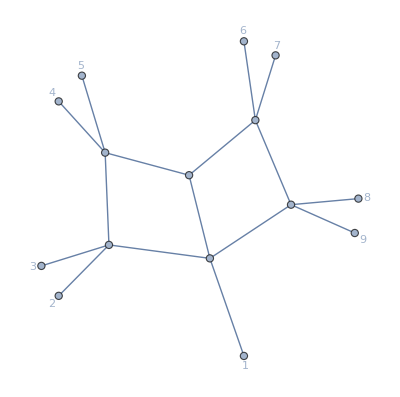

```mathematica
Delta6=FB[Int[{1,9,7},{5,6,8}],3,4]^2 FB[1,2,5,6]^2+2 FB[Int[{1,9,7},{5,6,8}],3,4] FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,5,6]^2+FB[Int[{1,9,8},{5,6,7}],3,4]^2 FB[1,2,5,6]^2-4 FB[Int[{1,9,7},{5,6,7}],3,4] FB[Int[{1,9,8},{5,6,8}],3,4] FB[1,2,5,6]^2-2 FB[Int[{1,9,7},{5,6,8}],1,2] FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,5,6] FB[3,4,5,6]-2 FB[Int[{1,9,7},{5,6,8}],3,4] FB[Int[{1,9,8},{5,6,7}],1,2] FB[1,2,5,6] FB[3,4,5,6]-2 FB[Int[{1,9,7},{5,6,8}],1,2] FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,5,6] FB[3,4,5,6]-2 FB[Int[{1,9,8},{5,6,7}],1,2] FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,5,6] FB[3,4,5,6]+4 FB[Int[{1,9,7},{5,6,7}],3,4] FB[Int[{1,9,8},{5,6,8}],1,2] FB[1,2,5,6] FB[3,4,5,6]+4 FB[Int[{1,9,7},{5,6,7}],1,2] FB[Int[{1,9,8},{5,6,8}],3,4] FB[1,2,5,6] FB[3,4,5,6]+FB[Int[{1,9,7},{5,6,8}],1,2]^2 FB[3,4,5,6]^2+2 FB[Int[{1,9,7},{5,6,8}],1,2] FB[Int[{1,9,8},{5,6,7}],1,2] FB[3,4,5,6]^2+FB[Int[{1,9,8},{5,6,7}],1,2]^2 FB[3,4,5,6]^2-4 FB[Int[{1,9,7},{5,6,7}],1,2] FB[Int[{1,9,8},{5,6,8}],1,2] FB[3,4,5,6]^2;
```

```mathematica
tem=ReconstructExp[Delta6,{FB[3,4,5,6],FB[5,6,7,8],-FB[1,7,8,9],FB[1,2,3,4],FB[1,2,5,6],-FB[1,5,6,9],FB[3,4,7,8],FB[1,2,7,8],-FB[1,3,4,9]},deBug->True]
```

pow: 6

list: {1,1,1,1,2,2,3,3,4,4,5,5,5,5,6,6,6,6,7,7,8,8,9,9}

basis: {FB[3,4,5,6],FB[5,6,7,8],FB[1,7,8,9],FB[1,2,3,4],FB[1,2,5,6],FB[1,5,6,9],FB[3,4,7,8],FB[1,2,7,8],FB[1,3,4,9]}

length of ansatz: 15

session time: 0.47657

tem1 {FB[1,2,5,6]^2 FB[1,7,8,9]^2 FB[3,4,5,6]^2,FB[1,2,5,6] FB[1,2,7,8] FB[1,5,6,9] FB[1,7,8,9] FB[3,4,5,6]^2,FB[1,2,7,8]^2 FB[1,5,6,9]^2 FB[3,4,5,6]^2,FB[1,2,3,4] FB[1,2,5,6] FB[1,5,6,9] FB[1,7,8,9] FB[3,4,5,6] FB[5,6,7,8],FB[1,2,5,6]^2 FB[1,3,4,9] FB[1,7,8,9] FB[3,4,5,6] FB[5,6,7,8],FB[1,2,3,4] FB[1,2,7,8] FB[1,5,6,9]^2 FB[3,4,5,6] FB[5,6,7,8],FB[1,2,5,6] FB[1,2,7,8] FB[1,3,4,9] FB[1,5,6,9] FB[3,4,5,6] FB[5,6,7,8],FB[1,2,5,6]^2 FB[1,5,6,9] FB[1,7,8,9] FB[3,4,5,6] FB[3,4,7,8],FB[1,2,5,6] FB[1,2,7,8] FB[1,5,6,9]^2 FB[3,4,5,6] FB[3,4,7,8],FB[1,2,3,4]^2 FB[1,5,6,9]^2 FB[5,6,7,8]^2,FB[1,2,3,4] FB[1,2,5,6] FB[1,3,4,9] FB[1,5,6,9] FB[5,6,7,8]^2,FB[1,2,5,6]^2 FB[1,3,4,9]^2 FB[5,6,7,8]^2,FB[1,2,3,4] FB[1,2,5,6] FB[1,5,6,9]^2 FB[3,4,7,8] FB[5,6,7,8],FB[1,2,5,6]^2 FB[1,3,4,9] FB[1,5,6,9] FB[3,4,7,8] FB[5,6,7,8],FB[1,2,5,6]^2 FB[1,5,6,9]^2 FB[3,4,7,8]^2}

session time: 0.64784

FB[1,2,7,8]^2 FB[1,5,6,9]^2 FB[3,4,5,6]^2-2 FB[1,2,5,6] FB[1,2,7,8] FB[1,5,6,9]^2 FB[3,4,5,6] FB[3,4,7,8]+FB[1,2,5,6]^2 FB[1,5,6,9]^2 FB[3,4,7,8]^2+2 FB[1,2,5,6] FB[1,2,7,8] FB[1,3,4,9] FB[1,5,6,9] FB[3,4,5,6] FB[5,6,7,8]-4 FB[1,2,3,4] FB[1,2,5,6] FB[1,5,6,9] FB[1,7,8,9] FB[3,4,5,6] FB[5,6,7,8]-2 FB[1,2,5,6]^2 FB[1,3,4,9] FB[1,5,6,9] FB[3,4,7,8] FB[5,6,7,8]+FB[1,2,5,6]^2 FB[1,3,4,9]^2 FB[5,6,7,8]^2

Check they are indeed the same with each other

```mathematica
tem-Delta6//FBToNum
```

0

Not all expressions can be written only with Mandelstam variables!

```mathematica
ReconstructExp[FB[Int[{1,9,8},{5,6,8}],3,4] (FB[Int[{1,9,8},{5,6,8}],3,4] FB[1,2,5,6]-FB[Int[{1,9,8},{5,6,8}],1,2] FB[3,4,5,6]),{FB[3,4,5,6],FB[5,6,7,8],-FB[1,7,8,9],FB[1,2,3,4],FB[1,2,5,6],-FB[1,5,6,9],FB[3,4,7,8],FB[1,2,7,8],-FB[1,3,4,9]} ]
```

no such expressions can be constructed!

$Failed

Now we give an example calculating cross ratios of solutions between two Schubert problems

```mathematica
SchubertSolve[{x[1],x[3],x[5]},9]
```

SchubertSolve::warning: Results depend on the parameterization! You can specify the parameterization by option "Param" like "Param"->{3,4}, then it will be parametrized as Z[3]+α*Z[4]. Here we choose one such parameterization.

{Int[{1,9,4},{2,3,4}]+α (Int[{1,9,4},{2,3,5}]+Int[{1,9,5},{2,3,4}])+α^2 Int[{1,9,5},{2,3,5}]}

```mathematica
sol1=Solve[FB[Int[{9,1,4},{2,3,4}],6,7]+α*(FB[Int[{9,1,4},{2,3,5}],6,7]+FB[Int[{9,1,5},{2,3,4}],6,7])+α^2*(FB[Int[{9,1,5},{2,3,5}],6,7])==0,α]
```

{{α→1/(2 FB[Int[{9,1,5},{2,3,5}],6,7])(-FB[Int[{9,1,4},{2,3,5}],6,7]-FB[Int[{9,1,5},{2,3,4}],6,7]-√((FB[Int[{9,1,4},{2,3,5}],6,7]+FB[Int[{9,1,5},{2,3,4}],6,7])^2-4 FB[Int[{9,1,4},{2,3,4}],6,7] FB[Int[{9,1,5},{2,3,5}],6,7]))},{α→1/(2 FB[Int[{9,1,5},{2,3,5}],6,7])(-FB[Int[{9,1,4},{2,3,5}],6,7]-FB[Int[{9,1,5},{2,3,4}],6,7]+√((FB[Int[{9,1,4},{2,3,5}],6,7]+FB[Int[{9,1,5},{2,3,4}],6,7])^2-4 FB[Int[{9,1,4},{2,3,4}],6,7] FB[Int[{9,1,5},{2,3,5}],6,7]))}}

```mathematica
ReconstructExp[(FB[Int[{9,1,4},{2,3,5}],6,7]+FB[Int[{9,1,5},{2,3,4}],6,7])^2-4 FB[Int[{9,1,4},{2,3,4}],6,7] FB[Int[{9,1,5},{2,3,5}],6,7],{FB[9,1,2,3],FB[2,3,4,5],FB[4,5,6,7],FB[7,8,9,1],FB[7,8,2,3],-FB[1,4,5,9],FB[2,3,6,7],FB[4,5,7,8],-FB[1,6,7,9]}]/.{FB[1,2,3,9]->-m12,FB[2,3,4,5]->m22,FB[4,5,6,7]->m32,FB[1,7,8,9]->-m52,FB[7,8,2,3]->s15,FB[1,4,5,9]->-s12,FB[2,3,6,7]->s23,FB[4,5,7,8]->s34,FB[1,6,7,9]->-s45}
```

m12^2 m32^2-2 m12 m32 s12 s23+s12^2 s23^2-2 m12 m22 m32 s45-2 m22 s12 s23 s45+m22^2 s45^2

```mathematica
sol2=Solve[FB[Int[{9,1,4},{2,3,4}],7,8]+β*(FB[Int[{9,1,4},{2,3,5}],7,8]+FB[Int[{9,1,5},{2,3,4}],7,8])+β^2*(FB[Int[{9,1,5},{2,3,5}],7,8])==0,β]
```

{{β→1/(2 FB[Int[{9,1,5},{2,3,5}],7,8])(-FB[Int[{9,1,4},{2,3,5}],7,8]-FB[Int[{9,1,5},{2,3,4}],7,8]-√((FB[Int[{9,1,4},{2,3,5}],7,8]+FB[Int[{9,1,5},{2,3,4}],7,8])^2-4 FB[Int[{9,1,4},{2,3,4}],7,8] FB[Int[{9,1,5},{2,3,5}],7,8]))},{β→1/(2 FB[Int[{9,1,5},{2,3,5}],7,8])(-FB[Int[{9,1,4},{2,3,5}],7,8]-FB[Int[{9,1,5},{2,3,4}],7,8]+√((FB[Int[{9,1,4},{2,3,5}],7,8]+FB[Int[{9,1,5},{2,3,4}],7,8])^2-4 FB[Int[{9,1,4},{2,3,4}],7,8] FB[Int[{9,1,5},{2,3,5}],7,8]))}}

```mathematica
(*((α_+-β_+)(α_--β_-))/((α_+-β_-)(α_--β_+))*)
```

```mathematica
(sol1[[1,1,2]]-sol2[[1,1,2]])(sol1[[2,1,2]]-sol2[[2,1,2]])/(sol1[[1,1,2]]-sol2[[2,1,2]])/(sol1[[2,1,2]]-sol2[[1,1,2]])//ExpandAll//Factor
```

-((-FB[Int[{9,1,4},{2,3,5}],6,7] FB[Int[{9,1,4},{2,3,5}],7,8]-FB[Int[{9,1,4},{2,3,5}],7,8] FB[Int[{9,1,5},{2,3,4}],6,7]-FB[Int[{9,1,4},{2,3,5}],6,7] FB[Int[{9,1,5},{2,3,4}],7,8]-FB[Int[{9,1,5},{2,3,4}],6,7] FB[Int[{9,1,5},{2,3,4}],7,8]+2 FB[Int[{9,1,4},{2,3,4}],7,8] FB[Int[{9,1,5},{2,3,5}],6,7]+2 FB[Int[{9,1,4},{2,3,4}],6,7] FB[Int[{9,1,5},{2,3,5}],7,8]+√(FB[Int[{9,1,4},{2,3,5}],6,7]^2+2 FB[Int[{9,1,4},{2,3,5}],6,7] FB[Int[{9,1,5},{2,3,4}],6,7]+FB[Int[{9,1,5},{2,3,4}],6,7]^2-4 FB[Int[{9,1,4},{2,3,4}],6,7] FB[Int[{9,1,5},{2,3,5}],6,7]) √(FB[Int[{9,1,4},{2,3,5}],7,8]^2+2 FB[Int[{9,1,4},{2,3,5}],7,8] FB[Int[{9,1,5},{2,3,4}],7,8]+FB[Int[{9,1,5},{2,3,4}],7,8]^2-4 FB[Int[{9,1,4},{2,3,4}],7,8] FB[Int[{9,1,5},{2,3,5}],7,8]))/(FB[Int[{9,1,4},{2,3,5}],6,7] FB[Int[{9,1,4},{2,3,5}],7,8]+FB[Int[{9,1,4},{2,3,5}],7,8] FB[Int[{9,1,5},{2,3,4}],6,7]+FB[Int[{9,1,4},{2,3,5}],6,7] FB[Int[{9,1,5},{2,3,4}],7,8]+FB[Int[{9,1,5},{2,3,4}],6,7] FB[Int[{9,1,5},{2,3,4}],7,8]-2 FB[Int[{9,1,4},{2,3,4}],7,8] FB[Int[{9,1,5},{2,3,5}],6,7]-2 FB[Int[{9,1,4},{2,3,4}],6,7] FB[Int[{9,1,5},{2,3,5}],7,8]+√(FB[Int[{9,1,4},{2,3,5}],6,7]^2+2 FB[Int[{9,1,4},{2,3,5}],6,7] FB[Int[{9,1,5},{2,3,4}],6,7]+FB[Int[{9,1,5},{2,3,4}],6,7]^2-4 FB[Int[{9,1,4},{2,3,4}],6,7] FB[Int[{9,1,5},{2,3,5}],6,7]) √(FB[Int[{9,1,4},{2,3,5}],7,8]^2+2 FB[Int[{9,1,4},{2,3,5}],7,8] FB[Int[{9,1,5},{2,3,4}],7,8]+FB[Int[{9,1,5},{2,3,4}],7,8]^2-4 FB[Int[{9,1,4},{2,3,4}],7,8] FB[Int[{9,1,5},{2,3,5}],7,8])))

```mathematica
ReconstructExp[FB[Int[{9,1,4},{2,3,5}],6,7] FB[Int[{9,1,4},{2,3,5}],7,8]+FB[Int[{9,1,4},{2,3,5}],7,8] FB[Int[{9,1,5},{2,3,4}],6,7]+FB[Int[{9,1,4},{2,3,5}],6,7] FB[Int[{9,1,5},{2,3,4}],7,8]+FB[Int[{9,1,5},{2,3,4}],6,7] FB[Int[{9,1,5},{2,3,4}],7,8]-2 FB[Int[{9,1,4},{2,3,4}],7,8] FB[Int[{9,1,5},{2,3,5}],6,7]-2 FB[Int[{9,1,4},{2,3,4}],6,7] FB[Int[{9,1,5},{2,3,5}],7,8],{FB[9,1,2,3],FB[2,3,4,5],FB[4,5,6,7],FB[7,8,9,1],FB[7,8,2,3],-FB[1,4,5,9],FB[2,3,6,7],FB[4,5,7,8],-FB[1,6,7,9]}]/.{FB[1,2,3,9]->-m12,FB[2,3,4,5]->m22,FB[4,5,6,7]->m32,FB[1,7,8,9]->-m52,FB[7,8,2,3]->s15,FB[1,4,5,9]->-s12,FB[2,3,6,7]->s23,FB[4,5,7,8]->s34,FB[1,6,7,9]->-s45}
```

-m12 m22 m32 m52-m12 m32 s12 s15-m22 m52 s12 s23+s12^2 s15 s23+m12^2 m32 s34-m12 s12 s23 s34+m22^2 m52 s45-m22 s12 s15 s45-m12 m22 s34 s45

```mathematica
(Det[{{0,d[x[7],x[5]],d[x[7],x[3]],d[x[7],x[1]]},{d[x[5],x[8]],0,d[x[5],x[3]],d[x[5],x[1]]},{d[x[3],x[8]],d[x[5],x[3]],0,d[x[3],x[1]]},{d[x[1],x[8]],d[x[5],x[1]],d[x[3],x[1]],0}}]//ToMT[#,9]&)/.{FBI->FB}/.{FB[1,2,3,9]->-m12,FB[2,3,4,5]->m22,FB[4,5,6,7]->m32,FB[1,7,8,9]->-m52,FB[7,8,2,3]->s15,FB[1,4,5,9]->-s12,FB[2,3,6,7]->s23,FB[4,5,7,8]->s34,FB[1,6,7,9]->-s45}
```

-m12 m22 m32 m52-m12 m32 s12 s15-m22 m52 s12 s23+s12^2 s15 s23+m12^2 m32 s34-m12 s12 s23 s34+m22^2 m52 s45-m22 s12 s15 s45-m12 m22 s34 s45

### SchubertSolve

```mathematica
(*solve a Schubert problem specified by at most 4 conditions*)
```

```mathematica
SchubertSolve[{x[2],x[5],x[6],x[8]},9](*d[y,x[2]]=d[y,x[5]]=d[y,x[6]]=d[y,x[8]]=0*)
```

{BiTw[Int[{7,8},{4,5,6}],Int[{1,2},{4,5,6}]],Int[{5,7,8},{5,1,2}]}

```mathematica
SchubertSolve[{x[1],x[3],x[5],x[7]},9]
```

SchubertSolve::form: The explicit form of the final results depends on the parameterization! You can choose one line as basis to parameterize like "Param"->{1,2} where (12) is a line presented in this Schubert problem.

{Int[{1,9,6},{4,5,6}]+α Int[{1,9,6},{4,5,7}]+α Int[{1,9,7},{4,5,6}]+α^2 Int[{1,9,7},{4,5,7}],{α→1/(2 FB[Int[{1,9,7},{4,5,7}],2,3])(-FB[Int[{1,9,6},{4,5,7}],2,3]-FB[Int[{1,9,7},{4,5,6}],2,3]-√((FB[Int[{1,9,6},{4,5,7}],2,3]+FB[Int[{1,9,7},{4,5,6}],2,3])^2-4 FB[Int[{1,9,6},{4,5,6}],2,3] FB[Int[{1,9,7},{4,5,7}],2,3])),α→1/(2 FB[Int[{1,9,7},{4,5,7}],2,3])(-FB[Int[{1,9,6},{4,5,7}],2,3]-FB[Int[{1,9,7},{4,5,6}],2,3]+√((FB[Int[{1,9,6},{4,5,7}],2,3]+FB[Int[{1,9,7},{4,5,6}],2,3])^2-4 FB[Int[{1,9,6},{4,5,6}],2,3] FB[Int[{1,9,7},{4,5,7}],2,3]))}}

```mathematica
SchubertSolve[{x[1],x[3],x[5]},9](*give a parameterization for three conditions*)
```

SchubertSolve::warning: Results depend on the parameterization! You can specify the parameterization by option "Param" like "Param"->{3,4}, then it will be parametrized as Z[3]+α*Z[4]. Here we choose one such parameterization.

{Int[{1,9,4},{2,3,4}]+α Int[{1,9,4},{2,3,5}]+α Int[{1,9,5},{2,3,4}]+α^2 Int[{1,9,5},{2,3,5}]}

```mathematica
SchubertSolve[{x[1],x[3],x[5]},9,"Param"->{2,3}](*give a different parameterization for three conditions*)
```

SchubertSolve::warning: Results depend on the parameterization! You can specify the parameterization by option "Param" like "Param"->{3,4}, then it will be parametrized as Z[3]+α*Z[4]. Here we choose one such parameterization.

{Int[{4,5,2},{1,9,2}]+α Int[{4,5,2},{1,9,3}]+α Int[{4,5,3},{1,9,2}]+α^2 Int[{4,5,3},{1,9,3}]}

```mathematica
SchubertSolve[{x[2],x[5],x[Infinity]},9](*give a parameterization for three conditions involving infinity*)
```

SchubertSolve::warning: Results depend on the parameterization! You can specify the parameterization by option "Param" like "Param"->{3,4}, then it will be parametrized as Z[3]+α*Z[4]. Here we choose one such parameterization.

{Int[{4,5,1},{-2,-1,1}]+α Int[{4,5,1},{-2,-1,2}]+α Int[{4,5,2},{-2,-1,1}]+α^2 Int[{4,5,2},{-2,-1,2}]}

```mathematica
FB[Int[{4,5,1},{-2,-1,1}]+α Int[{4,5,1},{-2,-1,2}]+α Int[{4,5,2},{-2,-1,1}]+α^2 Int[{4,5,2},{-2,-1,2}],6,7]//MTExpand//FBToNum
```

-426242761214673102018816-227137059368952825473584 α-29387721670674583447504 α^2

### LandauSolveAll

#### one-loop two-mass-hard box

given the propagator lists and some replacement rule for kinematics

```mathematica
dlist={d[y[1],x[1]],d[y[1],x[2]],d[y[1],x[3]],d[y[1],x[5]]};
krep={d[x[1],x[2]]->0,d[x[2],x[3]]->0,d[x[3],x[4]]->0,d[x[5],x[4]]->0,d[x[5],x[6]]->0,d[x[1],x[6]]->0};
```

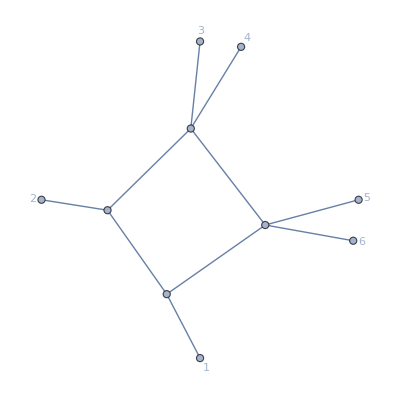

```mathematica
DrawFeynGraph[dlist,6]
```

```mathematica
result=LandauSolveAll[dlist,{y[1]},6,krep];
```

totally 11 need to be considered!

```mathematica
lslist=ExtractLS[result];
```

```mathematica
slist=ExtractSchubert[result];
```

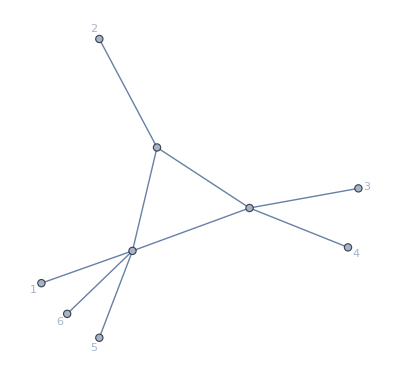
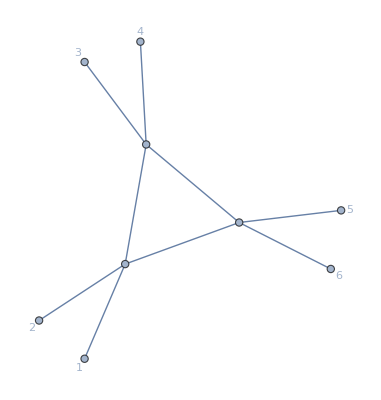
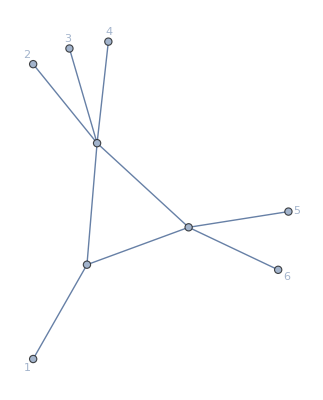
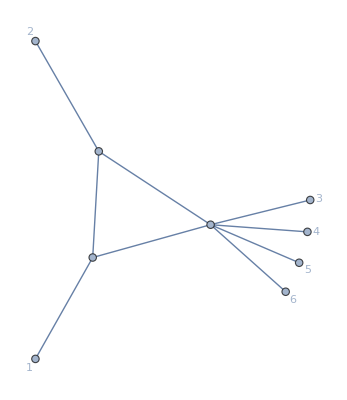
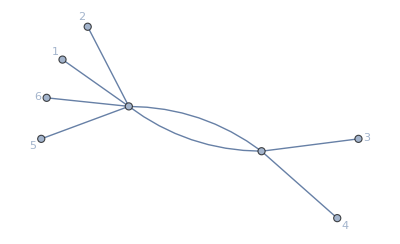
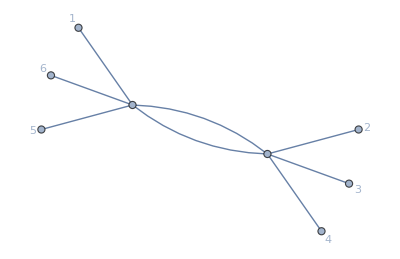
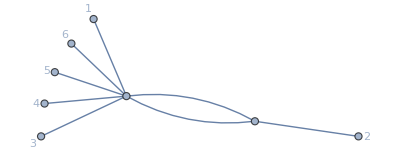
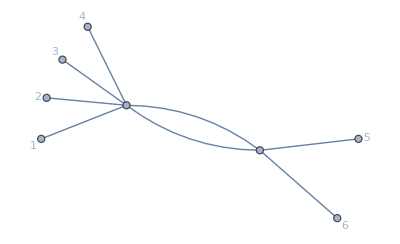
{{-Graphics-,{{y[1],{d[x[1],y[1]],d[x[2],y[1]],d[x[3],y[1]],d[x[5],y[1]]}}}},{-Graphics-,{{y[1],{d[x[2],y[1]],d[x[3],y[1]],d[x[5],y[1]]}}}},{-Graphics-,{{y[1],{d[x[1],y[1]],d[x[3],y[1]],d[x[5],y[1]]}}}},{-Graphics-,{{y[1],{d[x[1],y[1]],d[x[2],y[1]],d[x[5],y[1]]}}}},{-Graphics-,{{y[1],{d[x[1],y[1]],d[x[2],y[1]],d[x[3],y[1]]}}}},{-Graphics-,{{y[1],{d[x[3],y[1]],d[x[5],y[1]]}}}},{-Graphics-,{{y[1],{d[x[2],y[1]],d[x[5],y[1]]}}}},{-Graphics-,{{y[1],{d[x[2],y[1]],d[x[3],y[1]]}}}},{-Graphics-,{{y[1],{d[x[1],y[1]],d[x[5],y[1]]}}}},{-Graphics-,{{y[1],{d[x[1],y[1]],d[x[3],y[1]]}}}},{-Graphics-,{{y[1],{d[x[1],y[1]],d[x[2],y[1]]}}}}}

```mathematica
slist
```

```mathematica
lslist
```

{{-Graphics-,{-FB[1,2,3,6] FB[1,2,4,5]^2}},{-Graphics-,{FB[1,2,4,5],FB[2,3,4,5]}},{-Graphics-,{-FB[1,4,5,6],-FB[1,2,3,6],FB[2,3,4,5]}},{-Graphics-,{-FB[1,4,5,6],FB[1,2,4,5]}},{-Graphics-,{-FB[1,2,3,6]}},{-Graphics-,{FB[2,3,4,5]}},{-Graphics-,{FB[1,2,4,5]}},{-Graphics-,{}},{-Graphics-,{-FB[1,4,5,6]}},{-Graphics-,{-FB[1,2,3,6]}},{-Graphics-,{}}}

#### two-loop examples

given the propagator lists and some replacement rule for kinematics

```mathematica
dlist={d[y[1],x[2]],d[y[1],x[3]],d[y[1],x[9]],d[y[1],x[8]],d[y[2],x[3]],d[y[2],x[5]],d[y[2],x[6]],d[y[1],y[2]]};
krep={d[x[2],x[3]]->0,d[x[5],x[6]]->0,d[x[8],x[9]]->0};
```

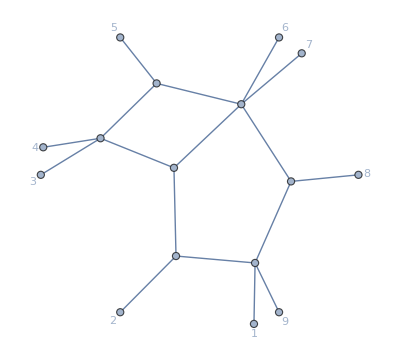

```mathematica
{DrawFeynGraph[dlist,9]}
```

Solve leading Landau singularities for every sector

```mathematica
result=LandauSolveAll[dlist,{y[1],y[2]},9,krep];
```

totally 148 need to be considered!

constraints equals or higher than 6!

These warnings can be neglected for now.

```mathematica
(*leading Landau singularities for every diagram*)
```

```mathematica
lslist=ExtractLS[result];
```

```mathematica
(*the "schubert problem" for every diagram, two loops are distinguished*)
```

```mathematica
slist=ExtractSchubert[result];
```

```mathematica
lslist[[1]]
```

{-Graphics-,{FB[2,3,5,8] FB[2,4,5,6],-FB[Int[{1,5,6},{7,8,9}],3,2] FB[2,3,4,5]+FB[Int[{1,4,5},{7,8,9}],3,2] FB[2,3,5,6],-FB[1,2,3,8] FB[2,7,8,9],-FB[2,3,5,8] FB[2,7,8,9],-FB[Int[{1,8,9},{4,5,6}],3,2] FB[2,3,7,8]+FB[Int[{1,7,8},{4,5,6}],3,2] FB[2,3,8,9]}}

```mathematica
slist[[1]]
```

{-Graphics-,{{y[1],{d[x[2],y[1]],d[x[3],y[1]],d[x[8],y[1]],d[x[9],y[1]],d[x[3],x[6]] d[x[5],y[1]]-d[x[3],x[5]] d[x[6],y[1]]}},{y[2],{d[x[2],y[2]],d[x[3],y[2]],d[x[5],y[2]],d[x[6],y[2]],d[x[3],x[9]] d[x[8],y[2]]-d[x[3],x[8]] d[x[9],y[2]]}}}}

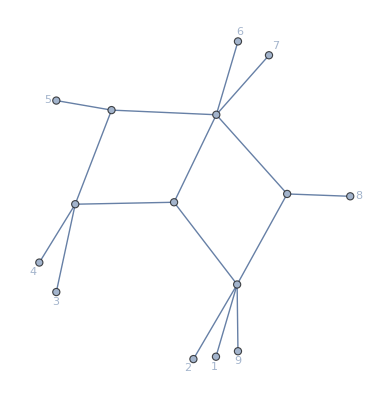
{-Graphics-,{-((FB[Int[{7,8,9},{4,5,6}],2,3] (FB[Int[{2,3,8},{5,6,8}],9,7] FB[2,3,4,5]-FB[Int[{2,3,8},{4,5,8}],9,7] FB[2,3,5,6]) FB[2,3,7,8])/((-FB[Int[{2,3,7},{5,6,7}],9,8] FB[2,3,4,5]+FB[Int[{2,3,7},{4,5,7}],9,8] FB[2,3,5,6]) FB[3,4,5,6])),(FB[Int[{7,8,9},{4,5,6}],2,3] FB[2,3,4,5] FB[2,3,5,8])/(FB[2,3,4,8] FB[3,7,8,9])}}

```mathematica
lslist[[2]]
```

```mathematica
slist[[2]]
```

{-Graphics-,{{y[1],{d[x[3],y[1]],d[x[8],y[1]],d[x[9],y[1]],d[x[3],x[6]] d[x[5],y[1]]-d[x[3],x[5]] d[x[6],y[1]]}},{y[2],{d[x[3],y[2]],d[x[5],y[2]],d[x[6],y[2]],d[x[3],x[9]] d[x[8],y[2]]-d[x[3],x[8]] d[x[9],y[2]]}}}}

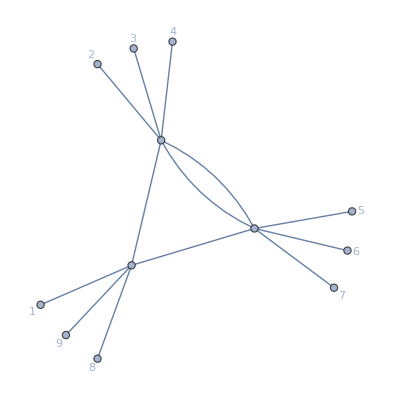
{-Graphics-,{FB[1,2,7,8],FB[1,2,4,5],FB[4,5,7,8]}}

```mathematica
lslist[[-25]]
```

```mathematica
slist[[-25]]
```

{-Graphics-,{{y[1],{d[x[2],y[1]],d[x[5],y[1]],d[x[8],y[1]]}},{y[2],{d[x[2],y[2]],d[x[5],y[2]],d[x[8],y[2]]}}}}

Only analyse one specific sector

```mathematica
result=LandauSolveAll[{d[y[1],x[2]],d[y[1],x[3]],d[y[1],x[9]],d[y[1],x[8]],d[y[2],x[3]],d[y[2],x[5]],d[y[2],x[6]]},{y[1],y[2]},9,krep,"NoSubset"->True];
```

totally 1 need to be considered!

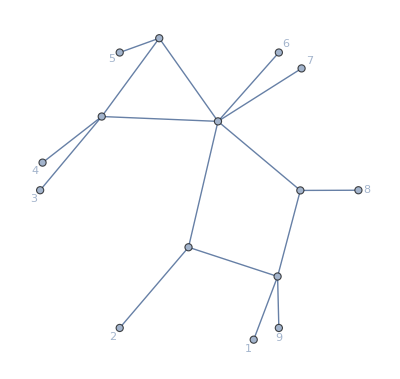
{{-Graphics-,{FB[2,3,4,5],FB[2,3,5,6],FB[1,2,3,8] FB[2,7,8,9]}}}

```mathematica
ExtractLS[result]
```

```mathematica
ExtractSchubert[result]
```

{{-Graphics-,{{y[1],{d[x[2],y[1]],d[x[3],y[1]],d[x[8],y[1]],d[x[9],y[1]]}},{y[2],{d[x[3],y[2]],d[x[5],y[2]],d[x[6],y[2]]}}}}}

```mathematica
dlist={d[y[1],x[3]],d[y[1],x[4]],d[y[1],x[5]],d[y[2],x[6]],d[y[2],x[1]],d[y[2],x[2]],d[y[1],y[2]]};
krep={d[x[1],x[2]]->0,d[x[2],x[3]]->0,d[x[3],x[4]]->0,d[x[4],x[5]]->0,d[x[5],x[6]]->0,d[x[1],x[6]]->0};
```

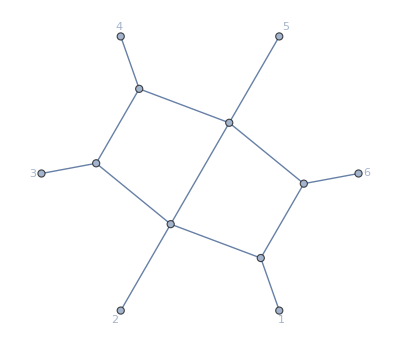

```mathematica
{DrawFeynGraph[dlist,6]}
```

```mathematica
result=LandauSolveAll[dlist,{y[1],y[2]},6,krep];
```

totally 65 need to be considered!

we need to promote the loop momentum to 6 dimension or higher to solve this constraints.

we need to promote the loop momentum to 6 dimension or higher to solve this constraints.

Above information means for some sectors there are six constraints for one loop momentum. This should be considered as leading singularities for loop momentum in 6 dimensions.

```mathematica
lslist=ExtractLS[result];
```

```mathematica
slist=ExtractSchubert[result];
```

```mathematica
lslist[[1]]
```

{-Graphics-,{FB[1,2,5,6],FB[2,3,4,5]}}

```mathematica
lslist[[All,2]]//Flatten
```

{FB[1,2,5,6],FB[2,3,4,5],FB[1,2,5,6],FB[1,4,5,6],FB[1,2,5,6] FB[3,4,5,6],FB[1,2,5,6],-FB[1,2,5,6] FB[2,4,5,6],FB[1,2,3,5] FB[1,4,5,6],FB[2,3,4,5],FB[1,2,5,6],-FB[1,3,5,6],FB[1,2,5,6] FB[2,3,4,6],FB[1,2,5,6],FB[2,4,5,6],FB[1,2,3,5] FB[3,4,5,6],FB[2,3,4,5],-FB[1,3,5,6] FB[3,4,5,6],-FB[1,4,5,6] FB[2,3,4,6],FB[2,3,4,5],FB[1,2,5,6],FB[2,3,4,5],-FB[1,3,4,5],FB[1,2,4,6] FB[2,3,4,5],FB[2,3,4,5],FB[1,2,5,6],-FB[1,2,5,6] FB[1,4,5,6],FB[1,2,5,6],FB[1,2,5,6] FB[1,3,4,6]^2,FB[1,2,5,6],-FB[1,2,4,5]^2 FB[3,4,5,6],-FB[1,4,5,6] FB[3,4,5,6],FB[1,2,5,6],FB[1,2,4,6] FB[1,3,4,5],FB[1,2,5,6],-FB[1,2,3,6] FB[1,2,5,6],FB[1,2,5,6],FB[1,2,3,5] FB[2,4,5,6],FB[2,3,4,5],-FB[1,4,5,6] FB[2,3,5,6]^2,FB[2,3,4,5],FB[1,2,5,6],FB[2,3,4,5],-FB[1,2,3,6] FB[1,2,4,5]^2,FB[2,3,4,5],FB[1,2,5,6],FB[1,2,3,4] FB[2,3,5,6]^2,FB[1,3,5,6] FB[2,3,4,6],FB[1,2,5,6],FB[2,3,4,5] FB[3,4,5,6],FB[2,3,4,5],FB[1,2,5,6],FB[2,3,4,5],FB[2,3,4,5],FB[1,2,3,4] FB[2,3,4,5],FB[2,3,4,5],FB[1,3,4,6]^2 FB[2,3,4,5],FB[2,3,4,5],FB[2,3,4,5],-FB[1,2,3,4] FB[1,2,3,6],FB[1,2,5,6],FB[1,2,4,5],-FB[1,4,5,6],-FB[1,4,5,6],FB[1,2,4,5],FB[1,2,5,6],FB[1,2,3,4],FB[3,4,5,6],-FB[1,3,4,6],FB[3,4,5,6],FB[3,4,5,6],FB[1,2,5,6],FB[1,2,4,5],FB[1,2,3,4],-FB[1,4,5,6],-FB[1,3,4,6],-FB[1,3,4,6],FB[1,2,3,4],FB[1,2,5,6],FB[2,3,5,6],-FB[1,2,3,6],FB[2,3,5,6],FB[2,3,5,6],FB[2,3,4,5],FB[1,2,5,6],FB[2,3,4,5],FB[2,3,4,5],FB[1,2,4,5],FB[2,3,4,5],-FB[1,4,5,6],-FB[1,2,3,6],FB[2,3,4,5],FB[2,3,4,5],FB[2,3,5,6],FB[3,4,5,6],FB[1,2,5,6],FB[1,2,3,4],-FB[1,3,4,6],-FB[1,2,3,6],-FB[1,2,3,6],FB[1,2,4,5],-FB[1,4,5,6],FB[3,4,5,6],FB[1,2,3,4],-FB[1,3,4,6],FB[2,3,5,6],-FB[1,2,3,6]}

```mathematica
(FactorList[#][[All,1]]&/@(lslist[[All,2]]//Flatten))//Flatten//DeleteCases[#,_?NumericQ]&//DeleteDuplicates[#,(#1-#2===0)||(#1+#2===0)&]&//Flatten//DisplayAll//Sort
```

{⟨1234⟩,⟨1235⟩,⟨1236⟩,⟨1245⟩,⟨1246⟩,⟨1256⟩,⟨1345⟩,⟨1346⟩,⟨1356⟩,⟨1456⟩,⟨2345⟩,⟨2346⟩,⟨2356⟩,⟨2456⟩,⟨3456⟩}

```mathematica
(*6-point alphabet*)
```

```mathematica
alphabet={FB[6,1,2,3]*FB[3,4,5,6]/(FB[6,1,3,4]*FB[2,3,5,6]),FB[1,2,3,4]*FB[4,5,6,1]/(FB[1,2,4,5]*FB[3,4,6,1]),FB[2,3,4,5]*FB[5,6,1,2]/(FB[2,3,5,6]*FB[4,5,1,2]),FB[5,6,1,3]*FB[6,2,3,4]/(FB[6,1,3,4]*FB[2,3,5,6]),FB[6,1,2,4]*FB[1,3,4,5]/(FB[1,2,4,5]*FB[3,4,6,1]),FB[1,2,3,5]*FB[2,4,5,6]/(FB[2,3,5,6]*FB[4,5,1,2]),FB[1,3,4,5]*FB[2,4,5,6]*FB[1,2,3,6]/(FB[1,2,3,5]*FB[3,4,5,6]*FB[1,2,4,6]),FB[1,2,3,5]*FB[2,3,4,6]*FB[1,4,5,6]/(FB[1,2,3,4]*FB[2,4,5,6]*FB[1,3,5,6]),FB[2,3,4,5]*FB[1,3,5,6]*FB[1,2,4,6]/(FB[1,3,4,5]*FB[2,3,4,6]*FB[1,2,5,6])};
```

```mathematica
alphabet//DisplayAll
```

{(⟨1236⟩ ⟨3456⟩)/(⟨1346⟩ ⟨2356⟩),(⟨1234⟩ ⟨1456⟩)/(⟨1245⟩ ⟨1346⟩),(⟨1256⟩ ⟨2345⟩)/(⟨1245⟩ ⟨2356⟩),(⟨1356⟩ ⟨2346⟩)/(⟨1346⟩ ⟨2356⟩),(⟨1246⟩ ⟨1345⟩)/(⟨1245⟩ ⟨1346⟩),(⟨1235⟩ ⟨2456⟩)/(⟨1245⟩ ⟨2356⟩),(⟨1236⟩ ⟨1345⟩ ⟨2456⟩)/(⟨1235⟩ ⟨1246⟩ ⟨3456⟩),(⟨1235⟩ ⟨1456⟩ ⟨2346⟩)/(⟨1234⟩ ⟨1356⟩ ⟨2456⟩),(⟨1246⟩ ⟨1356⟩ ⟨2345⟩)/(⟨1256⟩ ⟨1345⟩ ⟨2346⟩)}

```mathematica
(FactorList[#][[All,1]]&/@alphabet)//Flatten//DeleteDuplicates//DeleteCases[#,1]&//DisplayAll//Sort
```

{⟨1234⟩,⟨1235⟩,⟨1236⟩,⟨1245⟩,⟨1246⟩,⟨1256⟩,⟨1345⟩,⟨1346⟩,⟨1356⟩,⟨1456⟩,⟨2345⟩,⟨2346⟩,⟨2356⟩,⟨2456⟩,⟨3456⟩}

```mathematica
slist[[1]]
```

{-Graphics-,{{y[1],{d[x[1],y[1]],d[x[2],y[1]],d[x[3],y[1]],d[x[4],y[1]],d[x[5],y[1]],d[x[6],y[1]]}},{y[2],{d[x[1],y[2]],d[x[2],y[2]],d[x[3],y[2]],d[x[4],y[2]],d[x[5],y[2]],d[x[6],y[2]]}}}}

```mathematica
LeadingLandauCond[dlist,y[1],krep,deBug->True]
```

rproplist: {{d[x[6],y[2]],d[x[1],y[2]],d[x[2],y[2]],d[y[1],y[2]]}}

tab: (0 | 0 | d[x[2],x[6]] | d[x[6],y[1]]
0 | 0 | 0 | d[x[1],y[1]]
d[x[2],x[6]] | 0 | 0 | d[x[2],y[1]]
d[x[6],y[1]] | d[x[1],y[1]] | d[x[2],y[1]] | 0)

tab: {{0,0,d[x[2],x[6]],d[x[6],y[1]]},{0,0,0,d[x[1],y[1]]},{d[x[2],x[6]],0,0,d[x[2],y[1]]},{d[x[6],y[1]],d[x[1],y[1]],d[x[2],y[1]],0}}

system: {a[3] d[x[2],x[6]]+a[4] d[x[6],y[1]],a[4] d[x[1],y[1]],a[1] d[x[2],x[6]]+a[4] d[x[2],y[1]],a[2] d[x[1],y[1]]+a[3] d[x[2],y[1]]+a[1] d[x[6],y[1]]}

sol: (d[x[2],x[6]]→0
d[x[6],y[1]]→0
d[x[1],y[1]]→0
d[x[2],y[1]]→0)

tem: {d[x[3],y[1]],d[x[4],y[1]],d[x[5],y[1]],d[y[1],y[2]],d[x[2],x[6]],d[x[6],y[1]],d[x[1],y[1]],d[x[2],y[1]],d[x[1],y[1]]^2 d[x[2],x[6]]^2}

{{d[x[2],x[6]]},{d[x[1],y[1]],d[x[2],y[1]],d[x[3],y[1]],d[x[4],y[1]],d[x[5],y[1]],d[x[6],y[1]],d[y[1],y[2]]}}

non-trivial 9-point double box

```mathematica
dlist={d[y[1],x[1]],d[y[1],x[6]],d[y[1],x[8]],d[y[2],x[6]],d[y[2],x[4]],d[y[2],x[2]],d[y[1],y[2]]};
krep={d[x[1],x[2]]->0};
```

```mathematica
{DrawFeynGraph[dlist,9]}
```

{-Graphics-}

```mathematica
Options[LandauSolveAll]
```

{deBug→False,NoSubset→False}

```mathematica
result=LandauSolveAll[dlist,{y[1],y[2]},9,krep,"NoSubset"->True,deBug->True];
```

totally 1 need to be considered!

subset: {d[x[1],y[1]],d[x[6],y[1]],d[x[8],y[1]],d[x[6],y[2]],d[x[4],y[2]],d[x[2],y[2]],d[y[1],y[2]]}

```mathematica
lslist=ExtractLS[result];
```

```mathematica
slist=ExtractSchubert[result];
```

```mathematica
sollist=ExtractSolution[result];
```

```mathematica
slist//ToMT[#,9]&//DisplayAll
```

{{-Graphics-,{{y[1],{⟨AB91⟩,⟨AB56⟩,⟨AB78⟩,⟨3456⟩ ⟨AB12⟩-⟨1256⟩ ⟨AB34⟩}},{y[2],{⟨CD12⟩,⟨CD34⟩,⟨CD56⟩,-⟨9156⟩ ⟨CD78⟩+⟨5678⟩ ⟨CD91⟩}}}}}

```mathematica
sollist(*solutions of loop momenta in top sectors*)
```

{{-Graphics-,{{y[1],{{Int[{1,9,7},{5,6,7}]+α (Int[{1,9,7},{5,6,8}]+Int[{1,9,8},{5,6,7}])+α^2 Int[{1,9,8},{5,6,8}]},{α→(FB[1,2,8,9] FB[1,5,6,7] FB[3,4,5,6]+FB[1,2,7,9] FB[1,5,6,8] FB[3,4,5,6]-2 FB[1,2,5,6] FB[1,7,8,9] FB[3,4,5,6]-2 FB[1,2,5,6] FB[1,4,7,9] FB[3,5,6,8]+FB[1,2,5,6] FB[1,4,7,8] FB[3,5,6,9]+FB[1,2,5,6] FB[1,4,5,6] FB[3,7,8,9]+2 FB[1,2,5,6] FB[1,3,7,9] FB[4,5,6,8]-FB[1,2,5,6] FB[1,3,7,8] FB[4,5,6,9]-FB[1,2,5,6] FB[1,3,5,6] FB[4,7,8,9]-√((-FB[1,2,8,9] FB[1,5,6,7] FB[3,4,5,6]-FB[1,2,7,9] FB[1,5,6,8] FB[3,4,5,6]+2 FB[1,2,5,6] FB[1,7,8,9] FB[3,4,5,6]+2 FB[1,2,5,6] FB[1,4,7,9] FB[3,5,6,8]-FB[1,2,5,6] FB[1,4,7,8] FB[3,5,6,9]-FB[1,2,5,6] FB[1,4,5,6] FB[3,7,8,9]-2 FB[1,2,5,6] FB[1,3,7,9] FB[4,5,6,8]+FB[1,2,5,6] FB[1,3,7,8] FB[4,5,6,9]+FB[1,2,5,6] FB[1,3,5,6] FB[4,7,8,9])^2-4 (-FB[1,2,7,9] FB[1,5,6,7] FB[3,4,5,6]+FB[1,2,5,6] FB[1,5,6,7] FB[3,4,7,9]-FB[1,2,5,6] FB[1,3,4,7] FB[5,6,7,9]) (-FB[1,2,8,9] FB[1,5,6,8] FB[3,4,5,6]+FB[1,2,5,6] FB[1,5,6,8] FB[3,4,8,9]-FB[1,2,5,6] FB[1,3,4,8] FB[5,6,8,9])))/(2 (-FB[1,2,8,9] FB[1,5,6,8] FB[3,4,5,6]+FB[1,2,5,6] FB[1,5,6,8] FB[3,4,8,9]-FB[1,2,5,6] FB[1,3,4,8] FB[5,6,8,9])),α→(FB[1,2,8,9] FB[1,5,6,7] FB[3,4,5,6]+FB[1,2,7,9] FB[1,5,6,8] FB[3,4,5,6]-2 FB[1,2,5,6] FB[1,7,8,9] FB[3,4,5,6]-2 FB[1,2,5,6] FB[1,4,7,9] FB[3,5,6,8]+FB[1,2,5,6] FB[1,4,7,8] FB[3,5,6,9]+FB[1,2,5,6] FB[1,4,5,6] FB[3,7,8,9]+2 FB[1,2,5,6] FB[1,3,7,9] FB[4,5,6,8]-FB[1,2,5,6] FB[1,3,7,8] FB[4,5,6,9]-FB[1,2,5,6] FB[1,3,5,6] FB[4,7,8,9]+√((-FB[1,2,8,9] FB[1,5,6,7] FB[3,4,5,6]-FB[1,2,7,9] FB[1,5,6,8] FB[3,4,5,6]+2 FB[1,2,5,6] FB[1,7,8,9] FB[3,4,5,6]+2 FB[1,2,5,6] FB[1,4,7,9] FB[3,5,6,8]-FB[1,2,5,6] FB[1,4,7,8] FB[3,5,6,9]-FB[1,2,5,6] FB[1,4,5,6] FB[3,7,8,9]-2 FB[1,2,5,6] FB[1,3,7,9] FB[4,5,6,8]+FB[1,2,5,6] FB[1,3,7,8] FB[4,5,6,9]+FB[1,2,5,6] FB[1,3,5,6] FB[4,7,8,9])^2-4 (-FB[1,2,7,9] FB[1,5,6,7] FB[3,4,5,6]+FB[1,2,5,6] FB[1,5,6,7] FB[3,4,7,9]-FB[1,2,5,6] FB[1,3,4,7] FB[5,6,7,9]) (-FB[1,2,8,9] FB[1,5,6,8] FB[3,4,5,6]+FB[1,2,5,6] FB[1,5,6,8] FB[3,4,8,9]-FB[1,2,5,6] FB[1,3,4,8] FB[5,6,8,9])))/(2 (-FB[1,2,8,9] FB[1,5,6,8] FB[3,4,5,6]+FB[1,2,5,6] FB[1,5,6,8] FB[3,4,8,9]-FB[1,2,5,6] FB[1,3,4,8] FB[5,6,8,9]))}}},{y[2],{{Int[{5,6,3},{1,2,3}]+α (Int[{5,6,3},{1,2,4}]+Int[{5,6,4},{1,2,3}])+α^2 Int[{5,6,4},{1,2,4}]},{α→(-FB[1,4,7,8] FB[1,5,6,9] FB[2,3,5,6]+FB[1,4,5,6] FB[1,5,6,9] FB[2,3,7,8]-FB[1,3,7,8] FB[1,5,6,9] FB[2,4,5,6]+FB[1,3,5,6] FB[1,5,6,9] FB[2,4,7,8]-FB[1,2,4,9] FB[1,3,5,6] FB[5,6,7,8]-FB[1,2,3,9] FB[1,4,5,6] FB[5,6,7,8]-√((FB[1,4,7,8] FB[1,5,6,9] FB[2,3,5,6]-FB[1,4,5,6] FB[1,5,6,9] FB[2,3,7,8]+FB[1,3,7,8] FB[1,5,6,9] FB[2,4,5,6]-FB[1,3,5,6] FB[1,5,6,9] FB[2,4,7,8]+FB[1,2,4,9] FB[1,3,5,6] FB[5,6,7,8]+FB[1,2,3,9] FB[1,4,5,6] FB[5,6,7,8])^2-4 (FB[1,3,7,8] FB[1,5,6,9] FB[2,3,5,6]-FB[1,3,5,6] FB[1,5,6,9] FB[2,3,7,8]+FB[1,2,3,9] FB[1,3,5,6] FB[5,6,7,8]) (FB[1,4,7,8] FB[1,5,6,9] FB[2,4,5,6]-FB[1,4,5,6] FB[1,5,6,9] FB[2,4,7,8]+FB[1,2,4,9] FB[1,4,5,6] FB[5,6,7,8])))/(2 (FB[1,4,7,8] FB[1,5,6,9] FB[2,4,5,6]-FB[1,4,5,6] FB[1,5,6,9] FB[2,4,7,8]+FB[1,2,4,9] FB[1,4,5,6] FB[5,6,7,8])),α→(-FB[1,4,7,8] FB[1,5,6,9] FB[2,3,5,6]+FB[1,4,5,6] FB[1,5,6,9] FB[2,3,7,8]-FB[1,3,7,8] FB[1,5,6,9] FB[2,4,5,6]+FB[1,3,5,6] FB[1,5,6,9] FB[2,4,7,8]-FB[1,2,4,9] FB[1,3,5,6] FB[5,6,7,8]-FB[1,2,3,9] FB[1,4,5,6] FB[5,6,7,8]+√((FB[1,4,7,8] FB[1,5,6,9] FB[2,3,5,6]-FB[1,4,5,6] FB[1,5,6,9] FB[2,3,7,8]+FB[1,3,7,8] FB[1,5,6,9] FB[2,4,5,6]-FB[1,3,5,6] FB[1,5,6,9] FB[2,4,7,8]+FB[1,2,4,9] FB[1,3,5,6] FB[5,6,7,8]+FB[1,2,3,9] FB[1,4,5,6] FB[5,6,7,8])^2-4 (FB[1,3,7,8] FB[1,5,6,9] FB[2,3,5,6]-FB[1,3,5,6] FB[1,5,6,9] FB[2,3,7,8]+FB[1,2,3,9] FB[1,3,5,6] FB[5,6,7,8]) (FB[1,4,7,8] FB[1,5,6,9] FB[2,4,5,6]-FB[1,4,5,6] FB[1,5,6,9] FB[2,4,7,8]+FB[1,2,4,9] FB[1,4,5,6] FB[5,6,7,8])))/(2 (FB[1,4,7,8] FB[1,5,6,9] FB[2,4,5,6]-FB[1,4,5,6] FB[1,5,6,9] FB[2,4,7,8]+FB[1,2,4,9] FB[1,4,5,6] FB[5,6,7,8]))}}}}}}

```mathematica
(*above sector can be combined with the following two box configurations in subsectors*)
```

```mathematica
SchubertSolve[{x[6],x[8],x[1],x[2]},9]
```

{BiTw[Int[{7,8},{2,1,9}],Int[{5,6},{2,1,9}]],Int[{1,7,8},{1,5,6}]}

```mathematica
sol1=SchubertSolve[{x[6],x[8],x[1],x[4]},9]
```

SchubertSolve::form: The explicit form of the final results depends on the parameterization! You can choose one line as basis to parameterize like "Param"->{1,2} where (12) is a line presented in this Schubert problem.

{Int[{1,9,7},{5,6,7}]+α (Int[{1,9,7},{5,6,8}]+Int[{1,9,8},{5,6,7}])+α^2 Int[{1,9,8},{5,6,8}],{α→1/(2 FB[Int[{1,9,8},{5,6,8}],3,4])(-FB[Int[{1,9,7},{5,6,8}],3,4]-FB[Int[{1,9,8},{5,6,7}],3,4]-√((FB[Int[{1,9,7},{5,6,8}],3,4]+FB[Int[{1,9,8},{5,6,7}],3,4])^2-4 FB[Int[{1,9,7},{5,6,7}],3,4] FB[Int[{1,9,8},{5,6,8}],3,4])),α→1/(2 FB[Int[{1,9,8},{5,6,8}],3,4])(-FB[Int[{1,9,7},{5,6,8}],3,4]-FB[Int[{1,9,8},{5,6,7}],3,4]+√((FB[Int[{1,9,7},{5,6,8}],3,4]+FB[Int[{1,9,8},{5,6,7}],3,4])^2-4 FB[Int[{1,9,7},{5,6,7}],3,4] FB[Int[{1,9,8},{5,6,8}],3,4]))}}

```mathematica
rep={m12->FB[3,4,5,6],m22->FB[5,6,7,8],m32->FB[7,8,9,1],m52->FB[1,2,3,4],s15->FB[1,2,5,6],s23->FB[5,6,9,1],s12->FB[3,4,7,8],s34->FB[7,8,1,2],s45->FB[9,1,3,4]};
invrep={FB[3,4,5,6]->m12,FB[5,6,7,8]->m22,FB[1,7,8,9]->-m32,FB[1,2,3,4]->m52,FB[1,2,5,6]->s15,FB[1,5,6,9]->-s23,FB[3,4,7,8]->s12,FB[1,2,7,8]->s34,FB[1,3,4,9]->-s45};
```

```mathematica
ReconstructExp[(FB[Int[{1,9,7},{5,6,8}],3,4]+FB[Int[{1,9,8},{5,6,7}],3,4])^2-4 FB[Int[{1,9,7},{5,6,7}],3,4] FB[Int[{1,9,8},{5,6,8}],3,4],{FB[3,4,5,6],FB[5,6,7,8],-FB[1,7,8,9],FB[1,2,3,4],FB[1,2,5,6],-FB[1,5,6,9],FB[3,4,7,8],FB[1,2,7,8],-FB[1,3,4,9]}]
```

FB[1,7,8,9]^2 FB[3,4,5,6]^2-2 FB[1,5,6,9] FB[1,7,8,9] FB[3,4,5,6] FB[3,4,7,8]+FB[1,5,6,9]^2 FB[3,4,7,8]^2-2 FB[1,3,4,9] FB[1,7,8,9] FB[3,4,5,6] FB[5,6,7,8]-2 FB[1,3,4,9] FB[1,5,6,9] FB[3,4,7,8] FB[5,6,7,8]+FB[1,3,4,9]^2 FB[5,6,7,8]^2

```mathematica
%/.invrep
```

m12^2 m32^2-2 m12 m32 s12 s23+s12^2 s23^2-2 m12 m22 m32 s45-2 m22 s12 s23 s45+m22^2 s45^2

```mathematica
(Gram[{x[6],x[8],x[4],x[1]}]//ToMT[#,9]&)/.{FBI->FB}//Simplify//FBCombine
```

FB[1,7,8,9]^2 FB[3,4,5,6]^2-2 FB[1,5,6,9] FB[1,7,8,9] FB[3,4,5,6] FB[3,4,7,8]+FB[1,5,6,9]^2 FB[3,4,7,8]^2-2 FB[1,3,4,9] FB[1,7,8,9] FB[3,4,5,6] FB[5,6,7,8]-2 FB[1,3,4,9] FB[1,5,6,9] FB[3,4,7,8] FB[5,6,7,8]+FB[1,3,4,9]^2 FB[5,6,7,8]^2

So this square root is just the Gram_(6,8,1,4), we can also check their numeric values directly

```mathematica
(Det[{{0,d[x[6],x[8]],d[x[6],x[1]],d[x[6],x[4]]},{d[x[6],x[8]],0,d[x[8],x[1]],d[x[8],x[4]]},{d[x[6],x[1]],d[x[8],x[1]],0,d[x[1],x[4]]},{d[x[6],x[4]],d[x[8],x[4]],d[x[1],x[4]],0}}]//ToMT[#,9]&)/.{FBI->FB}//FBToNum
```

8795274944364699490766811875444140125594877231104

```mathematica
(FB[Int[{1,9,7},{5,6,8}],3,4]+FB[Int[{1,9,8},{5,6,7}],3,4])^2-4 FB[Int[{1,9,7},{5,6,7}],3,4] FB[Int[{1,9,8},{5,6,8}],3,4]//MTExpand[#,"order"->"intfirst"]&//FBToNum
```

8795274944364699490766811875444140125594877231104

```mathematica
Gram4=(FB[Int[{1,9,7},{5,6,8}],3,4]+FB[Int[{1,9,8},{5,6,7}],3,4])^2-4 FB[Int[{1,9,7},{5,6,7}],3,4] FB[Int[{1,9,8},{5,6,8}],3,4];
```

Now we check another square root which is solved in the top sector

```mathematica
Delta6=FB[Int[{1,9,7},{5,6,7}]+α Int[{1,9,7},{5,6,8}]+α Int[{1,9,8},{5,6,7}]+α^2 Int[{1,9,8},{5,6,8}],1,2]*FB[3,4,5,6]-FB[Int[{1,9,7},{5,6,7}]+α Int[{1,9,7},{5,6,8}]+α Int[{1,9,8},{5,6,7}]+α^2 Int[{1,9,8},{5,6,8}],3,4]*FB[1,2,5,6]//Collect[#,α,Factor]&//Discriminant[#,α]&//Factor
```

FB[Int[{1,9,7},{5,6,8}],3,4]^2 FB[1,2,5,6]^2+2 FB[Int[{1,9,7},{5,6,8}],3,4] FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,5,6]^2+FB[Int[{1,9,8},{5,6,7}],3,4]^2 FB[1,2,5,6]^2-4 FB[Int[{1,9,7},{5,6,7}],3,4] FB[Int[{1,9,8},{5,6,8}],3,4] FB[1,2,5,6]^2-2 FB[Int[{1,9,7},{5,6,8}],1,2] FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,5,6] FB[3,4,5,6]-2 FB[Int[{1,9,7},{5,6,8}],3,4] FB[Int[{1,9,8},{5,6,7}],1,2] FB[1,2,5,6] FB[3,4,5,6]-2 FB[Int[{1,9,7},{5,6,8}],1,2] FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,5,6] FB[3,4,5,6]-2 FB[Int[{1,9,8},{5,6,7}],1,2] FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,5,6] FB[3,4,5,6]+4 FB[Int[{1,9,7},{5,6,7}],3,4] FB[Int[{1,9,8},{5,6,8}],1,2] FB[1,2,5,6] FB[3,4,5,6]+4 FB[Int[{1,9,7},{5,6,7}],1,2] FB[Int[{1,9,8},{5,6,8}],3,4] FB[1,2,5,6] FB[3,4,5,6]+FB[Int[{1,9,7},{5,6,8}],1,2]^2 FB[3,4,5,6]^2+2 FB[Int[{1,9,7},{5,6,8}],1,2] FB[Int[{1,9,8},{5,6,7}],1,2] FB[3,4,5,6]^2+FB[Int[{1,9,8},{5,6,7}],1,2]^2 FB[3,4,5,6]^2-4 FB[Int[{1,9,7},{5,6,7}],1,2] FB[Int[{1,9,8},{5,6,8}],1,2] FB[3,4,5,6]^2

```mathematica
sol2=sollist[[1,2,1,2]]
```

{{Int[{1,9,7},{5,6,7}]+α (Int[{1,9,7},{5,6,8}]+Int[{1,9,8},{5,6,7}])+α^2 Int[{1,9,8},{5,6,8}]},{α→(FB[1,2,8,9] FB[1,5,6,7] FB[3,4,5,6]+FB[1,2,7,9] FB[1,5,6,8] FB[3,4,5,6]-2 FB[1,2,5,6] FB[1,7,8,9] FB[3,4,5,6]-2 FB[1,2,5,6] FB[1,4,7,9] FB[3,5,6,8]+FB[1,2,5,6] FB[1,4,7,8] FB[3,5,6,9]+FB[1,2,5,6] FB[1,4,5,6] FB[3,7,8,9]+2 FB[1,2,5,6] FB[1,3,7,9] FB[4,5,6,8]-FB[1,2,5,6] FB[1,3,7,8] FB[4,5,6,9]-FB[1,2,5,6] FB[1,3,5,6] FB[4,7,8,9]-√((-FB[1,2,8,9] FB[1,5,6,7] FB[3,4,5,6]-FB[1,2,7,9] FB[1,5,6,8] FB[3,4,5,6]+2 FB[1,2,5,6] FB[1,7,8,9] FB[3,4,5,6]+2 FB[1,2,5,6] FB[1,4,7,9] FB[3,5,6,8]-FB[1,2,5,6] FB[1,4,7,8] FB[3,5,6,9]-FB[1,2,5,6] FB[1,4,5,6] FB[3,7,8,9]-2 FB[1,2,5,6] FB[1,3,7,9] FB[4,5,6,8]+FB[1,2,5,6] FB[1,3,7,8] FB[4,5,6,9]+FB[1,2,5,6] FB[1,3,5,6] FB[4,7,8,9])^2-4 (-FB[1,2,7,9] FB[1,5,6,7] FB[3,4,5,6]+FB[1,2,5,6] FB[1,5,6,7] FB[3,4,7,9]-FB[1,2,5,6] FB[1,3,4,7] FB[5,6,7,9]) (-FB[1,2,8,9] FB[1,5,6,8] FB[3,4,5,6]+FB[1,2,5,6] FB[1,5,6,8] FB[3,4,8,9]-FB[1,2,5,6] FB[1,3,4,8] FB[5,6,8,9])))/(2 (-FB[1,2,8,9] FB[1,5,6,8] FB[3,4,5,6]+FB[1,2,5,6] FB[1,5,6,8] FB[3,4,8,9]-FB[1,2,5,6] FB[1,3,4,8] FB[5,6,8,9])),α→(FB[1,2,8,9] FB[1,5,6,7] FB[3,4,5,6]+FB[1,2,7,9] FB[1,5,6,8] FB[3,4,5,6]-2 FB[1,2,5,6] FB[1,7,8,9] FB[3,4,5,6]-2 FB[1,2,5,6] FB[1,4,7,9] FB[3,5,6,8]+FB[1,2,5,6] FB[1,4,7,8] FB[3,5,6,9]+FB[1,2,5,6] FB[1,4,5,6] FB[3,7,8,9]+2 FB[1,2,5,6] FB[1,3,7,9] FB[4,5,6,8]-FB[1,2,5,6] FB[1,3,7,8] FB[4,5,6,9]-FB[1,2,5,6] FB[1,3,5,6] FB[4,7,8,9]+√((-FB[1,2,8,9] FB[1,5,6,7] FB[3,4,5,6]-FB[1,2,7,9] FB[1,5,6,8] FB[3,4,5,6]+2 FB[1,2,5,6] FB[1,7,8,9] FB[3,4,5,6]+2 FB[1,2,5,6] FB[1,4,7,9] FB[3,5,6,8]-FB[1,2,5,6] FB[1,4,7,8] FB[3,5,6,9]-FB[1,2,5,6] FB[1,4,5,6] FB[3,7,8,9]-2 FB[1,2,5,6] FB[1,3,7,9] FB[4,5,6,8]+FB[1,2,5,6] FB[1,3,7,8] FB[4,5,6,9]+FB[1,2,5,6] FB[1,3,5,6] FB[4,7,8,9])^2-4 (-FB[1,2,7,9] FB[1,5,6,7] FB[3,4,5,6]+FB[1,2,5,6] FB[1,5,6,7] FB[3,4,7,9]-FB[1,2,5,6] FB[1,3,4,7] FB[5,6,7,9]) (-FB[1,2,8,9] FB[1,5,6,8] FB[3,4,5,6]+FB[1,2,5,6] FB[1,5,6,8] FB[3,4,8,9]-FB[1,2,5,6] FB[1,3,4,8] FB[5,6,8,9])))/(2 (-FB[1,2,8,9] FB[1,5,6,8] FB[3,4,5,6]+FB[1,2,5,6] FB[1,5,6,8] FB[3,4,8,9]-FB[1,2,5,6] FB[1,3,4,8] FB[5,6,8,9]))}}

```mathematica
(*the following three expressions of square roots are the same*)
```

```mathematica
Delta6//MTExpand//FBToNum
```

9815894477238213014016263821223381988648246526970737213135624375212441600

```mathematica
(FB[1,4,7,8] FB[1,5,6,9] FB[2,3,5,6]-FB[1,4,5,6] FB[1,5,6,9] FB[2,3,7,8]+FB[1,3,7,8] FB[1,5,6,9] FB[2,4,5,6]-FB[1,3,5,6] FB[1,5,6,9] FB[2,4,7,8]+FB[1,2,4,9] FB[1,3,5,6] FB[5,6,7,8]+FB[1,2,3,9] FB[1,4,5,6] FB[5,6,7,8])^2-4 (FB[1,3,7,8] FB[1,5,6,9] FB[2,3,5,6]-FB[1,3,5,6] FB[1,5,6,9] FB[2,3,7,8]+FB[1,2,3,9] FB[1,3,5,6] FB[5,6,7,8]) (FB[1,4,7,8] FB[1,5,6,9] FB[2,4,5,6]-FB[1,4,5,6] FB[1,5,6,9] FB[2,4,7,8]+FB[1,2,4,9] FB[1,4,5,6] FB[5,6,7,8])//FBToNum
```

9815894477238213014016263821223381988648246526970737213135624375212441600

```mathematica
(-FB[1,2,8,9] FB[1,5,6,7] FB[3,4,5,6]-FB[1,2,7,9] FB[1,5,6,8] FB[3,4,5,6]+2 FB[1,2,5,6] FB[1,7,8,9] FB[3,4,5,6]+2 FB[1,2,5,6] FB[1,4,7,9] FB[3,5,6,8]-FB[1,2,5,6] FB[1,4,7,8] FB[3,5,6,9]-FB[1,2,5,6] FB[1,4,5,6] FB[3,7,8,9]-2 FB[1,2,5,6] FB[1,3,7,9] FB[4,5,6,8]+FB[1,2,5,6] FB[1,3,7,8] FB[4,5,6,9]+FB[1,2,5,6] FB[1,3,5,6] FB[4,7,8,9])^2-4 (-FB[1,2,7,9] FB[1,5,6,7] FB[3,4,5,6]+FB[1,2,5,6] FB[1,5,6,7] FB[3,4,7,9]-FB[1,2,5,6] FB[1,3,4,7] FB[5,6,7,9]) (-FB[1,2,8,9] FB[1,5,6,8] FB[3,4,5,6]+FB[1,2,5,6] FB[1,5,6,8] FB[3,4,8,9]-FB[1,2,5,6] FB[1,3,4,8] FB[5,6,8,9])//FBToNum
```

9815894477238213014016263821223381988648246526970737213135624375212441600

```mathematica
rep={m12->FB[3,4,5,6],m22->FB[5,6,7,8],m32->FB[7,8,9,1],m52->FB[1,2,3,4],s15->FB[1,2,5,6],s23->FB[5,6,9,1],s12->FB[3,4,7,8],s34->FB[7,8,1,2],s45->FB[9,1,3,4]};
invrep={FB[3,4,5,6]->m12,FB[5,6,7,8]->m22,FB[1,7,8,9]->-m32,FB[1,2,3,4]->m52,FB[1,2,5,6]->s15,FB[1,5,6,9]->-s23,FB[3,4,7,8]->s12,FB[1,2,7,8]->s34,FB[1,3,4,9]->-s45};
```

```mathematica
ReconstructExp[Delta6,Values[rep]]
```

FB[1,2,7,8]^2 FB[1,5,6,9]^2 FB[3,4,5,6]^2-2 FB[1,2,5,6] FB[1,2,7,8] FB[1,5,6,9]^2 FB[3,4,5,6] FB[3,4,7,8]+FB[1,2,5,6]^2 FB[1,5,6,9]^2 FB[3,4,7,8]^2+2 FB[1,2,5,6] FB[1,2,7,8] FB[1,3,4,9] FB[1,5,6,9] FB[3,4,5,6] FB[5,6,7,8]-4 FB[1,2,3,4] FB[1,2,5,6] FB[1,5,6,9] FB[1,7,8,9] FB[3,4,5,6] FB[5,6,7,8]-2 FB[1,2,5,6]^2 FB[1,3,4,9] FB[1,5,6,9] FB[3,4,7,8] FB[5,6,7,8]+FB[1,2,5,6]^2 FB[1,3,4,9]^2 FB[5,6,7,8]^2

```mathematica
%/.invrep//Factor
```

-4 m12 m22 m32 m52 s15 s23+s12^2 s15^2 s23^2-2 m12 s12 s15 s23^2 s34+m12^2 s23^2 s34^2-2 m22 s12 s15^2 s23 s45+2 m12 m22 s15 s23 s34 s45+m22^2 s15^2 s45^2

```mathematica
(*also can be checked numerically*)
```

```mathematica
%%//FBToNum
```

9815894477238213014016263821223381988648246526970737213135624375212441600

The pinch between two solutions can be calculated as

```mathematica
FB[Int[{1,9,7},{5,6,7}]+α Int[{1,9,7},{5,6,8}]+α Int[{1,9,8},{5,6,7}]+α^2 Int[{1,9,8},{5,6,8}],Int[{1,9,7},{5,6,7}]+β Int[{1,9,7},{5,6,8}]+β Int[{1,9,8},{5,6,7}]+β^2 Int[{1,9,8},{5,6,8}]]//MTExpand//Factor//FBCombine
```

-(α-β)^2 FB[1,5,6,9] FB[1,7,8,9] FB[5,6,7,8]

```mathematica
(*The cross ratio between solutions*)
```

```mathematica
((sol1[[2,1,2]]-sol2[[2,1,2]])(sol1[[2,2,2]]-sol2[[2,2,2]]))/((sol1[[2,1,2]]-sol2[[2,2,2]])(sol1[[2,2,2]]-sol2[[2,1,2]]))//ExpandAll//Factor
```

(2 FB[Int[{1,9,8},{5,6,8}],3,4] FB[1,2,7,9] FB[1,5,6,7] FB[3,4,5,6]-FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,8,9] FB[1,5,6,7] FB[3,4,5,6]-FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,8,9] FB[1,5,6,7] FB[3,4,5,6]-FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,7,9] FB[1,5,6,8] FB[3,4,5,6]-FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,7,9] FB[1,5,6,8] FB[3,4,5,6]+2 FB[Int[{1,9,7},{5,6,7}],3,4] FB[1,2,8,9] FB[1,5,6,8] FB[3,4,5,6]+2 FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,5,6] FB[1,7,8,9] FB[3,4,5,6]+2 FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,5,6] FB[1,7,8,9] FB[3,4,5,6]-2 FB[Int[{1,9,8},{5,6,8}],3,4] FB[1,2,5,6] FB[1,5,6,7] FB[3,4,7,9]-2 FB[Int[{1,9,7},{5,6,7}],3,4] FB[1,2,5,6] FB[1,5,6,8] FB[3,4,8,9]+2 FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,5,6] FB[1,4,7,9] FB[3,5,6,8]+2 FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,5,6] FB[1,4,7,9] FB[3,5,6,8]-FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,5,6] FB[1,4,7,8] FB[3,5,6,9]-FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,5,6] FB[1,4,7,8] FB[3,5,6,9]-FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,5,6] FB[1,4,5,6] FB[3,7,8,9]-FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,5,6] FB[1,4,5,6] FB[3,7,8,9]-2 FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,5,6] FB[1,3,7,9] FB[4,5,6,8]-2 FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,5,6] FB[1,3,7,9] FB[4,5,6,8]+FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,5,6] FB[1,3,7,8] FB[4,5,6,9]+FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,5,6] FB[1,3,7,8] FB[4,5,6,9]+FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,5,6] FB[1,3,5,6] FB[4,7,8,9]+FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,5,6] FB[1,3,5,6] FB[4,7,8,9]+2 FB[Int[{1,9,8},{5,6,8}],3,4] FB[1,2,5,6] FB[1,3,4,7] FB[5,6,7,9]+2 FB[Int[{1,9,7},{5,6,7}],3,4] FB[1,2,5,6] FB[1,3,4,8] FB[5,6,8,9]-√(FB[Int[{1,9,7},{5,6,8}],3,4]^2+2 FB[Int[{1,9,7},{5,6,8}],3,4] FB[Int[{1,9,8},{5,6,7}],3,4]+FB[Int[{1,9,8},{5,6,7}],3,4]^2-4 FB[Int[{1,9,7},{5,6,7}],3,4] FB[Int[{1,9,8},{5,6,8}],3,4]) √(FB[1,2,8,9]^2 FB[1,5,6,7]^2 FB[3,4,5,6]^2-2 FB[1,2,7,9] FB[1,2,8,9] FB[1,5,6,7] FB[1,5,6,8] FB[3,4,5,6]^2+FB[1,2,7,9]^2 FB[1,5,6,8]^2 FB[3,4,5,6]^2-4 FB[1,2,5,6] FB[1,2,8,9] FB[1,5,6,7] FB[1,7,8,9] FB[3,4,5,6]^2-4 FB[1,2,5,6] FB[1,2,7,9] FB[1,5,6,8] FB[1,7,8,9] FB[3,4,5,6]^2+4 FB[1,2,5,6]^2 FB[1,7,8,9]^2 FB[3,4,5,6]^2+4 FB[1,2,5,6] FB[1,2,8,9] FB[1,5,6,7] FB[1,5,6,8] FB[3,4,5,6] FB[3,4,7,9]+4 FB[1,2,5,6] FB[1,2,7,9] FB[1,5,6,7] FB[1,5,6,8] FB[3,4,5,6] FB[3,4,8,9]-4 FB[1,2,5,6]^2 FB[1,5,6,7] FB[1,5,6,8] FB[3,4,7,9] FB[3,4,8,9]-4 FB[1,2,5,6] FB[1,2,8,9] FB[1,4,7,9] FB[1,5,6,7] FB[3,4,5,6] FB[3,5,6,8]-4 FB[1,2,5,6] FB[1,2,7,9] FB[1,4,7,9] FB[1,5,6,8] FB[3,4,5,6] FB[3,5,6,8]+8 FB[1,2,5,6]^2 FB[1,4,7,9] FB[1,7,8,9] FB[3,4,5,6] FB[3,5,6,8]+4 FB[1,2,5,6]^2 FB[1,4,7,9]^2 FB[3,5,6,8]^2+2 FB[1,2,5,6] FB[1,2,8,9] FB[1,4,7,8] FB[1,5,6,7] FB[3,4,5,6] FB[3,5,6,9]+2 FB[1,2,5,6] FB[1,2,7,9] FB[1,4,7,8] FB[1,5,6,8] FB[3,4,5,6] FB[3,5,6,9]-4 FB[1,2,5,6]^2 FB[1,4,7,8] FB[1,7,8,9] FB[3,4,5,6] FB[3,5,6,9]-4 FB[1,2,5,6]^2 FB[1,4,7,8] FB[1,4,7,9] FB[3,5,6,8] FB[3,5,6,9]+FB[1,2,5,6]^2 FB[1,4,7,8]^2 FB[3,5,6,9]^2+2 FB[1,2,5,6] FB[1,2,8,9] FB[1,4,5,6] FB[1,5,6,7] FB[3,4,5,6] FB[3,7,8,9]+2 FB[1,2,5,6] FB[1,2,7,9] FB[1,4,5,6] FB[1,5,6,8] FB[3,4,5,6] FB[3,7,8,9]-4 FB[1,2,5,6]^2 FB[1,4,5,6] FB[1,7,8,9] FB[3,4,5,6] FB[3,7,8,9]-4 FB[1,2,5,6]^2 FB[1,4,5,6] FB[1,4,7,9] FB[3,5,6,8] FB[3,7,8,9]+2 FB[1,2,5,6]^2 FB[1,4,5,6] FB[1,4,7,8] FB[3,5,6,9] FB[3,7,8,9]+FB[1,2,5,6]^2 FB[1,4,5,6]^2 FB[3,7,8,9]^2+4 FB[1,2,5,6] FB[1,2,8,9] FB[1,3,7,9] FB[1,5,6,7] FB[3,4,5,6] FB[4,5,6,8]+4 FB[1,2,5,6] FB[1,2,7,9] FB[1,3,7,9] FB[1,5,6,8] FB[3,4,5,6] FB[4,5,6,8]-8 FB[1,2,5,6]^2 FB[1,3,7,9] FB[1,7,8,9] FB[3,4,5,6] FB[4,5,6,8]-8 FB[1,2,5,6]^2 FB[1,3,7,9] FB[1,4,7,9] FB[3,5,6,8] FB[4,5,6,8]+4 FB[1,2,5,6]^2 FB[1,3,7,9] FB[1,4,7,8] FB[3,5,6,9] FB[4,5,6,8]+4 FB[1,2,5,6]^2 FB[1,3,7,9] FB[1,4,5,6] FB[3,7,8,9] FB[4,5,6,8]+4 FB[1,2,5,6]^2 FB[1,3,7,9]^2 FB[4,5,6,8]^2-2 FB[1,2,5,6] FB[1,2,8,9] FB[1,3,7,8] FB[1,5,6,7] FB[3,4,5,6] FB[4,5,6,9]-2 FB[1,2,5,6] FB[1,2,7,9] FB[1,3,7,8] FB[1,5,6,8] FB[3,4,5,6] FB[4,5,6,9]+4 FB[1,2,5,6]^2 FB[1,3,7,8] FB[1,7,8,9] FB[3,4,5,6] FB[4,5,6,9]+4 FB[1,2,5,6]^2 FB[1,3,7,8] FB[1,4,7,9] FB[3,5,6,8] FB[4,5,6,9]-2 FB[1,2,5,6]^2 FB[1,3,7,8] FB[1,4,7,8] FB[3,5,6,9] FB[4,5,6,9]-2 FB[1,2,5,6]^2 FB[1,3,7,8] FB[1,4,5,6] FB[3,7,8,9] FB[4,5,6,9]-4 FB[1,2,5,6]^2 FB[1,3,7,8] FB[1,3,7,9] FB[4,5,6,8] FB[4,5,6,9]+FB[1,2,5,6]^2 FB[1,3,7,8]^2 FB[4,5,6,9]^2-2 FB[1,2,5,6] FB[1,2,8,9] FB[1,3,5,6] FB[1,5,6,7] FB[3,4,5,6] FB[4,7,8,9]-2 FB[1,2,5,6] FB[1,2,7,9] FB[1,3,5,6] FB[1,5,6,8] FB[3,4,5,6] FB[4,7,8,9]+4 FB[1,2,5,6]^2 FB[1,3,5,6] FB[1,7,8,9] FB[3,4,5,6] FB[4,7,8,9]+4 FB[1,2,5,6]^2 FB[1,3,5,6] FB[1,4,7,9] FB[3,5,6,8] FB[4,7,8,9]-2 FB[1,2,5,6]^2 FB[1,3,5,6] FB[1,4,7,8] FB[3,5,6,9] FB[4,7,8,9]-2 FB[1,2,5,6]^2 FB[1,3,5,6] FB[1,4,5,6] FB[3,7,8,9] FB[4,7,8,9]-4 FB[1,2,5,6]^2 FB[1,3,5,6] FB[1,3,7,9] FB[4,5,6,8] FB[4,7,8,9]+2 FB[1,2,5,6]^2 FB[1,3,5,6] FB[1,3,7,8] FB[4,5,6,9] FB[4,7,8,9]+FB[1,2,5,6]^2 FB[1,3,5,6]^2 FB[4,7,8,9]^2-4 FB[1,2,5,6] FB[1,2,8,9] FB[1,3,4,7] FB[1,5,6,8] FB[3,4,5,6] FB[5,6,7,9]+4 FB[1,2,5,6]^2 FB[1,3,4,7] FB[1,5,6,8] FB[3,4,8,9] FB[5,6,7,9]-4 FB[1,2,5,6] FB[1,2,7,9] FB[1,3,4,8] FB[1,5,6,7] FB[3,4,5,6] FB[5,6,8,9]+4 FB[1,2,5,6]^2 FB[1,3,4,8] FB[1,5,6,7] FB[3,4,7,9] FB[5,6,8,9]-4 FB[1,2,5,6]^2 FB[1,3,4,7] FB[1,3,4,8] FB[5,6,7,9] FB[5,6,8,9]))/(2 FB[Int[{1,9,8},{5,6,8}],3,4] FB[1,2,7,9] FB[1,5,6,7] FB[3,4,5,6]-FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,8,9] FB[1,5,6,7] FB[3,4,5,6]-FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,8,9] FB[1,5,6,7] FB[3,4,5,6]-FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,7,9] FB[1,5,6,8] FB[3,4,5,6]-FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,7,9] FB[1,5,6,8] FB[3,4,5,6]+2 FB[Int[{1,9,7},{5,6,7}],3,4] FB[1,2,8,9] FB[1,5,6,8] FB[3,4,5,6]+2 FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,5,6] FB[1,7,8,9] FB[3,4,5,6]+2 FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,5,6] FB[1,7,8,9] FB[3,4,5,6]-2 FB[Int[{1,9,8},{5,6,8}],3,4] FB[1,2,5,6] FB[1,5,6,7] FB[3,4,7,9]-2 FB[Int[{1,9,7},{5,6,7}],3,4] FB[1,2,5,6] FB[1,5,6,8] FB[3,4,8,9]+2 FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,5,6] FB[1,4,7,9] FB[3,5,6,8]+2 FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,5,6] FB[1,4,7,9] FB[3,5,6,8]-FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,5,6] FB[1,4,7,8] FB[3,5,6,9]-FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,5,6] FB[1,4,7,8] FB[3,5,6,9]-FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,5,6] FB[1,4,5,6] FB[3,7,8,9]-FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,5,6] FB[1,4,5,6] FB[3,7,8,9]-2 FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,5,6] FB[1,3,7,9] FB[4,5,6,8]-2 FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,5,6] FB[1,3,7,9] FB[4,5,6,8]+FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,5,6] FB[1,3,7,8] FB[4,5,6,9]+FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,5,6] FB[1,3,7,8] FB[4,5,6,9]+FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,5,6] FB[1,3,5,6] FB[4,7,8,9]+FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,5,6] FB[1,3,5,6] FB[4,7,8,9]+2 FB[Int[{1,9,8},{5,6,8}],3,4] FB[1,2,5,6] FB[1,3,4,7] FB[5,6,7,9]+2 FB[Int[{1,9,7},{5,6,7}],3,4] FB[1,2,5,6] FB[1,3,4,8] FB[5,6,8,9]+√(FB[Int[{1,9,7},{5,6,8}],3,4]^2+2 FB[Int[{1,9,7},{5,6,8}],3,4] FB[Int[{1,9,8},{5,6,7}],3,4]+FB[Int[{1,9,8},{5,6,7}],3,4]^2-4 FB[Int[{1,9,7},{5,6,7}],3,4] FB[Int[{1,9,8},{5,6,8}],3,4]) √(FB[1,2,8,9]^2 FB[1,5,6,7]^2 FB[3,4,5,6]^2-2 FB[1,2,7,9] FB[1,2,8,9] FB[1,5,6,7] FB[1,5,6,8] FB[3,4,5,6]^2+FB[1,2,7,9]^2 FB[1,5,6,8]^2 FB[3,4,5,6]^2-4 FB[1,2,5,6] FB[1,2,8,9] FB[1,5,6,7] FB[1,7,8,9] FB[3,4,5,6]^2-4 FB[1,2,5,6] FB[1,2,7,9] FB[1,5,6,8] FB[1,7,8,9] FB[3,4,5,6]^2+4 FB[1,2,5,6]^2 FB[1,7,8,9]^2 FB[3,4,5,6]^2+4 FB[1,2,5,6] FB[1,2,8,9] FB[1,5,6,7] FB[1,5,6,8] FB[3,4,5,6] FB[3,4,7,9]+4 FB[1,2,5,6] FB[1,2,7,9] FB[1,5,6,7] FB[1,5,6,8] FB[3,4,5,6] FB[3,4,8,9]-4 FB[1,2,5,6]^2 FB[1,5,6,7] FB[1,5,6,8] FB[3,4,7,9] FB[3,4,8,9]-4 FB[1,2,5,6] FB[1,2,8,9] FB[1,4,7,9] FB[1,5,6,7] FB[3,4,5,6] FB[3,5,6,8]-4 FB[1,2,5,6] FB[1,2,7,9] FB[1,4,7,9] FB[1,5,6,8] FB[3,4,5,6] FB[3,5,6,8]+8 FB[1,2,5,6]^2 FB[1,4,7,9] FB[1,7,8,9] FB[3,4,5,6] FB[3,5,6,8]+4 FB[1,2,5,6]^2 FB[1,4,7,9]^2 FB[3,5,6,8]^2+2 FB[1,2,5,6] FB[1,2,8,9] FB[1,4,7,8] FB[1,5,6,7] FB[3,4,5,6] FB[3,5,6,9]+2 FB[1,2,5,6] FB[1,2,7,9] FB[1,4,7,8] FB[1,5,6,8] FB[3,4,5,6] FB[3,5,6,9]-4 FB[1,2,5,6]^2 FB[1,4,7,8] FB[1,7,8,9] FB[3,4,5,6] FB[3,5,6,9]-4 FB[1,2,5,6]^2 FB[1,4,7,8] FB[1,4,7,9] FB[3,5,6,8] FB[3,5,6,9]+FB[1,2,5,6]^2 FB[1,4,7,8]^2 FB[3,5,6,9]^2+2 FB[1,2,5,6] FB[1,2,8,9] FB[1,4,5,6] FB[1,5,6,7] FB[3,4,5,6] FB[3,7,8,9]+2 FB[1,2,5,6] FB[1,2,7,9] FB[1,4,5,6] FB[1,5,6,8] FB[3,4,5,6] FB[3,7,8,9]-4 FB[1,2,5,6]^2 FB[1,4,5,6] FB[1,7,8,9] FB[3,4,5,6] FB[3,7,8,9]-4 FB[1,2,5,6]^2 FB[1,4,5,6] FB[1,4,7,9] FB[3,5,6,8] FB[3,7,8,9]+2 FB[1,2,5,6]^2 FB[1,4,5,6] FB[1,4,7,8] FB[3,5,6,9] FB[3,7,8,9]+FB[1,2,5,6]^2 FB[1,4,5,6]^2 FB[3,7,8,9]^2+4 FB[1,2,5,6] FB[1,2,8,9] FB[1,3,7,9] FB[1,5,6,7] FB[3,4,5,6] FB[4,5,6,8]+4 FB[1,2,5,6] FB[1,2,7,9] FB[1,3,7,9] FB[1,5,6,8] FB[3,4,5,6] FB[4,5,6,8]-8 FB[1,2,5,6]^2 FB[1,3,7,9] FB[1,7,8,9] FB[3,4,5,6] FB[4,5,6,8]-8 FB[1,2,5,6]^2 FB[1,3,7,9] FB[1,4,7,9] FB[3,5,6,8] FB[4,5,6,8]+4 FB[1,2,5,6]^2 FB[1,3,7,9] FB[1,4,7,8] FB[3,5,6,9] FB[4,5,6,8]+4 FB[1,2,5,6]^2 FB[1,3,7,9] FB[1,4,5,6] FB[3,7,8,9] FB[4,5,6,8]+4 FB[1,2,5,6]^2 FB[1,3,7,9]^2 FB[4,5,6,8]^2-2 FB[1,2,5,6] FB[1,2,8,9] FB[1,3,7,8] FB[1,5,6,7] FB[3,4,5,6] FB[4,5,6,9]-2 FB[1,2,5,6] FB[1,2,7,9] FB[1,3,7,8] FB[1,5,6,8] FB[3,4,5,6] FB[4,5,6,9]+4 FB[1,2,5,6]^2 FB[1,3,7,8] FB[1,7,8,9] FB[3,4,5,6] FB[4,5,6,9]+4 FB[1,2,5,6]^2 FB[1,3,7,8] FB[1,4,7,9] FB[3,5,6,8] FB[4,5,6,9]-2 FB[1,2,5,6]^2 FB[1,3,7,8] FB[1,4,7,8] FB[3,5,6,9] FB[4,5,6,9]-2 FB[1,2,5,6]^2 FB[1,3,7,8] FB[1,4,5,6] FB[3,7,8,9] FB[4,5,6,9]-4 FB[1,2,5,6]^2 FB[1,3,7,8] FB[1,3,7,9] FB[4,5,6,8] FB[4,5,6,9]+FB[1,2,5,6]^2 FB[1,3,7,8]^2 FB[4,5,6,9]^2-2 FB[1,2,5,6] FB[1,2,8,9] FB[1,3,5,6] FB[1,5,6,7] FB[3,4,5,6] FB[4,7,8,9]-2 FB[1,2,5,6] FB[1,2,7,9] FB[1,3,5,6] FB[1,5,6,8] FB[3,4,5,6] FB[4,7,8,9]+4 FB[1,2,5,6]^2 FB[1,3,5,6] FB[1,7,8,9] FB[3,4,5,6] FB[4,7,8,9]+4 FB[1,2,5,6]^2 FB[1,3,5,6] FB[1,4,7,9] FB[3,5,6,8] FB[4,7,8,9]-2 FB[1,2,5,6]^2 FB[1,3,5,6] FB[1,4,7,8] FB[3,5,6,9] FB[4,7,8,9]-2 FB[1,2,5,6]^2 FB[1,3,5,6] FB[1,4,5,6] FB[3,7,8,9] FB[4,7,8,9]-4 FB[1,2,5,6]^2 FB[1,3,5,6] FB[1,3,7,9] FB[4,5,6,8] FB[4,7,8,9]+2 FB[1,2,5,6]^2 FB[1,3,5,6] FB[1,3,7,8] FB[4,5,6,9] FB[4,7,8,9]+FB[1,2,5,6]^2 FB[1,3,5,6]^2 FB[4,7,8,9]^2-4 FB[1,2,5,6] FB[1,2,8,9] FB[1,3,4,7] FB[1,5,6,8] FB[3,4,5,6] FB[5,6,7,9]+4 FB[1,2,5,6]^2 FB[1,3,4,7] FB[1,5,6,8] FB[3,4,8,9] FB[5,6,7,9]-4 FB[1,2,5,6] FB[1,2,7,9] FB[1,3,4,8] FB[1,5,6,7] FB[3,4,5,6] FB[5,6,8,9]+4 FB[1,2,5,6]^2 FB[1,3,4,8] FB[1,5,6,7] FB[3,4,7,9] FB[5,6,8,9]-4 FB[1,2,5,6]^2 FB[1,3,4,7] FB[1,3,4,8] FB[5,6,7,9] FB[5,6,8,9]))

```mathematica
(*reconstruct the expressions in above cross ratio*)
```

```mathematica
ReconstructExp[2 FB[Int[{1,9,8},{5,6,8}],3,4] FB[1,2,7,9] FB[1,5,6,7] FB[3,4,5,6]-FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,8,9] FB[1,5,6,7] FB[3,4,5,6]-FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,8,9] FB[1,5,6,7] FB[3,4,5,6]-FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,7,9] FB[1,5,6,8] FB[3,4,5,6]-FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,7,9] FB[1,5,6,8] FB[3,4,5,6]+2 FB[Int[{1,9,7},{5,6,7}],3,4] FB[1,2,8,9] FB[1,5,6,8] FB[3,4,5,6]+2 FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,5,6] FB[1,7,8,9] FB[3,4,5,6]+2 FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,5,6] FB[1,7,8,9] FB[3,4,5,6]-2 FB[Int[{1,9,8},{5,6,8}],3,4] FB[1,2,5,6] FB[1,5,6,7] FB[3,4,7,9]-2 FB[Int[{1,9,7},{5,6,7}],3,4] FB[1,2,5,6] FB[1,5,6,8] FB[3,4,8,9]+2 FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,5,6] FB[1,4,7,9] FB[3,5,6,8]+2 FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,5,6] FB[1,4,7,9] FB[3,5,6,8]-FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,5,6] FB[1,4,7,8] FB[3,5,6,9]-FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,5,6] FB[1,4,7,8] FB[3,5,6,9]-FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,5,6] FB[1,4,5,6] FB[3,7,8,9]-FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,5,6] FB[1,4,5,6] FB[3,7,8,9]-2 FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,5,6] FB[1,3,7,9] FB[4,5,6,8]-2 FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,5,6] FB[1,3,7,9] FB[4,5,6,8]+FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,5,6] FB[1,3,7,8] FB[4,5,6,9]+FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,5,6] FB[1,3,7,8] FB[4,5,6,9]+FB[Int[{1,9,7},{5,6,8}],3,4] FB[1,2,5,6] FB[1,3,5,6] FB[4,7,8,9]+FB[Int[{1,9,8},{5,6,7}],3,4] FB[1,2,5,6] FB[1,3,5,6] FB[4,7,8,9]+2 FB[Int[{1,9,8},{5,6,8}],3,4] FB[1,2,5,6] FB[1,3,4,7] FB[5,6,7,9]+2 FB[Int[{1,9,7},{5,6,7}],3,4] FB[1,2,5,6] FB[1,3,4,8] FB[5,6,8,9],Values[rep]]
```

-FB[1,2,7,8] FB[1,5,6,9] FB[1,7,8,9] FB[3,4,5,6]^2+FB[1,2,7,8] FB[1,5,6,9]^2 FB[3,4,5,6] FB[3,4,7,8]+FB[1,2,5,6] FB[1,5,6,9] FB[1,7,8,9] FB[3,4,5,6] FB[3,4,7,8]-FB[1,2,5,6] FB[1,5,6,9]^2 FB[3,4,7,8]^2-FB[1,2,7,8] FB[1,3,4,9] FB[1,5,6,9] FB[3,4,5,6] FB[5,6,7,8]+FB[1,2,5,6] FB[1,3,4,9] FB[1,7,8,9] FB[3,4,5,6] FB[5,6,7,8]+2 FB[1,2,3,4] FB[1,5,6,9] FB[1,7,8,9] FB[3,4,5,6] FB[5,6,7,8]+2 FB[1,2,5,6] FB[1,3,4,9] FB[1,5,6,9] FB[3,4,7,8] FB[5,6,7,8]-FB[1,2,5,6] FB[1,3,4,9]^2 FB[5,6,7,8]^2

```mathematica
%/.invrep
```

2 m12 m22 m32 m52 s23+m12 m32 s12 s15 s23-s12^2 s15 s23^2-m12^2 m32 s23 s34+m12 s12 s23^2 s34+m12 m22 m32 s15 s45+2 m22 s12 s15 s23 s45-m12 m22 s23 s34 s45-m22^2 s15 s45^2

### MHV diagram

Set i=1, j=4, k=7. n=9. It is enough for the general case

We first list the expressions Grams involved

Note that in general, there are mismatches between the singularities we calculated in one sector with expressions by Gram determinant, this is due to the normalization we used in the solution of loop momenta. However, we will see that all singularities appearing in all the sectors can be characterized by the following five kinds of Gram.

```mathematica
(*explore the relation between leading singularities with Gram*)
```

```mathematica
(*Gram[{x[a],x[a+1],x[b],x[b+1],x[c]}]*)
```

```mathematica
((Gram[{x[1],x[2],x[4],x[5],x[7]}]//ToMT[#,9]&)/.{FBI->FB}//FBCombine//FBCombine)/.{FB[z__]:>(FB[z]/.{1->a,9->HoldForm[a-1],2->HoldForm[a+1],4->b,3->HoldForm[b-1],5->HoldForm[b+1],7->c,6->HoldForm[c-1]})}
```

2 FB[Int[{a,a+1,a-1},{b-1,b,b+1}],c,c-1] FB[a,b,c,c-1] FB[a,b,a-1,a+1] FB[a,b,b-1,b+1]

```mathematica
(*Gram[{x[a],x[a+1],x[b],x[c]}]*)
```

```mathematica
((Gram[{x[1],x[2],x[4],x[7]}]//ToMT[#,9]&)/.{FBI->FB}//FBCombine)/.{FB[z__]:>(FB[z]/.{1->a,9->HoldForm[a-1],2->HoldForm[a+1],4->b,3->HoldForm[b-1],5->HoldForm[b+1],7->c,6->HoldForm[c-1]})}
```

FB[Int[{a,c-1,c},{a,b-1,b}],a+1,a-1]^2

```mathematica
(*Gram[{x[a],x[a+1],x[b],x[b+1]}]*)
```

```mathematica
((Gram[{x[1],x[2],x[4],x[5]}]//ToMT[#,9]&)/.{FBI->FB}//FBCombine)/.{FB[z__]:>(FB[z]/.{1->a,9->HoldForm[a-1],2->HoldForm[a+1],4->b,3->HoldForm[b-1],5->HoldForm[b+1],7->c,6->HoldForm[c-1]})}
```

FB[a,b,a-1,a+1]^2 FB[a,b,b-1,b+1]^2

```mathematica
(*Gram[{x[a],x[a+1],x[a+2],x[c]}]*)
```

```mathematica
((Gram[{x[1],x[2],x[3],x[7]}]//ToMT[#,9]&)/.{FBI->FB}//FBCombine)/.{FB[z__]:>(FB[z]/.{1->a,9->HoldForm[a-1],2->HoldForm[a+1],4->b,3->HoldForm[a+2],5->HoldForm[b+1],7->c,6->HoldForm[c-1]})}
```

FB[a,c,c-1,a+1]^2 FB[a,a-1,a+1,a+2]^2

```mathematica
(*Gram[{x[a],x[a+1],x[a+2],x[a+3]}]*)
```

```mathematica
((Gram[{x[1],x[2],x[3],x[4]}]//ToMT[#,9]&)/.{FBI->FB}//FBCombine)/.{FB[z__]:>(FB[z]/.{1->a,9->HoldForm[a-1],2->HoldForm[a+1],4->HoldForm[a+3],3->HoldForm[a+2],5->HoldForm[b+1],7->c,6->HoldForm[c-1]})}
```

FB[a,a-1,a+1,a+2]^2 FB[a,a+1,a+2,a+3]^2

Now we consider the sectors of MHV diagram

```mathematica
dlist={d[y[1],x[1]],d[y[1],x[2]],d[y[1],x[8]],d[y[1],x[7]],d[y[2],x[2]],d[y[2],x[4]],d[y[2],x[5]],d[y[1],y[2]]};
krep={d[x[1],x[2]]->0,d[x[4],x[5]]->0,d[x[7],x[8]]->0};
```

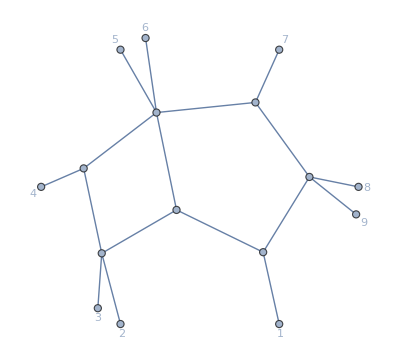

```mathematica
{DrawFeynGraph[dlist,9]}
```

```mathematica
result=LandauSolveAll[dlist,{y[1],y[2]},9,krep];
```

totally 148 need to be considered!

constraints equals or higher than 6!

```mathematica
lslist=ExtractLS[result];(*leading singularities*)
slist=ExtractSchubert[result];(*schubert configurations*)
```

```mathematica
clslist=ExtractLS[result,"chiral"->True,"dlist"->dlist];(*add chiral conditions for top sector since there is chiral numerator*)
```

```mathematica
sollist=ExtractSolution[result];(*the solutions of Schubert problems in each sector*)
```

#### top sector

the  cuts  and  pinch  conditions  for  the  top  sector/ top  diagram  in  Fig .17

```mathematica
(slist[[1]]//ToMT[#,9]&)/.{1->HoldForm[i],9->HoldForm[i-1],2->HoldForm[i+1],4->HoldForm[j],3->HoldForm[j-1],5->HoldForm[j+1],7->HoldForm[k],6->HoldForm[k-1],8->HoldForm[k+1]}/.{y[HoldForm[i]]->y[1],y[HoldForm[i+1]]->y[2]}//DisplayAll
```

{-Graphics-,{{y[1],{⟨ABi-1i⟩,⟨ABii+1⟩,⟨ABk-1k⟩,⟨ABkk+1⟩,-⟨ABjj+1⟩ ⟨ii+1j-1j⟩+⟨ABj-1j⟩ ⟨ii+1jj+1⟩}},{y[2],{⟨CDi-1i⟩,⟨CDii+1⟩,⟨CDj-1j⟩,⟨CDjj+1⟩,-⟨CDkk+1⟩ ⟨ii+1k-1k⟩+⟨CDk-1k⟩ ⟨ii+1kk+1⟩}}}}

```mathematica
(*corresponding leading singularities*)
```

```mathematica
lslist[[1]]/.{1->HoldForm[i],9->HoldForm[i-1],2->HoldForm[i+1],4->HoldForm[j],3->HoldForm[j-1],5->HoldForm[j+1],7->HoldForm[k],6->HoldForm[k-1],8->HoldForm[k+1]}/.{y[HoldForm[i]]->y[1],y[HoldForm[i+1]]->y[2]}//DisplayAll
```

{-Graphics-,{-⟨j-1j+1ij⟩ ⟨i+1ijk⟩,⟨(k - 1kk + 1)∩(jj + 1i - 1)ii+1⟩ ⟨j-1i+1ij⟩-⟨(k - 1kk + 1)∩(j - 1ji - 1)ii+1⟩ ⟨i+1j+1ij⟩,-⟨i-1i+1ik⟩ ⟨k-1k+1ik⟩,⟨k-1k+1ik⟩ ⟨i+1ijk⟩,-⟨(kk + 1i - 1)∩(j - 1jj + 1)ii+1⟩ ⟨k-1i+1ik⟩+⟨(k - 1ki - 1)∩(j - 1jj + 1)ii+1⟩ ⟨i+1k+1ik⟩}}

```mathematica
(*the chiral numerator will kill some singularities*)
```

```mathematica
clslist[[1]]/.{1->HoldForm[i],9->HoldForm[i-1],2->HoldForm[i+1],4->HoldForm[j],3->HoldForm[j-1],5->HoldForm[j+1],7->HoldForm[k],6->HoldForm[k-1],8->HoldForm[k+1]}/.{y[HoldForm[i]]->y[1],y[HoldForm[i+1]]->y[2]}//DisplayAll
```

{-Graphics-,{-⟨j-1j+1ij⟩ ⟨i+1ijk⟩,-⟨i-1i+1ik⟩ ⟨k-1k+1ik⟩,⟨k-1k+1ik⟩ ⟨i+1ijk⟩}}

```mathematica
clslist[[1,2]]
```

{-FB[1,2,4,7] FB[1,3,4,5],FB[1,2,7,9] FB[1,6,7,8],FB[1,2,4,7] FB[1,6,7,8]}

```mathematica
((Gram[{x[4],x[5],x[7],x[8],x[2]}]//ToMT[#,9]&)/.{FBI->FB}//FBCombine//FBCombine)^2*((Gram[{x[1],x[2],x[4],x[5]}]//ToMT[#,9]&)/.{FBI->FB}//FBCombine)*((Gram[{x[1],x[2],x[7],x[8]}]//ToMT[#,9]&)/.{FBI->FB}//FBCombine)/((Gram[{x[4],x[5],x[7],x[8]}]//ToMT[#,9]&)/.{FBI->FB}//FBCombine)
```

4 FB[Int[{6,7,8},{3,4,5}],1,2]^2 FB[1,2,4,7]^2 FB[1,2,4,9]^2 FB[1,2,7,9]^2 FB[1,3,4,5]^2 FB[1,6,7,8]^2

```mathematica
(*the solutions*)
```

```mathematica
sollist[[1]]
```

{-Graphics-,{{y[1],{{-BiTw[1,7],Int[{6,7,8},{2,1,9}]},{}}},{y[2],{{-BiTw[1,4],Int[{3,4,5},{2,1,9}]},{}}}}}

Find the corresponding Schubert configurations that can be combined to get the top sector condition

```mathematica
slist[[1,2,1]]
```

{y[1],{d[x[1],y[1]],d[x[2],y[1]],d[x[7],y[1]],d[x[8],y[1]],d[x[2],x[5]] d[x[4],y[1]]-d[x[2],x[4]] d[x[5],y[1]]}}

```mathematica
FindSchubertCombination[slist[[1,2,1]],slist]
```

{{{7,9}},{{7,8}},{{8,9}},{},{},{},{{2,7}},{{2,9}},{{2,8}},{}}

The result of FindSchubertCombination[] is organized by the one-dimensional space determined by three conditions so there are C_5^3 of them. Some one-dimensional spaces have no combinations and thus are  empty sets.

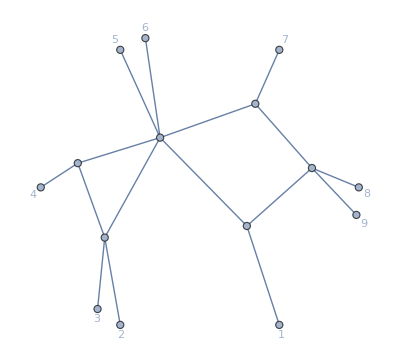
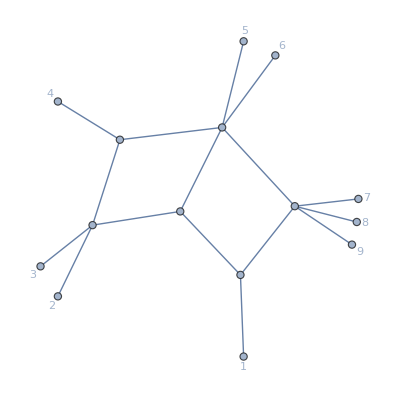
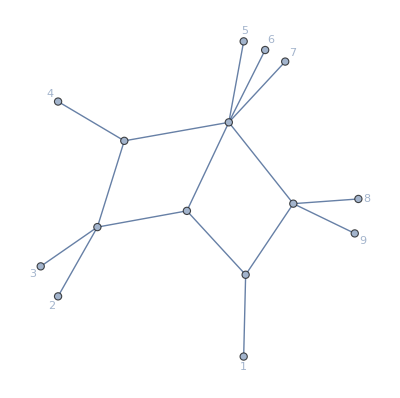
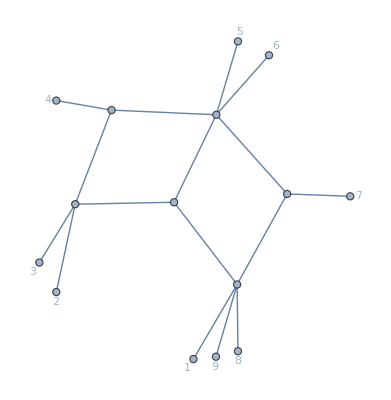
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
slist[[#,1]]&/@(Flatten[%,1])
```

We  can see that the mixing between above configurations give the top-sector condition! The box-triangle, namely 7,  is just equivalent to a one-loop box problem for y[1], it serves as a representative here. So we analyze the double box involved in above configurations in the next section, there are 3 of them, that is, 2,8, and 9.

#### double-box sub-sectors

Sub-sectors for the second line in Fig. 17

```mathematica
(slist[[2]]//ToMT[#,9]&)/.{1->HoldForm[i],9->HoldForm[i-1],2->HoldForm[i+1],4->HoldForm[j],3->HoldForm[j-1],5->HoldForm[j+1],7->HoldForm[k],6->HoldForm[k-1],8->HoldForm[k+1]}/.{y[HoldForm[i]]->y[1],y[HoldForm[i+1]]->y[2]}//DisplayAll
```

{-Graphics-,{{y[1],{⟨ABii+1⟩,⟨ABk-1k⟩,⟨ABkk+1⟩,-⟨ABjj+1⟩ ⟨ii+1j-1j⟩+⟨ABj-1j⟩ ⟨ii+1jj+1⟩}},{y[2],{⟨CDii+1⟩,⟨CDj-1j⟩,⟨CDjj+1⟩,-⟨CDkk+1⟩ ⟨ii+1k-1k⟩+⟨CDk-1k⟩ ⟨ii+1kk+1⟩}}}}

```mathematica
clslist[[2]](*/.{1->HoldForm[i],9->HoldForm[i-1],2->HoldForm[i+1],4->HoldForm[j],3->HoldForm[j-1],5->HoldForm[j+1],7->HoldForm[k],6->HoldForm[k-1],8->HoldForm[k+1]}/.{y[HoldForm[i]]->y[1],y[HoldForm[i+1]]->y[2]}//DisplayAll*)
```

{-Graphics-,{-(FB[Int[{6,7,8},{3,4,5}],1,2] FB[1,2,4,7] FB[1,2,6,7])/(FB[1,2,4,6] FB[2,3,4,5]),(FB[Int[{6,7,8},{3,4,5}],1,2] FB[1,2,3,4] FB[1,2,4,7])/(FB[1,2,3,7] FB[2,6,7,8])}}

```mathematica
{-(FB[Int[{6,7,8},{3,4,5}],1,2] FB[1,2,4,7] FB[1,2,6,7])/(FB[1,2,4,6] FB[2,3,4,5]),(FB[Int[{6,7,8},{3,4,5}],1,2] FB[1,2,3,4] FB[1,2,4,7])/(FB[1,2,3,7] FB[2,6,7,8])}/.{1->HoldForm[i],9->HoldForm[i-1],2->HoldForm[i+1],4->HoldForm[j],3->HoldForm[j-1],5->HoldForm[j+1],7->HoldForm[k],6->HoldForm[k-1],8->HoldForm[k+1]}//DisplayAll
```

{-(⟨(k - 1kk + 1)∩(j - 1jj + 1)ii+1⟩ ⟨k-1i+1ik⟩ ⟨i+1ijk⟩)/(⟨j-1i+1j+1j⟩ ⟨k-1i+1ij⟩),-(⟨(k - 1kk + 1)∩(j - 1jj + 1)ii+1⟩ ⟨j-1i+1ij⟩ ⟨i+1ijk⟩)/(⟨j-1i+1ik⟩ ⟨k-1i+1k+1k⟩)}

```mathematica
(*the Gram representation*)
```

```mathematica
((Gram[{x[4],x[5],x[7],x[8],x[2]}]//ToMT[#,9]&)/.{FBI->FB}//FBCombine//FBCombine)^2/4/((Gram[{x[4],x[5],x[7],x[8]}]//ToMT[#,9]&)/.{FBI->FB}//FBCombine)
```

FB[Int[{6,7,8},{3,4,5}],1,2]^2 FB[1,2,4,7]^2

```mathematica
(slist[[8]]//ToMT[#,9]&)/.{1->HoldForm[i],9->HoldForm[i-1],2->HoldForm[i+1],4->HoldForm[j],3->HoldForm[j-1],5->HoldForm[j+1],7->HoldForm[k],6->HoldForm[k-1],8->HoldForm[k+1]}/.{y[HoldForm[i]]->y[1],y[HoldForm[i+1]]->y[2]}//DisplayAll
```

{-Graphics-,{{y[1],{⟨ABi-1i⟩,⟨ABii+1⟩,⟨ABkk+1⟩,-⟨ABjj+1⟩ ⟨ii+1j-1j⟩+⟨ABj-1j⟩ ⟨ii+1jj+1⟩}},{y[2],{⟨CDi-1i⟩,⟨CDii+1⟩,⟨CDj-1j⟩,⟨CDjj+1⟩,⟨CDkk+1⟩}}}}

```mathematica
clslist[[8,2]]
%/.{FB[z__]:>(FB[z]/.{1->HoldForm[i],9->HoldForm[i-1],2->HoldForm[i+1],4->HoldForm[j],3->HoldForm[j-1],5->HoldForm[j+1],7->HoldForm[k],6->HoldForm[k-1],8->HoldForm[k+1]})}//DisplayAll
```

{-(FB[1,2,4,9] FB[1,2,7,8]^2 FB[1,3,4,5])/(FB[1,2,4,8] FB[2,3,4,5]),-FB[1,7,8,9],FB[1,2,7,8],-FB[1,4,7,8],-FB[Int[{1,2,9},{3,4,5}],8,7]}

{-(⟨i-1i+1ij⟩ ⟨j-1j+1ij⟩ ⟨i+1k+1ik⟩^2)/(⟨j-1i+1j+1j⟩ ⟨i+1k+1ij⟩),⟨i-1k+1ik⟩,-⟨i+1k+1ik⟩,⟨k+1ijk⟩,-⟨(ii + 1i - 1)∩(j - 1jj + 1)k+1k⟩}

```mathematica
(*the Gram representation*)
```

```mathematica
FB[1,2,7,8]^2((Gram[{x[1],x[2],x[4],x[5]}]//ToMT[#,9]&)/.{FBI->FB}//FBCombine//FBCombine)
```

FB[1,2,4,9]^2 FB[1,2,7,8]^2 FB[1,3,4,5]^2

```mathematica
(slist[[9]]//ToMT[#,9]&)/.{1->HoldForm[i],9->HoldForm[i-1],2->HoldForm[i+1],4->HoldForm[j],3->HoldForm[j-1],5->HoldForm[j+1],7->HoldForm[k],6->HoldForm[k-1],8->HoldForm[k+1]}/.{y[HoldForm[i]]->y[1],y[HoldForm[i+1]]->y[2]}//DisplayAll
```

{-Graphics-,{{y[1],{⟨ABi-1i⟩,⟨ABii+1⟩,⟨ABk-1k⟩,-⟨ABjj+1⟩ ⟨ii+1j-1j⟩+⟨ABj-1j⟩ ⟨ii+1jj+1⟩}},{y[2],{⟨CDi-1i⟩,⟨CDii+1⟩,⟨CDj-1j⟩,⟨CDjj+1⟩,⟨CDk-1k⟩}}}}

```mathematica
clslist[[9,2]]
```

{-(FB[1,2,4,9] FB[1,2,6,7]^2 FB[1,3,4,5])/(FB[1,2,4,7] FB[2,3,4,5]),-FB[1,6,7,9],FB[1,2,6,7],-FB[1,4,6,7],-FB[Int[{1,2,9},{3,4,5}],7,6]}

```mathematica
(*the Gram representation*)
```

```mathematica
FB[1,2,6,7]^2((Gram[{x[1],x[2],x[4],x[5]}]//ToMT[#,9]&)/.{FBI->FB}//FBCombine//FBCombine)
```

FB[1,2,4,9]^2 FB[1,2,6,7]^2 FB[1,3,4,5]^2

the  following  shrink  is  forbidden  by  Landau  diagrams  of  MHV  amplitude

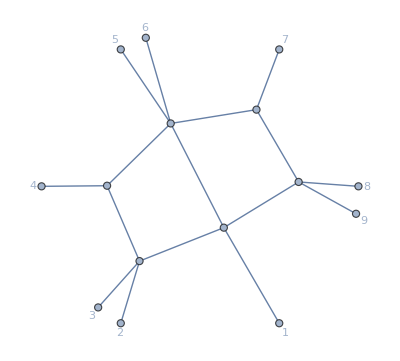
{-Graphics-,{{y[1],{⟨ABi-1i⟩,⟨ABii+1⟩,⟨ABk-1k⟩,⟨ABkk+1⟩,-⟨ABjj+1⟩ ⟨ii+1j-1j⟩+⟨ABj-1j⟩ ⟨ii+1jj+1⟩}},{y[2],{⟨CDi-1i⟩,⟨CDii+1⟩,⟨CDj-1j⟩,⟨CDjj+1⟩,-⟨CDkk+1⟩ ⟨i-1ik-1k⟩+⟨CDk-1k⟩ ⟨i-1ikk+1⟩}}}}

```mathematica
(slist[[3]]//ToMT[#,9]&)/.{1->HoldForm[i],9->HoldForm[i-1],2->HoldForm[i+1],4->HoldForm[j],3->HoldForm[j-1],5->HoldForm[j+1],7->HoldForm[k],6->HoldForm[k-1],8->HoldForm[k+1]}/.{y[HoldForm[i]]->y[1],y[HoldForm[i+1]]->y[2]}//DisplayAll
```

#### penta-triangle sub-sectors

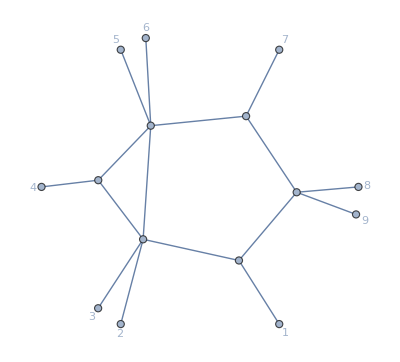
{-Graphics-,{{y[1],{⟨ABi-1i⟩,⟨ABii+1⟩,⟨ABj-1j⟩,⟨ABjj+1⟩,⟨ABk-1k⟩,⟨ABkk+1⟩}},{y[2],{⟨CDj-1j⟩,⟨CDjj+1⟩,⟨CDii+1⟩ ⟨CDkk+1⟩ ⟨i-1ik-1k⟩-⟨CDk-1k⟩ ⟨CDii+1⟩ ⟨i-1ikk+1⟩-⟨CDi-1i⟩ ⟨CDkk+1⟩ ⟨ii+1k-1k⟩+⟨CDi-1i⟩ ⟨CDk-1k⟩ ⟨ii+1kk+1⟩}}}}

```mathematica
(slist[[4]]//ToMT[#,9]&)/.{1->HoldForm[i],9->HoldForm[i-1],2->HoldForm[i+1],4->HoldForm[j],3->HoldForm[j-1],5->HoldForm[j+1],7->HoldForm[k],6->HoldForm[k-1],8->HoldForm[k+1]}/.{y[HoldForm[i]]->y[1],y[HoldForm[i+1]]->y[2]}//DisplayAll
```

Note here that for y[2], there are only three conditions. for y[1], there are 6 conditions, this is the most degenerate case in these diagram. For all these constraints to be satisfied, it provides a more constrained condition for external kinematics. For this reason, we don’t list its leading singularities, it only serves as a seed for us to find which two Schubert configurations can be combined.

```mathematica
slist[[4,2,1]]
```

{y[1],{d[x[1],y[1]],d[x[2],y[1]],d[x[4],y[1]],d[x[5],y[1]],d[x[7],y[1]],d[x[8],y[1]]}}

```mathematica
FindSchubertCombination[slist[[4,2,1]],slist]
```

intermediate configurations involved: {1,5,6,11,17,29,33}

{{{7,9,34,35}},{{7,8,30,31}},{},{{2,7,12,13}},{{30,34,86}},{{34,59,69}},{{30,59,65}},{{12,34,54}},{{12,30,50}},{{12,38,59}},{{31,35,86}},{{35,60,69}},{{31,60,65}},{{13,35,54}},{{13,31,50}},{{13,38,60}},{{50,54,86}},{{38,54,69}},{{38,50,65}},{{65,69,86}}}

The output of FindSchubertCombination[] is organized according to the one-dimensional space involved.

Note that the FindSchubertCombination[] first find two Schubert configurations that can be combined to give the target configuration, then if one or both of these two configurations involve more than 4 conditions we decompose it again until we find a set of configurations that are all 4-condition configurations. This results in a tree-like structure: for example, slist[[4,2,1]]->{1,5}->{{7,9},{7,34}}, the number is the index of each configuration

```mathematica
(*mixing between double box and boxes*)
```

```mathematica
slist[[{7,9,34,35},2,1]]
```

{{y[1],{d[x[1],y[1]],d[x[2],y[1]],d[x[7],y[1]],d[x[8],y[1]]}},{y[1],{d[x[1],y[1]],d[x[2],y[1]],d[x[7],y[1]],d[x[2],x[5]] d[x[4],y[1]]-d[x[2],x[4]] d[x[5],y[1]]}},{y[1],{d[x[1],y[1]],d[x[2],y[1]],d[x[5],y[1]],d[x[7],y[1]]}},{y[1],{d[x[1],y[1]],d[x[2],y[1]],d[x[4],y[1]],d[x[7],y[1]]}}}

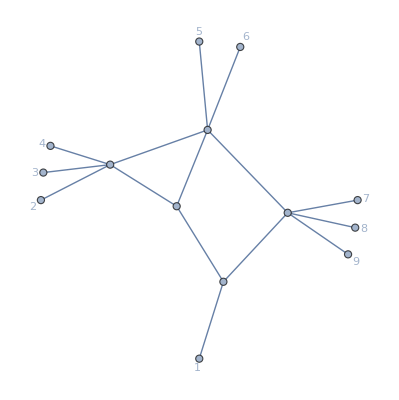
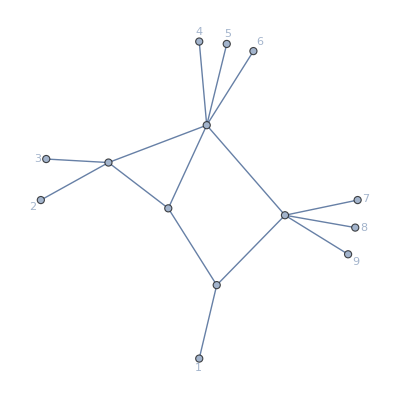
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
slist[[{7,9,34,35},1]]
```

```mathematica
slist[[{7,8,30,31},2,1]]
```

{{y[1],{d[x[1],y[1]],d[x[2],y[1]],d[x[7],y[1]],d[x[8],y[1]]}},{y[1],{d[x[1],y[1]],d[x[2],y[1]],d[x[8],y[1]],d[x[2],x[5]] d[x[4],y[1]]-d[x[2],x[4]] d[x[5],y[1]]}},{y[1],{d[x[1],y[1]],d[x[2],y[1]],d[x[5],y[1]],d[x[8],y[1]]}},{y[1],{d[x[1],y[1]],d[x[2],y[1]],d[x[4],y[1]],d[x[8],y[1]]}}}

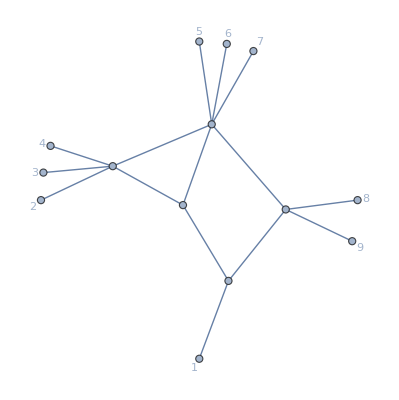
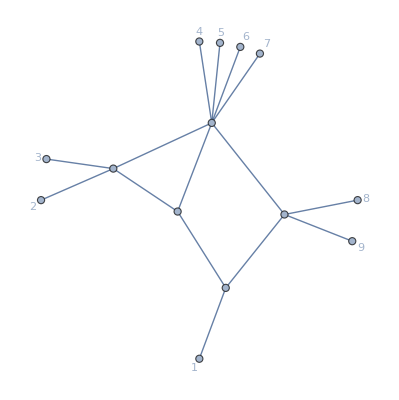
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
slist[[{7,8,30,31},1]]
```

```mathematica
slist[[{2,7,12,13},2,1]]
```

{{y[1],{d[x[2],y[1]],d[x[7],y[1]],d[x[8],y[1]],d[x[2],x[5]] d[x[4],y[1]]-d[x[2],x[4]] d[x[5],y[1]]}},{y[1],{d[x[1],y[1]],d[x[2],y[1]],d[x[7],y[1]],d[x[8],y[1]]}},{y[1],{d[x[2],y[1]],d[x[5],y[1]],d[x[7],y[1]],d[x[8],y[1]]}},{y[1],{d[x[2],y[1]],d[x[4],y[1]],d[x[7],y[1]],d[x[8],y[1]]}}}

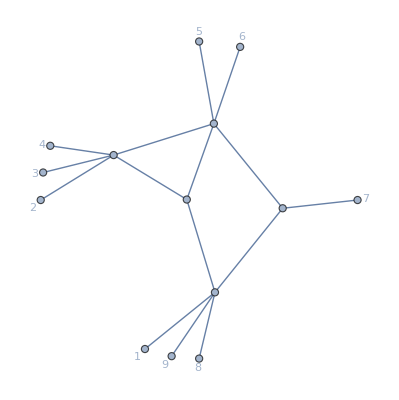
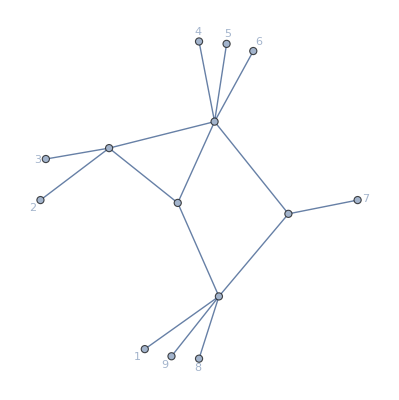
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
slist[[{2,7,12,13},1]]
```

Though above combination involves 4 pairs of solutions on the same one-dimensional space, but we can actually see that three box configurations (the three box-triangle topologies) in it already imply the double-box configuration, so though it seems to be an A_5 configuration, the letters generated actually equivalent to an A_3configuration. Note that the double-box configuration does not generate new square root. This indicates that we only need to study all combinations between box configurations.

```mathematica
(*mixing between boxes: the followings are two representatives*)
```

{{y[1],{d[x[1],y[1]],d[x[2],y[1]],d[x[4],y[1]],d[x[8],y[1]]}},{y[1],{d[x[1],y[1]],d[x[2],y[1]],d[x[4],y[1]],d[x[7],y[1]]}},{y[1],{d[x[1],y[1]],d[x[2],y[1]],d[x[4],y[1]],d[x[5],y[1]]}}}

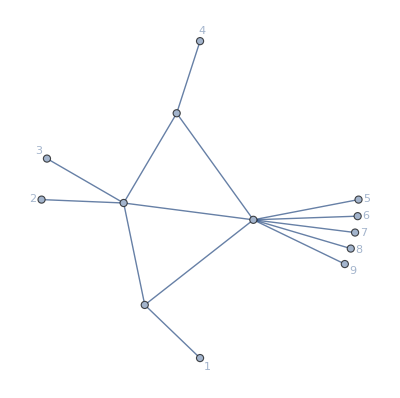
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
slist[[{31,35,86},2,1]]
slist[[{31,35,86},1]](*the following three are all box configuration*)
```

{{y[1],{d[x[2],y[1]],d[x[5],y[1]],d[x[7],y[1]],d[x[8],y[1]]}},{y[1],{d[x[1],y[1]],d[x[2],y[1]],d[x[5],y[1]],d[x[7],y[1]]}},{y[1],{d[x[2],y[1]],d[x[4],y[1]],d[x[5],y[1]],d[x[7],y[1]]}}}

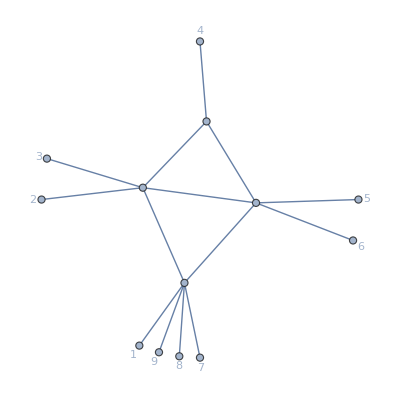
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
slist[[{12,34,54},2,1]]
slist[[{12,34,54},1]]
```

Take the last combination as an example, we can solve the six solutions on the one-dimensional space as

```mathematica
SchubertSolve[{x[2],x[5],x[7]},9](*give a parameterization for three conditions*)
```

SchubertSolve::warning: Results depend on the parameterization! You can specify the parameterization by option "Param" like "Param"->{3,4}, then it will be parametrized as Z[3]+α*Z[4]. Here we choose one such parameterization.

{Int[{6,7,4},{1,2,4}]+α Int[{6,7,4},{1,2,5}]+α Int[{6,7,5},{1,2,4}]+α^2 Int[{6,7,5},{1,2,5}]}

```mathematica
sol1=Solve[FB[Int[{6,7,4},{1,2,4}]+α Int[{6,7,4},{1,2,5}]+α Int[{6,7,5},{1,2,4}]+α^2 Int[{6,7,5},{1,2,5}],7,8]==0,α]
```

{{α→1/(2 FB[Int[{6,7,5},{1,2,5}],7,8])(-FB[Int[{6,7,4},{1,2,5}],7,8]-FB[Int[{6,7,5},{1,2,4}],7,8]-√((FB[Int[{6,7,4},{1,2,5}],7,8]+FB[Int[{6,7,5},{1,2,4}],7,8])^2-4 FB[Int[{6,7,4},{1,2,4}],7,8] FB[Int[{6,7,5},{1,2,5}],7,8]))},{α→1/(2 FB[Int[{6,7,5},{1,2,5}],7,8])(-FB[Int[{6,7,4},{1,2,5}],7,8]-FB[Int[{6,7,5},{1,2,4}],7,8]+√((FB[Int[{6,7,4},{1,2,5}],7,8]+FB[Int[{6,7,5},{1,2,4}],7,8])^2-4 FB[Int[{6,7,4},{1,2,4}],7,8] FB[Int[{6,7,5},{1,2,5}],7,8]))}}

```mathematica
sol2=Solve[FB[Int[{6,7,4},{1,2,4}]+α Int[{6,7,4},{1,2,5}]+α Int[{6,7,5},{1,2,4}]+α^2 Int[{6,7,5},{1,2,5}],9,1]==0,α]
```

{{α→1/(2 FB[Int[{6,7,5},{1,2,5}],9,1])(-FB[Int[{6,7,4},{1,2,5}],9,1]-FB[Int[{6,7,5},{1,2,4}],9,1]-√((FB[Int[{6,7,4},{1,2,5}],9,1]+FB[Int[{6,7,5},{1,2,4}],9,1])^2-4 FB[Int[{6,7,4},{1,2,4}],9,1] FB[Int[{6,7,5},{1,2,5}],9,1]))},{α→1/(2 FB[Int[{6,7,5},{1,2,5}],9,1])(-FB[Int[{6,7,4},{1,2,5}],9,1]-FB[Int[{6,7,5},{1,2,4}],9,1]+√((FB[Int[{6,7,4},{1,2,5}],9,1]+FB[Int[{6,7,5},{1,2,4}],9,1])^2-4 FB[Int[{6,7,4},{1,2,4}],9,1] FB[Int[{6,7,5},{1,2,5}],9,1]))}}

```mathematica
sol3=Solve[FB[Int[{6,7,4},{1,2,4}]+α Int[{6,7,4},{1,2,5}]+α Int[{6,7,5},{1,2,4}]+α^2 Int[{6,7,5},{1,2,5}],3,4]==0,α]
```

{{α→1/(2 FB[Int[{6,7,5},{1,2,5}],3,4])(-FB[Int[{6,7,4},{1,2,5}],3,4]-FB[Int[{6,7,5},{1,2,4}],3,4]-√((FB[Int[{6,7,4},{1,2,5}],3,4]+FB[Int[{6,7,5},{1,2,4}],3,4])^2-4 FB[Int[{6,7,4},{1,2,4}],3,4] FB[Int[{6,7,5},{1,2,5}],3,4]))},{α→1/(2 FB[Int[{6,7,5},{1,2,5}],3,4])(-FB[Int[{6,7,4},{1,2,5}],3,4]-FB[Int[{6,7,5},{1,2,4}],3,4]+√((FB[Int[{6,7,4},{1,2,5}],3,4]+FB[Int[{6,7,5},{1,2,4}],3,4])^2-4 FB[Int[{6,7,4},{1,2,4}],3,4] FB[Int[{6,7,5},{1,2,5}],3,4]))}}

```mathematica
FB[Int[{6,7,4},{1,2,4}]+α Int[{6,7,4},{1,2,5}]+α Int[{6,7,5},{1,2,4}]+α^2 Int[{6,7,5},{1,2,5}],Int[{6,7,4},{1,2,4}]+β Int[{6,7,4},{1,2,5}]+β Int[{6,7,5},{1,2,4}]+β^2 Int[{6,7,5},{1,2,5}]]//MTExpand//FBCombine(*distance between two solutions*)
```

-(α-β)^2 FB[1,2,4,5] FB[1,2,6,7] FB[4,5,6,7]

```mathematica
(*above square roots are not true, they can all be calculated to be perfect squares*)
```

```mathematica
rep={m22->FB[1,2,3,4],m42->FB[4,5,6,7],m62->FB[7,8,9,1],s12->FB[9,1,3,4],s23->FB[1,2,4,5],s34->FB[3,4,6,7],s45->FB[4,5,7,8],s56->FB[6,7,9,1],s61->FB[7,8,1,2],s123->FB[9,1,4,5],s234->FB[1,2,6,7],s345->FB[7,8,3,4]};
invrep={FB[1,2,3,4]->m22,FB[4,5,6,7]->m42,FB[1,7,8,9]->-m62,FB[1,3,4,9]->-s12,FB[1,2,4,5]->s23,FB[3,4,6,7]->s34,FB[4,5,7,8]->s45,FB[1,6,7,9]->-s56,FB[1,2,7,8]->s61,FB[1,4,5,9]->-s123,FB[1,2,6,7]->s234,FB[3,4,7,8]->s345};
```

```mathematica
(ReconstructExp[(FB[Int[{6,7,4},{1,2,5}],7,8]+FB[Int[{6,7,5},{1,2,4}],7,8])^2-4 FB[Int[{6,7,4},{1,2,4}],7,8] FB[Int[{6,7,5},{1,2,5}],7,8],Values[rep]]//Factor)/.invrep
```

(-s234 s45+m42 s61)^2

```mathematica
(ReconstructExp[(FB[Int[{6,7,4},{1,2,5}],9,1]+FB[Int[{6,7,5},{1,2,4}],9,1])^2-4 FB[Int[{6,7,4},{1,2,4}],9,1] FB[Int[{6,7,5},{1,2,5}],9,1],Values[rep]]//Factor)/.invrep
```

(-s123 s234+s23 s56)^2

```mathematica
(ReconstructExp[(FB[Int[{6,7,4},{1,2,5}],3,4]+FB[Int[{6,7,5},{1,2,4}],3,4])^2-4 FB[Int[{6,7,4},{1,2,4}],3,4] FB[Int[{6,7,5},{1,2,5}],3,4],Values[rep]]//Factor)/.invrep
```

(-m22 m42+s23 s34)^2

All the remaining two penta-triangle topologies only involve five conditions and they will be taken as combinations of boxes. Their singularities are characterized by five-term Gram determinants.

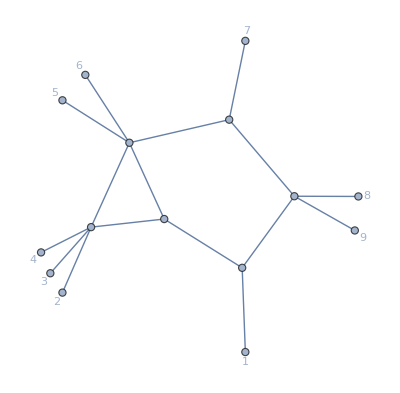
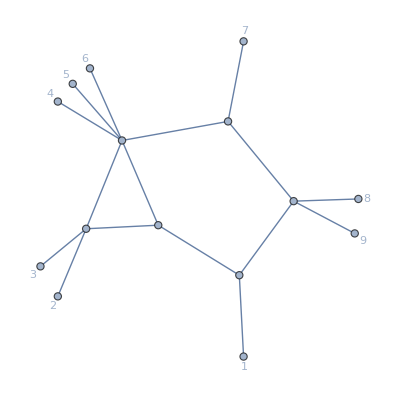
{{-Graphics-,{{y[1],{d[x[1],y[1]],d[x[2],y[1]],d[x[5],y[1]],d[x[7],y[1]],d[x[8],y[1]]}},{y[2],{d[x[1],y[2]],d[x[2],y[2]],d[x[5],y[2]],d[x[2],x[8]] d[x[7],y[2]]-d[x[2],x[7]] d[x[8],y[2]]}}}},{-Graphics-,{{y[1],{d[x[1],y[1]],d[x[2],y[1]],d[x[4],y[1]],d[x[7],y[1]],d[x[8],y[1]]}},{y[2],{d[x[1],y[2]],d[x[2],y[2]],d[x[4],y[2]],d[x[2],x[8]] d[x[7],y[2]]-d[x[2],x[7]] d[x[8],y[2]]}}}}}

```mathematica
slist[[{5,6}]]
```

```mathematica
lslist[[{5,6}]]
```

{{-Graphics-,{FB[1,2,4,5],-FB[1,4,5,7],-FB[Int[{1,2,9},{6,7,8}],5,4],FB[1,2,7,9] FB[1,6,7,8],(FB[1,2,4,5]^2 FB[1,2,7,9] FB[1,6,7,8])/(FB[1,2,5,7] FB[2,6,7,8])}},{-Graphics-,{FB[1,2,3,4],-FB[1,3,4,7],-FB[Int[{1,2,9},{6,7,8}],4,3],FB[1,2,7,9] FB[1,6,7,8],(FB[1,2,3,4]^2 FB[1,2,7,9] FB[1,6,7,8])/(FB[1,2,4,7] FB[2,6,7,8])}}}

#### box-triangle sub-sectors

We first pick out all box-triangle topology

```mathematica
Position[((Length/@(FindCycle[#,Infinity,All]))//Sort)&/@lslist[[All,1]],{3,4,5},1]//Flatten
```

{10,11,12,13,15,16,17,18,19,21,22,29,30,31,33,34,35,37}

Note that most box-triangle sub-sectors are equivalent to box configurations, these are trivial. The non-trivial box-triangle topologies are

```mathematica
Position[Length[Cases[#,x[_],Infinity]//DeleteDuplicates]&/@slist[[{10,11,12,13,15,16,17,18,19,21,22,29,30,31,33,34,35,37}]],5,1]//Flatten
```

{1,2,7,8,9,10,11,12,15}

```mathematica
{10,11,12,13,15,16,17,18,19,21,22,29,30,31,33,34,35,37}[[{1,2,7,8,9,10,11,12,15}]](*non-trivial topology*)
```

{10,11,17,18,19,21,22,29,33}

```mathematica
Complement[{10,11,12,13,15,16,17,18,19,21,22,29,30,31,33,34,35,37},{10,11,17,18,19,21,22,29,33}](*trivial topology*)
```

{12,13,15,16,30,31,34,35,37}

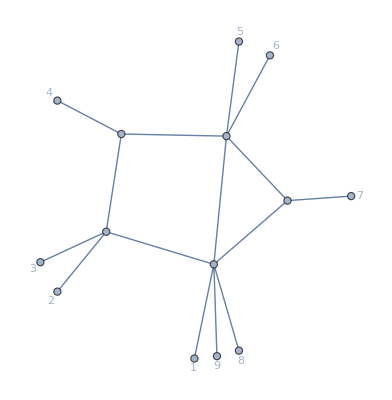
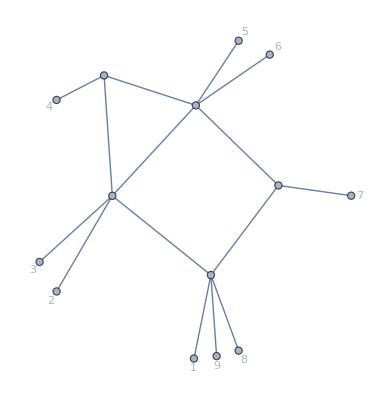
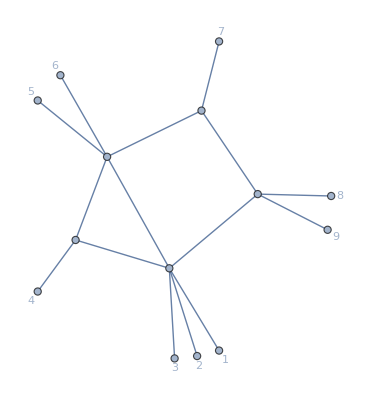
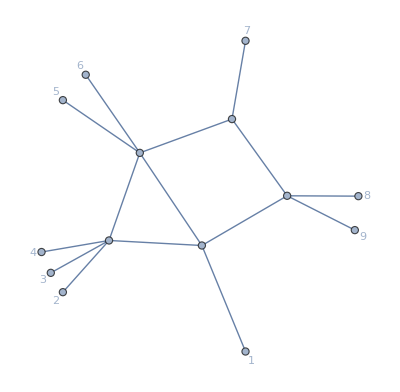
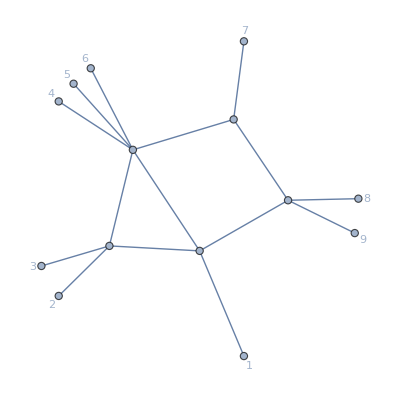
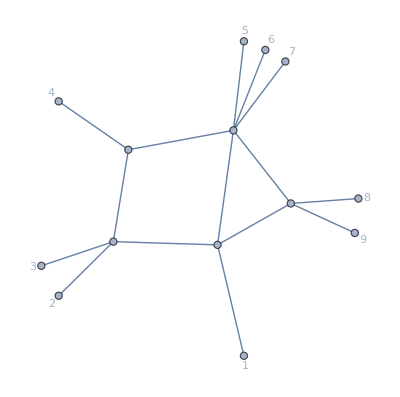
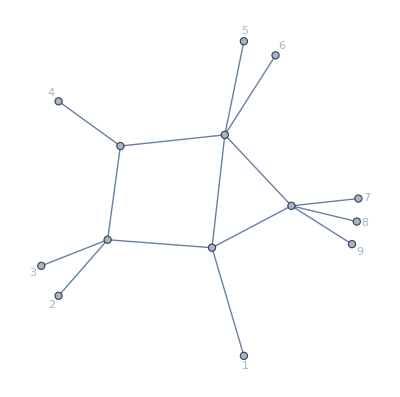
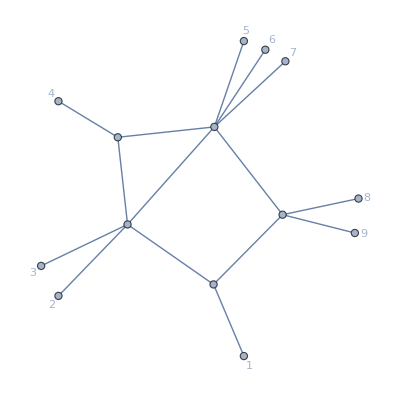
{{-Graphics-,{-(FB[Int[{6,7,8},{3,4,5}],1,2] FB[1,2,4,7] FB[1,2,6,7])/(FB[1,2,4,6] FB[2,3,4,5]),FB[1,2,4,7],-FB[Int[{6,7,8},{3,4,5}],1,2]}},{-Graphics-,{FB[1,2,4,7],-FB[Int[{6,7,8},{3,4,5}],1,2],(FB[Int[{6,7,8},{3,4,5}],1,2] FB[1,2,3,4] FB[1,2,4,7])/(FB[1,2,3,7] FB[2,6,7,8])}},{-Graphics-,{FB[1,4,7,9],-FB[Int[{6,7,8},{3,4,5}],1,9],-(FB[Int[{6,7,8},{3,4,5}],1,9] FB[1,3,4,9] FB[1,4,7,9])/(FB[1,3,7,9] FB[6,7,8,9])}},{-Graphics-,{FB[1,2,4,5],-FB[1,4,5,7],-FB[Int[{1,2,9},{6,7,8}],5,4],-(FB[1,2,4,5] FB[1,2,7,9] FB[1,4,5,9]^2 FB[1,6,7,8])/(FB[Int[{6,7,8},{2,4,5}],1,9] FB[1,5,7,9])}},{-Graphics-,{FB[1,2,3,4],-FB[1,3,4,7],-FB[Int[{1,2,9},{6,7,8}],4,3],-(FB[1,2,3,4] FB[1,2,7,9] FB[1,3,4,9]^2 FB[1,6,7,8])/(FB[Int[{6,7,8},{2,3,4}],1,9] FB[1,4,7,9])}},{-Graphics-,{-(FB[1,2,4,9] FB[1,2,7,8]^2 FB[1,3,4,5])/(FB[1,2,4,8] FB[2,3,4,5]),-FB[1,7,8,9],-FB[1,4,7,8],-FB[Int[{1,2,9},{3,4,5}],8,7]}},{-Graphics-,{-(FB[1,2,4,9] FB[1,2,6,7]^2 FB[1,3,4,5])/(FB[1,2,4,7] FB[2,3,4,5]),-FB[1,6,7,9],-FB[1,4,6,7],-FB[Int[{1,2,9},{3,4,5}],7,6]}},{-Graphics-,{-FB[1,4,7,8],-FB[Int[{1,2,9},{3,4,5}],8,7],-(FB[Int[{1,2,9},{3,4,5}],8,7] FB[1,4,7,8] FB[3,4,7,8])/(FB[1,2,8,9] FB[1,3,7,8])}},{-Graphics-,{-FB[1,4,6,7],-FB[Int[{1,2,9},{3,4,5}],7,6],-(FB[Int[{1,2,9},{3,4,5}],7,6] FB[1,4,6,7] FB[3,4,6,7])/(FB[1,2,7,9] FB[1,3,6,7])}}}

```mathematica
lslist[[{10,11,17,18,19,21,22,29,33}]](*the nontrivial Schubert configurations and corresponding leading singularoties for box triangles*)
```

The remaining sub-sectors will not be considered further since they are trivial.